This notebook is provided as a companion resource for readers of Algebraic Functions by Dominic Milioto.  Commercial use of this notebook or its contents outside the context of the book is not permitted without the author’s permission.  The notebook is designed  with Mathematica version 13.2 and tested with version 15.  It contains stylesheet code to maintain the Report style, and classic bracketing [ [ ] ] for version 15.   See “Edit Stylesheet” and  notebook Initialization code for more information about these  changes.  

This notebook includes the test cases used in the chapter tutorials as well as additional cases intended for exploration and not exhaustively tested  and therefore may encounter software or numerical issues that can often be corrected by parameter adjustments.

# Chapter 4: Series Comparison Test and Integration Test

## Draw plots of integration contours

### Plot integration contours

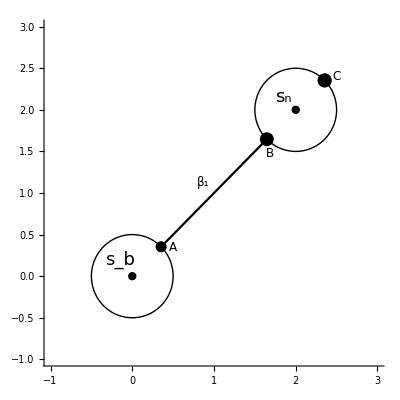

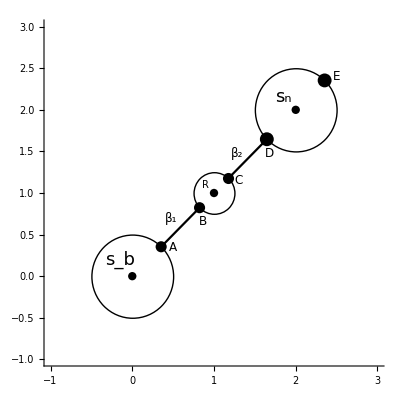

```mathematica
(*
 draw plot of contours 
*)

basePoint=0;
basePointG=Graphics@{PointSize[0.015],Point@{0,0}};
r1=1/2;
nextPoint=2+2 I;
point2=1+1I;
r3=1/4;
nextPointG=Graphics@{PointSize[0.015],Point@ReIm@nextPoint};
point2G=Graphics@{PointSize[0.015],Point@ReIm@point2};
r2=1/2;
{baseNDZ,nextNDZ,nextNDZ2}=getIntegrationData2[basePoint,r1,nextPoint,r2,30];
{baseNDZ2,nextNDZb,nextNDZ3}=getIntegrationData2[basePoint,r1,point2,r3,30];
{baseNDZ3,nextNDZ3,nextNDZ4}=getIntegrationData2[nextPoint,r2,point2,r3,30];

baseNDZG=Graphics@{PointSize[0.02],Point@ReIm@baseNDZ};

nextNDZG=Graphics@{PointSize[0.025],Point@ReIm@nextNDZ};
nextNDZ2G=Graphics@{PointSize[0.025],Point@ReIm@nextNDZ2};

baseCircleG=Graphics@{Circle[ReIm@basePoint,r1]};
nextCircleG=Graphics@{Circle[ReIm@nextPoint,r2]};
nextCircleG2=Graphics@{Circle[ReIm@point2,r3]};
nextCircleArcG=Graphics@{Red,Circle[ReIm@point2,r3,{Arg[nextNDZb],Arg[nextNDZb]-Pi}]};
nextCircleArcG2=Graphics@{Black,Dashed,Circle[ReIm@point2,r3,{Arg[nextNDZb],Arg[nextNDZb]+Pi}]};
cTable1=Table[ReIm[point2+r3 Exp[I t]],{t,Arg[nextNDZb]-Pi,Arg[nextNDZb]-0.1,1/30}];
arrow1=Graphics@{Arrowheads[0.025],Arrow[cTable1]};

cTable2=Table[ReIm[point2+r3 Exp[I t]],{t,Arg[nextNDZb]+Pi,Arg[nextNDZb]+0.175,-1/30}];
arrow2=Graphics@{Arrowheads[0.025],Arrow[cTable2]};
nextCircleArcG3=Graphics@{Red,Circle[ReIm@point2,r3]};


zTrace[t_]:=baseNDZ(1-t)+nextNDZ t;
zTrace2[t_]:=baseNDZ(1-t)+nextNDZb t;
zTrace3[t_]:=nextNDZ3(1-t)+nextNDZ t;
nextNDZ3G=Graphics@{PointSize[0.02],Point@ReIm@nextNDZ3};
dPointG=Graphics@{PointSize[0.02],Point@ReIm@nextNDZ2};
ePointG=Graphics@{PointSize[0.02],Point@ReIm@nextNDZb};
(*zTrace2[t_]:=baseSingularPoint(1-t)+nextTestSing t;*)
baseNDPointG=Graphics@{PointSize[0.2],Black,Point@ReIm@((baseNDZ+nextNDZ)/2)};
pp1=ParametricPlot[ReIm@zTrace[t],{t,0,1},AspectRatio->1,PlotStyle->Black];
pp2=ParametricPlot[ReIm@zTrace2[t],{t,0,1},AspectRatio->1,PlotStyle->Black];
pp3=ParametricPlot[ReIm@zTrace3[t],{t,0,1},AspectRatio->1,PlotStyle->Black];
pRange=Options[pp1,PlotRange];
pVals=PlotRange/.pRange;
thePlotRange=pVals+{{-0.2,0.4},{-0.1,0.1}};
text1=Graphics@Text[Style["A",12],{0.5,0.35}];
text2=Graphics@Text[Style["β_1",12],{0.87,1.13}];
text2b=Graphics@Text[Style["β_1",12],{0.48,0.69}];
text2c=Graphics@Text[Style["β_2",12],{1.24,0.75}];
text3c=Graphics@Text[Style["β_2",12],{1.28,1.48}];
text4c=Graphics@Text[Style["β_3",12],{0.73,1.25}];
text3=Graphics@Text[Style["D",12],{1.68,1.47}];
text5=Graphics@Text[Style["B",12],{3.7,3.4}];
text5C=Graphics@Text[Style["C",12],{2.5,2.4}];

text30=Graphics@Text[Style["B",12],{1.68,1.47}];


text7=Graphics@Text[Style["s_b",18],{-0.15,0.2}];
text8=Graphics@Text[Style["s_n",18],{1.85,2.15}];
text9=Graphics@Text[Style["B",12],{.86,0.66}];
text10=Graphics@Text[Style["R",10],{0.9,1.1}];
text11=Graphics@Text[Style["C",12],{1.3,1.15}];
text12=Graphics@Text[Style["B",12],{0.86,.66}];
text13=Graphics@Text[Style["E",12],{2.5,2.4}];





path1=Show[{basePointG,nextPointG,baseCircleG,nextCircleG,baseNDZG,nextNDZG,nextNDZ2G,pp1,text1,text2,text7,text8,text5C,nextNDZ2G,text30},PlotRange->{{-1,3},{-1,3}},Axes->True(*PlotLabel->Style["Integration path between s_b and s_n",12,Bold,Black]*)];


path2=Show[{basePointG,baseCircleG,nextCircleG,pp3,pp2,text1,text3,point2G,ePointG,nextCircleG2,text7,text8,text10,nextNDZ3G,text2b,text3c,text12,text11,nextPointG,baseNDZG,nextNDZG,text13,nextNDZ2G},Axes->True,PlotRange->{{-1,3},{-1,3}}(*,PlotLabel->Column[{Style["Integration path between s_b and s_n",12,Bold,Black],Style["with intervening R",12,Bold,Black]},Center]*)
];

Show[path1]
Show[path2]
GraphicsRow[{Show[{path1}],Show[path2]}]
```

### Plot of integration path through removable singular point

```mathematica
pb=-10;
pbR=1;
pr=-4;
prR=1
pn=3;
pnR=1;
pe=9;
peR=1;
circleB=Circle[{pb,0},pbR];
circleR=Circle[{pr,0},prR];
circleN=Circle[{pn,0},pnR];
circleE=Circle[{pe,0},peR];
{pA,pB,pC}=getIntegrationData[pb,pbR,pr,prR];
{pC,pD,pE}=getIntegrationData[pr,prR,pn,pnR];
{pE,pF,pG}=getIntegrationData[pn,pnR,pe,peR];

pnP={PointSize[0.007],Point[{pn,0}]};
prP={PointSize[0.007],Point[{pr,0}]};
pbP={PointSize[0.007],Point[{pb,0}]};
peP={PointSize[0.007],Point[{pe,0}]};
pAP={PointSize[0.0107],Point[{pA,0}]};
pBP={PointSize[0.0107],Point[{pB,0}]};
pCP={PointSize[0.0107],Point[{pC,0}]};
pDP={PointSize[0.0107],Point[{pD,0}]};
pDE={PointSize[0.0107],Point[{pE,0}]};
pDF={PointSize[0.0107],Point[{pF,0}]};
pDG={PointSize[0.0107],Point[{pG,0}]};
aText=Text[Style["A",10],{-8.7,0.47}];
bText=Text[Style["B",10],{-5.3,0.47}];
cText=Text[Style["C",10],{-2.7,0.47}];
cText2=Text[Style["A",10],{-2.7,-0.47}];
dText=Text[Style["D",10],{1.7,0.47}];
dText2=Text[Style["B",10],{1.7,-0.47}];
eText=Text[Style["E",10],{4.2,0.47}];
eText2=Text[Style["A",10],{4.2,-0.47}];
fText=Text[Style["F",10],{7.6,0.47}];
fText2=Text[Style["B",10],{7.6,-0.47}];
gText=Text[Style["G",10],{10.29,0.47}];
sbText=Text[Style["s_2",12],{pb,0.5}];
s1Text=Text[Style["s_1",12],{pr,0.5}];
s2Text=Text[Style["s_4",12],{pn,0.5}];
s3Text=Text[Style["s_5",12],{pe,0.5}];
a1={Arrowheads[0.03],Arrow[{{pA,0},{pB,0}}]};
a2={Arrowheads[0.03],Arrow[{{pC,0},{pD,0}}]};
a3={Arrowheads[0.03],Arrow[{{pE,0},{pF,0}}]};
beta1Text=Text[Style["β_1",12],{-7.2,-0.5}];
beta2Text=Text[Style["β_2",12],{-0.5,-0.5}];
beta3Text=Text[Style["β_3",12],{5.86,-0.5}];



Show[Graphics@{circleB,circleR,circleN,pbP,pAP,aText,bText,cText,dText,pCP,pBP,pDP,s2Text,prP,pnP,a1,a2,beta1Text,beta2Text,beta3Text,circleE,s1Text,sbText,pDE,pDF,eText,pDG,fText,gText,a3,s3Text,peP},Axes->False,PlotRange->{{-11,11},{-3,3}}]
```

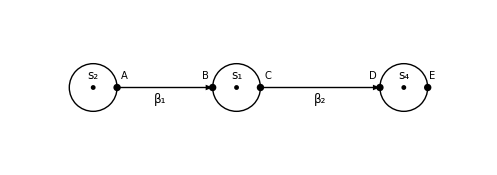

```mathematica
Show[Graphics@{circleB,circleR,circleN,pbP,pAP,aText,bText,cText,dText,pCP,pBP,pDP,s2Text,prP,pnP,a1,a2,beta1Text,beta2Text,s1Text,sbText,pDE,eText},Axes->False,PlotRange->{{-12,5},{-3,3}}]
```

## Section 1: Choose test case

### testCase0001: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at the origin

```mathematica
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

Function: (181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

#### Expansion at infinity by prepending zero to singular points (testCase0001Inf0)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(181/15-17/20 z+71/15 z^2+4/5 z^3+11/3 z^4-5/3 z^5)+(-77/20+4/5 z^3+1/15 z^5) w+(-2+25/12 z^2-2/5 z^3+1 z^5) w^2+(7/5) w^3+(125/12+1/2 z-2 z^4-5/2 z^5) w^4+(11/2+3 z^2+1 z^5) w^5;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0001Inf0";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-5/3+11/3 z+4/5 z^2+71/15 z^3-17/20 z^4+181/15 z^5)+(1/15+4/5 z^2-77/20 z^5) w+(1-2/5 z^2+25/12 z^3-2 z^5) w^2+(7/5 z^5) w^3+(-5/2-2 z+1/2 z^4+125/12 z^5) w^4+(1+3 z^3+11/2 z^5) w^5

5

11/3

1/15

### testCase0002: 15-degree with 1,2,3,4,5-cycle from paper 2, Function Genus: 86

#### Expansion at the origin

```mathematica
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
$theTestCase="testCase0002";
subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (z^30+1 z^32)+(z^14+1 z^20) w^5+(z^5+1 z^9) w^9+(z+1 z^3) w^12+(6) w^14+(2+1 z^2) w^15

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

$theTestCase="testCase0002Inf";
subDirectory=$theTestCase;
$theTestCase="testCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0003: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4 with removable singularity at origin

#### Expansion at zero

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003";


subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9 z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7 z^3+8 z^4)w^4;
$theTestCase="testCase0003Inf";
subDirectory=$theTestCase;

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;



If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

aForm[$theFunction]
```

(z-1 z^2)+(3 z^2-4 z^3) w+(-9-1 z) w^2+(-4 z+4 z^2+8 z^3-2 z^4) w^3+(8+7 z-8 z^2+6 z^4) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0004: (22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9

#### Expansion at zero

```mathematica
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
$theTestCase="testCase0004";

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(22/3+2/5 z-5/2 z^5+2 z^6)+(-137/12-1 z^3+7/4 z^6+1 z^8) w^3+(13/20-14/5 z) w^4+(2+7/3 z^2) w^6+(-7/4+5/4 z-4 z^3-1/5 z^4) w^7+(151/30-8/3 z^2) w^8+(-23/6+2 z^5-1 z^6) w^9;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
subDirectory="testCase0004Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(2 z^2-5/2 z^3+2/5 z^7+22/3 z^8)+(1+7/4 z^2-1 z^5-137/12 z^8) w^3+(-14/5 z^7+13/20 z^8) w^4+(7/3 z^6+2 z^8) w^6+(-1/5 z^4-4 z^5+5/4 z^7-7/4 z^8) w^7+(-8/3 z^6+151/30 z^8) w^8+(-z^2+2 z^3-23/6 z^8) w^9

9

0

0

### testCase005: 19-degree expanded at s_2 with very small perimeter: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

```mathematica
$theFunction=(8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19;
$theTestCase="testCase0005";
aForm[$theFunction]//TeXForm

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (8/15+29/6 z-157/15 z^2+37/5 z^3)+(-4 z^2-29/10 z^3) w^5+(-5/3-29/5 z+3/4 z^2-1/2 z^3) w^6+(-11/5+7/3 z+301/30 z^3) w^11+(-1+40/3 z^3) w^19

\left(\frac{8}{15}+\frac{29}{6} z-\frac{157}{15} z^2+\frac{37}{5} z^3\right)+\left(-4 z^2-\frac{29}{10} z^3\right)
   w^5+\left(-\frac{5}{3}-\frac{29}{5} z+\frac{3}{4} z^2-\frac{1}{2} z^3\right) w^6+\left(-\frac{11}{5}+\frac{7}{3}
   z+\frac{301}{30} z^3\right) w^{11}+\left(-1+\frac{40}{3} z^3\right) w^{19}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0005Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0006: (1-z^2)+w^2

#### Expansion at the origin

```mathematica
$theFunction=(1-z^2)+w^2
$theTestCase="testCase0006";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]//TeXForm
```

Function: (1-1 z^2)+(1) w^2

\left(1-1 z^2\right)+(1) w^2

### testCase0007: (z)+(1-4 z^2) w+(-1) w^2

#### Expansion at the origin

```mathematica
$theFunction=z+(1-4z^2)w-w^2
Print[Style[aForm[$theFunction],8]]
 subDirectory="testCase0007";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-w^2+z+w (1-4 z^2)

(z)+(1-4 z^2) w+(-1) w^2

(z)+(1-4 z^2) w+(-1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase007Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0008: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3
$theTestCase="testCase0008";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

9-7 w+w^3 (7 z-2 z^3)+w^2 (7-2 z-4 z^2-z^3)

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(7 z-2 z^3) w^3

3

0

-7

(9)+(-7) w+\left(7-2 z-4 z^2-1 z^3\right) w^2+\left(7 z-2 z^3\right) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
$theFunction=newFunction;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0009: 9-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z)w^2+(3168+13/2 z)w^3+(-1230+4 z^5)w^4+(275/2+6z^2)w^5+(71-2 z^3)w^6-35 w^7+(20/3-2z)w^8+(-1/2-4 z)w^9

$theTestCase="testCase0009";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]]
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

486-35 w^7+w^9 (-1/2-4 z)+w^2 (-3591-3 z)+w^8 (20/3-2 z)-(8 z^4)/3-(33 z^6)/10+w^3 (3168+(13 z)/2)+w^5 (275/2+6 z^2)+w^6 (71-2 z^3)+w (1134-(2 z)/5-2 z^3)+w^4 (-1230+4 z^5)

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

(486-8/3 z^4-33/10 z^6)+(1134-2/5 z-2 z^3) w+(-3591-3 z) w^2+(3168+13/2 z) w^3+(-1230+4 z^5) w^4+(275/2+6 z^2) w^5+(71-2 z^3) w^6+(-35) w^7+(20/3-2 z) w^8+(-1/2-4 z) w^9

9

0

1134

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase009Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0010: 14-degree function for ch10 book example

#### Expansion at the origin

```mathematica
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0010";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4) w^3+(-119/20-1/5 z^3-8/3 z^4) w^7+(-14+1 z^6+7/2 z^9) w^11+(32/3+4 z^4-4 z^7) w^12+(85/12-12 z^4+4 z^9) w^13+(37/10) w^14

14

0

-31/4

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(-589/60)+(-31/4-4/3 z^8) w+(7-7 z^5+1/3 z^6-3/5 z^9) w^2+(119/20+17/12 z+7/4 z^4)w^3+(-119/20-1/5 z^3-8/3 z^4)w^7+(-14+z^6+7/2 z^9)w^11+(32/3+4 z^4-4 z^7)w^12+(85/12-4 z^4-8 z^4+4 z^9)w^13+(37/10)w^14;

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];



subDirectory="testCase0010Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-589/60 z^9)+(-4/3 z-31/4 z^9) w+(-3/5+1/3 z^3-7 z^4+7 z^9) w^2+(7/4 z^5+17/12 z^8+119/20 z^9) w^3+(-8/3 z^5-1/5 z^6-119/20 z^9) w^7+(7/2+1 z^3-14 z^9) w^11+(-4 z^2+4 z^5+32/3 z^9) w^12+(4-12 z^5+85/12 z^9) w^13+(37/10 z^9) w^14

14

0

0

### testCase0016: Book example for Residue Theorem applied to annuli with non-zero sum of residues

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

Print[Style[aForm[$theFunction],10]]
 subDirectory="testCase0016";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

\left(2+3 z-1 z^2\right)+\left(z^3+9 z^4\right) w+\left(-z-7 z^4\right) w^2+\left(2+4 z-4 z^3\right) w^4+\left(-8+1 z^2-7
   z^3+3 z^4\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(2+3 z-z^2)+(z^3+9 z^4)w+(-z-7z^4) w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7z^3+3 z^4)w^5

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;

subDirectory="testCase0016Inf";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(3-7 z+1 z^2-8 z^4) w^5

5

0

9

### testCase0017: (1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3 (butterfly on cover of volume 1)

#### Expansion at the origin

```mathematica
$theFunction=(1+4 z^2)+(5/2+3/4 z)w^2+(z-3/4 z^2)w^3
 subDirectory="testCase0017";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction]//TeXForm*)
```

1+w^2 (5/2+(3 z)/4)+4 z^2+w^3 (z-(3 z^2)/4)

(1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

3

0

0

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=$theFunction=(1+2 z-3 z^15+8/3 z^22)+(11/3 z^6) w^5+(-5 z^5)w^12+(-8/3+z^3)w^14+(7/5+z^8)w^15+(3-z^3)w^20+(4-z^2)w^25+(-38/5-1/2 z)w^34

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

subDirectory="testCase0014Inf";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

1+w^34 (-38/5-z/2)+2 z-5 w^12 z^5+(11 w^5 z^6)/3-3 z^15+(8 z^22)/3+w^25 (4-z^2)+w^20 (3-z^3)+w^14 (-8/3+z^3)+w^15 (7/5+z^8)

(8/3-3 z^7+2 z^21+1 z^22)+(11/3 z^16) w^5+(-5 z^17) w^12+(z^19-8/3 z^22) w^14+(z^14+7/5 z^22) w^15+(-z^19+3 z^22) w^20+(-z^20+4 z^22) w^25+(-1/2 z^21-38/5 z^22) w^34

34

0

0

### testCase0018: (z+1 z^2)+(1+1 z) w+(1) w^2

#### Expansion at the origin

```mathematica
$theFunction=(z+z^2)+(1+z)w+w^2

$theTestCase="testCase0018";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

w^2+z+z^2+w (1+z)

(z+1 z^2)+(1+1 z) w+(1) w^2

2

1

1

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0018Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

### testCase0019: (1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4 (polynomial solution at origin)

```mathematica
$theFunction=(1-3 z+3 z^2-z^3)+(-4+8 z-4 z^2)w+(6-6z)w^2-4 w^3+w^4;

$theTestCase="testCase0019";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print@Style[aForm[$theFunction],10]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

4

-3

-4

Origin is a singular point!

### testCase0020: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34 (Need 2000-digit working precision)

#### Expansion at zero

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0020";
aForm[$theFunction]//TeXForm
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

\left(-\frac{1043}{60}-\frac{5}{3} z^2+2 z^3-4 z^4-\frac{6}{5} z^5-\frac{2}{3} z^9+\frac{8}{3} z^{14}+\frac{25}{4} z^{15}+4
   z^{16}\right)+\left(\frac{11}{3}\right) w^5+\left(-\frac{8}{3}\right) w^{12}+\left(-\frac{38}{5}-\frac{1}{2} z\right)
   w^{34}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0020Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0021: (z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3 z^15-20 z^16) w^3+(3 z^7) w^4+(4 z^8) w^6+(3 z) w^8+(2) w^9+(5) w^10 (with three removable singular points at origin)

#### Expansion at the origin

```mathematica
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
$theTestCase="testCase0021";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

-z^2+z^3+w (-4 z+3 z^2)+w^3 (-2+8 z+4 z^2-4 z^3)+w^2 (-z^3-9 z^4)+w^4 (6-8 z^2+7 z^3+8 z^4)

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

Origin is a singular point!

#### Expansion at infinity (not ramified)

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^14+3 z^15)+(2 z^10+5 z^16) w^2+(3z^15-20 z^16)w^3 +3z^7 w^4+4 z^8 w^6+3 z w^8+2 w^9+5 w^10
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0021Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

2 w^9+5 w^10+3 w^8 z+3 w^4 z^7+4 w^6 z^8+z^14+3 z^15+w^3 (3 z^15-20 z^16)+w^2 (2 z^10+5 z^16)

(3 z+1 z^2)+(5+2 z^6) w^2+(-20+3 z) w^3+(3 z^9) w^4+(4 z^8) w^6+(3 z^15) w^8+(2 z^16) w^9+(5 z^16) w^10

10

3

0

### testCase0022: 50-degree function

```mathematica
$theFunction=$theFunction=2 z^6+z^7/2-(5 z^11)/4+4 z^22+(29 z^34)/10-z^40-(13 z^43)/2+w^38 (z^2-z^7/4)+w^49 (-z^9+z^13/4+2 z^14)+w^34 ((7 z^14)/3-(3 z^18)/2)+w^47 (z^10/3+(7 z^11)/4+(8 z^21)/5)+w^24 (4 z^8+(4 z^25)/5-(3 z^27)/2)+w^9 (-(6 z^2)/5-z^6/2+(7 z^31)/3)+w^16 ((7 z^21)/3+(4 z^27)/5+(4 z^32)/3)+w^18 (-6 z^14-2 z^31-z^33)+w^3 (2 z^17+(7 z^34)/2)+w^16 (-(3 z^5)/4-2 z^36+z^39/3)+w^50 (-z^23/3-(7 z^40)/2+z^42)+w^4 (-(3 z^30)/2+(4 z^38)/3+(8 z^42)/5)+w^33 (-3 z^4+(8 z^22)/3-(8 z^43)/5)+w^16 (-z^26/4-(3 z^41)/4-z^43)+w^48 ((2 z^2)/3+6 z^26+(3 z^43)/5)+w^49 (2 z^18+z^36-2 z^44)+w^10 (-(2 z^11)/5-(3 z^26)/2+z^45)+w^40 (-z^20/2-z^29+z^46)+w^36 (-4+8 z^13-(7 z^47)/4)+w^14 ((7 z^24)/5-6 z^32-6 z^49)+w^22 (-2 z^27-(8 z^50)/3)+w^2 ((3 z^10)/5+(7 z^24)/4-z^50/4);
$theTestCase="testCase0022";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];



Print[Style[aForm[$theFunction],8]]
```

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Function: (2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

Origin is a singular point!

(2 z^6+1/2 z^7-5/4 z^11+4 z^22+29/10 z^34-1 z^40-13/2 z^43)+(3/5 z^10+7/4 z^24-1/4 z^50) w^2+(2 z^17+7/2 z^34) w^3+(-3/2 z^30+4/3 z^38+8/5 z^42) w^4+(-6/5 z^2-1/2 z^6+7/3 z^31) w^9+(-2/5 z^11-3/2 z^26+1 z^45) w^10+(7/5 z^24-6 z^32-6 z^49) w^14+(-3/4 z^5+7/3 z^21-1/4 z^26+4/5 z^27+4/3 z^32-2 z^36+1/3 z^39-3/4 z^41-1 z^43) w^16+(-6 z^14-2 z^31-1 z^33) w^18+(-2 z^27-8/3 z^50) w^22+(4 z^8+4/5 z^25-3/2 z^27) w^24+(-3 z^4+8/3 z^22-8/5 z^43) w^33+(7/3 z^14-3/2 z^18) w^34+(-4+8 z^13-7/4 z^47) w^36+(z^2-1/4 z^7) w^38+(-1/2 z^20-1 z^29+1 z^46) w^40+(1/3 z^10+7/4 z^11+8/5 z^21) w^47+(2/3 z^2+6 z^26+3/5 z^43) w^48+(-z^9+1/4 z^13+2 z^14+2 z^18+1 z^36-2 z^44) w^49+(-1/3 z^23-7/2 z^40+1 z^42) w^50

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0022Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0023: 12-degree funtion with three 4-cycle branches at origin

```mathematica
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 


$theTestCase="testCase0023";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


Print[Style[aForm[$theFunction],8]]
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Function: (-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

Origin is a singular point!

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336)+(1561903255/15479341056+(28398241 ⅈ)/322486272) w^2+(-28398241/71663616+5329/20736 z) w^4+(293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(-721/20736+(55 ⅈ)/216+28398241/71663616 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z) w^12

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theConst=2/3+ⅈ/4;
$theFunction=z w^4(theConst(1-theConst*^2 w^2))^4-(theConst*(theConst^2-w^2))^4; 

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0023Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-20475131761/8916100448256-(1561903255 ⅈ)/92876046336 z)+(1561903255/15479341056+(28398241 ⅈ)/322486272 z) w^2+(721/20736+(55 ⅈ)/216-28398241/71663616 z) w^4+(-293095/746496-(5329 ⅈ)/15552+389017/746496 z) w^6+(28398241/71663616+5329/20736 z) w^8+(-1561903255/15479341056+(28398241 ⅈ)/322486272) w^10+(20475131761/8916100448256-(1561903255 ⅈ)/92876046336) w^12

12

-20475131761/8916100448256-(1561903255 ⅈ)/92876046336

0

\left(-\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}
   z\right)+\left(\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272} z\right) w^2+\left(\frac{721}{20736}+\frac{55
   i}{216}-\frac{28398241}{71663616} z\right) w^4+\left(-\frac{293095}{746496}-\frac{5329 i}{15552}+\frac{389017}{746496}
   z\right) w^6+\left(\frac{28398241}{71663616}+\frac{5329}{20736} z\right)
   w^8+\left(-\frac{1561903255}{15479341056}+\frac{28398241 i}{322486272}\right)
   w^{10}+\left(\frac{20475131761}{8916100448256}-\frac{1561903255 i}{92876046336}\right) w^{12}

### testCase0024: 5-degree function with multiple polygons

#### Expansion at zero

```mathematica
$theFunction=(z^4)+(2 z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

$theTestCase="testCase0024";
aForm[$theFunction]
Print[Style[aForm[$theFunction],8]]

subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

Print[Style[aForm[$theFunction],8]]
aForm[$theFunction]//TeXForm
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Function: (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

Origin is a singular point!

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

\left(z^4\right)+\left(2 z^2+1 z^4\right) w+\left(1+1 z^2+1 z^3\right) w^2+(z) w^3+\left(\frac{1}{4}-\frac{1}{2} z\right)
   w^4+\left(-\frac{1}{2}\right) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0024Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0025: z-∑_(j=1)^n (w-j)^j (each value of n is a separate subdirectory)

#### Expansion at the origin

```mathematica
iterationMax=7;
$theFunction=z-Product[(w-j)^j,{j,1,iterationMax}];

subDirectory="testCase0025"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

NSolve[$theFunction==0/.z->0,w]
```

Function: (-3319766398771200000+1 z)+(23238364791398400000) w+(-77030436760058880000) w^2+(161326036746072576000) w^3+(-240180965385332025600) w^4+(271057611231886800384) w^5+(-241386405085113410304) w^6+(174299255833816957824) w^7+(-104039758639368727776) w^8+(52067305426360848992) w^9+(-22077583830099907600) w^10+(7993549830308360568) w^11+(-2485349318616140689) w^12+(666179931589106948) w^13+(-154307800127905488) w^14+(30917671615556572) w^15+(-5356632994052156) w^16+(801097015860804) w^17+(-103080193140016) w^18+(11355388042796) w^19+(-1063406184918) w^20+(83839010860) w^21+(-5491243184) w^22+(293354100) w^23+(-12452860) w^24+(404012) w^25+(-9408) w^26+(140) w^27+(-1) w^28

{{w→1.},{w→2.},{w→2.},{w→3.},{w→3.},{w→3.},{w→4.},{w→4.},{w→4.},{w→4.},{w→5.},{w→5.},{w→5.},{w→5.},{w→5.},{w→6.},{w→6.},{w→6.},{w→6.},{w→6.},{w→6.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.},{w→7.}}

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
iterationMax=5;
tempFunction=z-Product[(w-j)^j,{j,1,iterationMax}];
aForm[tempFunction]

subDirectory="testCase0025Inf"<>"\\Iteration"<>ToString[iterationMax];
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[tempFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
$theFunction=Expand[z^maxZ(tempFunction/.z->1/z)];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

(86400000+1 z)+(-432000000) w+(981360000) w^2+(-1348952000) w^3+(1258456700) w^4+(-845928448) w^5+(424015067) w^6+(-161614309) w^7+(47283632) w^8+(-10629552) w^9+(1822678) w^10+(-234290) w^11+(21868) w^12+(-1400) w^13+(55) w^14+(-1) w^15

(1+86400000 z)+(-432000000 z) w+(981360000 z) w^2+(-1348952000 z) w^3+(1258456700 z) w^4+(-845928448 z) w^5+(424015067 z) w^6+(-161614309 z) w^7+(47283632 z) w^8+(-10629552 z) w^9+(1822678 z) w^10+(-234290 z) w^11+(21868 z) w^12+(-1400 z) w^13+(55 z) w^14+(-z) w^15

15

### testCase0027: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

```mathematica
$theFunction=-1043/60+(11 w^5)/3-(8 w^12)/3+(17 w^34)/5+w^34 (-11-z/2)-(5 z^2)/3+2 z^3-4 z^4-(6 z^5)/5-(2 z^9)/3+(8 z^14)/3+(25 z^15)/4+4 z^16;

$theTestCase="testCase0027";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

 

Print[Style[aForm[$theFunction],8]]
```

Function: (-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

(-1043/60-5/3 z^2+2 z^3-4 z^4-6/5 z^5-2/3 z^9+8/3 z^14+25/4 z^15+4 z^16)+(11/3) w^5+(-8/3) w^12+(-38/5-1/2 z) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(z^(30)+z^(32))+(z^14+z^20) w^5+(z^5+z^9) w^9+(z+z^3)w^12+6w^14+(2+z^2)w^15;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0027Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;
aForm[$theFunction]
aForm[$theFunction]//TeXForm
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(1+1 z^2)+(z^12+1 z^18) w^5+(z^23+1 z^27) w^9+(z^29+1 z^31) w^12+(6 z^32) w^14+(z^30+2 z^32) w^15

15

0

0

\left(1+1 z^2\right)+\left(z^{12}+1 z^{18}\right) w^5+\left(z^{23}+1 z^{27}\right) w^9+\left(z^{29}+1 z^{31}\right)
   w^{12}+\left(6 z^{32}\right) w^{14}+\left(z^{30}+2 z^{32}\right) w^{15}

### testCase0028: test case for use in constructing fully-ramified branch at infinity

#### Expansion at the origin

```mathematica
$theFunction=theReformedF;
$theTestCase="testCase0028";
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
Style[aForm[$theFunction],10]
```

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

34

0

0

Origin is a singular point!

(-5 z^5-6 z^14-3 z^24)+(z+3 z^12+1 z^17) w^5+(5+5 z^3+6 z^8) w^9+(6 z^6+5 z^8+7 z^18) w^11+(5 z^8+5 z^9+5 z^10+5 z^11) w^34

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=theReformedF;
$theTestCase="testCase0028Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
Print["recomInfinityF: ",Style[aForm[recomInfinityF],10]];
Print["$theFunction:    ",Style[aForm[$theFunction],10]]
```

(-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

34

0

0

recomInfinityF: (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

theFunction:    (-1-2 z^9-6 z^12)+(3 z^12) w^7+(6 z^10+6 z^20+8 z^25) w^18+(9 z^10) w^20+(2 z^13+4 z^14+7 z^15+6 z^16) w^34

### testCase0031: -17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

Note this problem produces a Groebner basis function with 12 singular points, three of which are poles and the remaining are removable.

#### Expansion at the origin

```mathematica
baseFun=(3/z^(1/4)-7 z^(1/2)+12/z-17/z^(3/2)+22 z^(1/4)+16 z^(1/2))==(z-3/2+1/4 z^2)w;
Print@Style[baseFun,10]
gb1=GroebnerBasis[baseFun,z];
$theFunction=gb1[[1]];
aForm[$theFunction]


$theTestCase="testCase0031"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

(*fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
*)
```

-17/z^(3/2)+12/z+3/z^(1/4)+22 z^(1/4)+9 √z==w (-3/2+z+z^2/4)

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

testCase0031

(21381376-21307392 z-39969792 z^2+1148928 z^3-74881536 z^4+15683328 z^5+43066368 z^6-65443840 z^7+1679616 z^8)+(-5326848 z^2+6205440 z^3+4523520 z^4-19117056 z^5+7778048 z^6+10115072 z^7-4232448 z^8-1115136 z^9) w+(-332928 z^3+941568 z^4-348032 z^5-640768 z^6+249952 z^7+199680 z^8-34368 z^9-24960 z^10-2592 z^11) w^2+(41472 z^5-82944 z^6+34560 z^7+15360 z^8-5760 z^9-2304 z^10-192 z^11) w^3+(1296 z^6-3456 z^7+2592 z^8+192 z^9-680 z^10-32 z^11+72 z^12+16 z^13+1 z^14) w^4

4

-21307392

0

### TestCase0032: (-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

```mathematica
$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
$theTestCase="testCase0032"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

testCase0032

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

Origin is a singular point!

### testCase0033: (9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at the origin

```mathematica
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(z(z-3)(z+3))w^3;

$theTestCase="testCase0033"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
aForm[$theFunction]
```

testCase0033

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

3

0

-7

(9)+(-7) w+(7-2 z-4 z^2-1 z^3) w^2+(-9 z+1 z^3) w^3

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0033Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0034: ((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2)) Function is reducible!

#### Expansion at the origin (aForm does not work with imaginary I in expression !)

```mathematica
f1[z_]:=((1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z))/((z^2+(4+4 ⅈ))^(3/2));
gb=GroebnerBasis[(1-ⅈ) (z^3+√((z^2+(1+ⅈ))^2) √(z^2+(4+4 ⅈ))+(3+3 ⅈ) z)-(z^2+(4+4 ⅈ))^(3/2)w==0,{z,w}];

factorGB= Factor[gb[[1]]]
$theFunction=factorGB[[1]]

subDirectory="testCase0034";
$theTestCase=subDirectory;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
(*aForm[$theFunction] aForm does now work for this function ! *)
Print[f1[z]]
```

((16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6) ((16+16 ⅈ)+128 ⅈ w-(128-128 ⅈ) w^2+(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2+36 w z^4+(12+12 ⅈ) w^2 z^4+(2-2 ⅈ) w z^6+w^2 z^6)

(16+16 ⅈ)-128 ⅈ w-(128-128 ⅈ) w^2-(96+96 ⅈ) w z^2+96 ⅈ w^2 z^2-36 w z^4+(12+12 ⅈ) w^2 z^4-(2-2 ⅈ) w z^6+w^2 z^6

2

0

-128 ⅈ

Origin is a singular point!

((1-ⅈ) ((3+3 ⅈ) z+z^3+√(((1+ⅈ)+z^2)^2) √((4+4 ⅈ)+z^2)))/(((4+4 ⅈ)+z^2)^(3/2))

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
$theFunction=(9)+(-7)w+(7-2 z-4 z^2-z^3)w^2+(7 z-2 z^3)w^3;
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase008Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(9 z^3)+(-7 z^3) w+(-1-4 z-2 z^2+7 z^3) w^2+(-2+7 z^2) w^3

3

0

0

### testCase0035: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^7)w^2+(2+4 z-4 z^3)w^4+(-8+z^2-7 z^3+3 z^4)w^5
$theTestCase="testCase0035"
 subDirectory=$theTestCase;

If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print[Style[aForm[$theFunction],10]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

2+3 z-z^2+w^4 (2+4 z-4 z^3)+w^5 (-8+z^2-7 z^3+3 z^4)+w (z^3+9 z^4)+w^2 (-z-7 z^7)

testCase0035

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^7) w^2+(2+4 z-4 z^3) w^4+(-8+1 z^2-7 z^3+3 z^4) w^5

5

3

0

### testCase0036 (function with multiple polygons): (z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

#### Expansion at the origin

```mathematica
$theFunction=z^4+(2z^2+z^4)w+(1+z^2+z^3)w^2+(z)w^3+(1/4-z/2)w^4+(-(1/2))w^5;

 subDirectory="testCase0036";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

5

0

0

Origin is a singular point!

### testCase0037: 33-degree function with 1762 finite singular points, Genus =885

#### Expansion at the origin

```mathematica
(* genus 885  with 1762 singular points *)
 
$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;
polyForm[$theFunction,w]
$theTestCase="testCase0037";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

fz=D[$theFunction,z]/.{z->0,w->0};
fw=D[$theFunction,w]/.{z->0,w->0};
If[fz==0 && fw==0,
Print[Style["Function has indeterminate form at origin!",Red,Bold]];
];
```

#### Expansion at infinity (no single-cycles at infinity)

```mathematica
(*
 expansion at infinity
*)
$theFunction=$theFunction=(3 w^4)/4+(2 w^5 z)/3+2 w^30 z-(w^7 z^2)/2+(3 w^11 z^2)/2+(2 z^3)/5+2 w^25 z^3-(3 w^5 z^5)/2-w^8 z^8+2 w^29 z^8+z^10/3-(w^5 z^13)/5+7 w^14 z^14+2 w^23 z^16+(w^31 z^18)/5+(w^33 z^18)/3+(6 w^17 z^22)/5-(7 w^21 z^22)/3+2 w^15 z^27+5 w^30 z^27-(w^9 z^30)/5-w^13 z^31-w^13 z^33+2 w^28 z^34;


cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList)
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];


$theTestCase="testCase0037Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=newFunction;


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

34

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^32) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^26) w^29+(5 z^7+2 z^33) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

33

### testCase0038: (-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

#### Expansion relative to the origin

```mathematica
$theFunction=(-1/2+z)+(3/2+z^2)w+(-7/4+2 z)w^2+(5/4+z^3)w^3+(-1/12+2 z)w^4+(1/4+z^3)w^5+(-4+z)w^6+(16/3+z)w^7+(-2+z)w^8;
functionSave=$theFunction;

$theTestCase="testCase0038";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

Print[Style[aForm[$theFunction],8]]
```

(-1/2+1 z)+(3/2+1 z^2) w+(-7/4+2 z) w^2+(5/4+1 z^3) w^3+(-1/12+2 z) w^4+(1/4+1 z^3) w^5+(-4+1 z) w^6+(16/3+1 z) w^7+(-2+1 z) w^8

### testCase0039: Beta z^(1/2)(1-z)^(1/2)

```mathematica
subDirectory="testCase0039";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=1;
theQ=2;
theR=1;
theS=2;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 2

(1-z) z

theW: w^2

-w^2+(1-z) z

theAlpha: 3/2

theBeta: 3/2

(z-1 z^2)+(-1) w^2

(z-1 z^2)+(-1) w^2

2

1

0

#### Expansion at infinity

```mathematica
$theFunction=z(1-z)-w^2
cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theTestCase="testCase0039Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-w^2+(1-z) z

(-1+1 z)+(-z^2) w^2

2

### testCase0040: Beta z^(1/3)(1-z)^(1/2)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=2;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0040";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

6

z^2-3 z^3+3 z^4-z^5

(z^2-3 z^3+3 z^4-1 z^5)+(-1) w^6

6

0

0

### testCase0041: Beta z^(1/3)(1-z)^(1/4)

```mathematica
theP=1;
theQ=3;
theR=1;
theS=4;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0041";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

12

z^4-3 z^5+3 z^6-z^7

(z^4-3 z^5+3 z^6-1 z^7)+(-1) w^12

12

0

0

### testCase0043: Beta z^(5/3)(1-z)^(5/7)

```mathematica
theP=5;
theQ=3;
theR=5;
theS=7;
theM=LCM[theQ,theS]
algTerm=Expand[(z^(theP/theQ)(1-z)^(theR/theS))^theM]
$theFunction=algTerm-w^theM;
implicitF[z_,w_]:=$theFunction

subDirectory="testCase0043";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];


aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

21

z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-z^50

(z^35-15 z^36+105 z^37-455 z^38+1365 z^39-3003 z^40+5005 z^41-6435 z^42+6435 z^43-5005 z^44+3003 z^45-1365 z^46+455 z^47-105 z^48+15 z^49-1 z^50)+(-1) w^21

21

0

0

### testCase0045: 25-degree function with NSolve char roots precision of sing 714 returns zero precision. Need to increase working precision of singular points to 2500 to resolve problem

#### Expansion at origin

```mathematica
(*
 function with 6-cycle at sp 17,18,52 with sp 17 having 1-cycle extending to furthest sp 72 distance of 1530
*)
$theTestCase="testCase0045";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)
polyForm[$theFunction,w]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp
```

-407/12-(19 w^7)/12+(13 w^14)/3-(107 w^19)/12+w^17 (-379/30-2 z)+2 z^7+(8 z^9)/5+w^18 (41/3-(5 z^3)/2)+w^9 (99/20+(7 z^11)/3)+w^15 (-29/15-2 z^9-z^13)+w^25 (5/2-(3 z^13)/5)+w^8 (167/20-(17 z)/4+(8 z^13)/5)+w^4 (811/30+4 z+(4 z^7)/3-2 z^14)+w^2 (-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)+w^12 (-821/60+7 z^17)+w^16 (-569/60-z^3-2 z^18)

++(-407/12+2 z^7+(8 z^9)/5)(-51/10-(3 z^3)/5-(3 z^7)/2-z^15/3)w^2(811/30+4 z+(4 z^7)/3-2 z^14)w^4(-19/12)w^7(167/20-(17 z)/4+(8 z^13)/5)w^8(99/20+(7 z^11)/3)w^9(-821/60+7 z^17)w^12(13/3)w^14(-29/15-2 z^9-z^13)w^15(-569/60-z^3-2 z^18)w^16(-379/30-2 z)w^17(41/3-(5 z^3)/2)w^18(-107/12)w^19(5/2-(3 z^13)/5)w^25

25

### testCase0046: 4-degree function with removable singularity in path of NDSolve CLSP calculation

```mathematica
$theTestCase="testCase0046";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=(-z^2+z^3)+(-4 z+3 z^2)w+(-z^3-9z^4)w^2+(-2+8 z+4 z^2-4 z^3)w^3+(6-8 z^2+7z^3+8z^4)w^4;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(-z^2+1 z^3)+(-4 z+3 z^2) w+(-z^3-9 z^4) w^2+(-2+8 z+4 z^2-4 z^3) w^3+(6-8 z^2+7 z^3+8 z^4) w^4

4

0

0

{0.,0.,0.}

### testCase0047: 1-(3+4 z+4 z^2)w^2

```mathematica
$theTestCase="testCase0047";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

$theFunction=1-(3+4 z+4 z^2)w^2;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+4 z+4 z^2)+(-1) w^2

2

4

0

### testCase0048: (-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

#### Expansion at the origin

```mathematica
$theTestCase="testCase0048";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 $theFunction=(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7;




Print[aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];

aForm[$theFunction]//TeXForm
```

(-301/15+61/20 z+44/5 z^2-67/6 z^3+133/20 z^4)+(37/4+1/2 z^2+7/2 z^3) w+(47/5+1 z^2+3 z^4) w^2+(-189/20-3/2 z^3) w^4+(-23/10-7/2 z^2) w^5+(-779/60+3/4 z+4 z^2+3 z^3-1/3 z^4) w^6+(-17/2+1 z^2-3/4 z^12) w^7

7

61/20

37/4

\left(-\frac{301}{15}+\frac{61}{20} z+\frac{44}{5} z^2-\frac{67}{6} z^3+\frac{133}{20}
   z^4\right)+\left(\frac{37}{4}+\frac{1}{2} z^2+\frac{7}{2} z^3\right) w+\left(\frac{47}{5}+1 z^2+3 z^4\right)
   w^2+\left(-\frac{189}{20}-\frac{3}{2} z^3\right) w^4+\left(-\frac{23}{10}-\frac{7}{2} z^2\right)
   w^5+\left(-\frac{779}{60}+\frac{3}{4} z+4 z^2+3 z^3-\frac{1}{3} z^4\right) w^6+\left(-\frac{17}{2}+1 z^2-\frac{3}{4}
   z^{12}\right) w^7

### testCase0050: use fractional expression to generate ramify pole with residue

```mathematica
$theTestCase="testCase0050";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
aForm[$theFunction]
NSolve[$theFunction==0/.z->1,w]

aForm[$theFunction]//TeXForm

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

(3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

{{w→-3.88933},{w→-2.},{w→0.194664-0.690169 ⅈ},{w→0.194664+0.690169 ⅈ}}

4

5

0

\left(3+5 z-8 z^2+8 z^3\right)+\left(4 z+8 z^2+1 z^4-1 z^5\right) w^2+\left(z^3+10 z^4\right) w^3+\left(2 z^4\right) w^4

{0.,0.,0.}

### testCase0055: example of residual ramified pole at origin

#### Expansion at zero

```mathematica
$theTestCase="testCase0055";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
$theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;
```

Function: (3+5 z-8 z^2+8 z^3)+(4 z+8 z^2+1 z^4-1 z^5) w^2+(z^3+10 z^4) w^3+(2 z^4) w^4

#### Expansion at infinity

```mathematica
theFunction=3+5 z-8 z^2+8 z^3+2 w^4 z^4+w^3 (z^3+10 z^4)+w^2 (4 z+8 z^2+z^4-z^5);
$theTestCase="testCase0051Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];
$theFunction=newFunction;




aForm[$theFunction]
```

(-z^2+2 z^4)+(3 z^2-4 z^4) w+(-9-1 z) w^2+(8 z^3-2 z^4) w^3+(-8 z^2+1 z^3) w^4

```mathematica
(* end of section *)
```

61.9333

### testCase0060: 15-degree function

#### Expansion at zero

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15;

$theTestCase="testCase0060";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

Function: (2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10) w^3+(-179/12+1 z-10/3 z^2+4/3 z^3+7/2 z^14) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12) w^10+(1/2 z^4) w^11+(-10/3-1 z) w^15

#### Expansion at infinity

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(2/3 z+4 z^3+1/4 z^10)w^3+(-179/12+z-10/3 z^2+4/3 z^3+7/2 z^14)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3-6 z^7+4/3 z^12)w^10+1/2 z^4 w^11+(-10/3-z)w^15
$theTestCase="testCase0060Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ($theFunction/.z->1/z)];
$theFunction=newFunction;
functionDegree=Last@wExp;

aForm[$theFunction]
```

2+w^15 (-10/3-z)-(5 z^3)/2+(w^11 z^4)/2+z^5/5+w^7 (26/5-z^3)+w^3 ((2 z)/3+4 z^3+z^10/4)+w^10 (205/12+z^3/2-6 z^7+(4 z^12)/3)+w^5 (-179/12+z-(10 z^2)/3+(4 z^3)/3+(7 z^14)/2)

(1/5 z^9-5/2 z^11+2 z^14)+(1/4 z^4+4 z^11+2/3 z^13) w^3+(7/2+4/3 z^11-10/3 z^12+1 z^13-179/12 z^14) w^5+(-z^11+26/5 z^14) w^7+(4/3 z^2-6 z^7+1/2 z^11+205/12 z^14) w^10+(1/2 z^10) w^11+(-z^13-10/3 z^14) w^15

```mathematica
(* end of section *)
```

61.9333

### testCase0061: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5 (set up only one pole at infinity)

#### Expansion at the origin

```mathematica
$theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5
$theTestCase="testCase0061"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

2-8 w^5+3 z-z^2+w^4 (2+4 z-4 z^3)+w^2 (-z-7 z^4)+w (z^3+9 z^4)

testCase0061

Function: (2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

(2+3 z-1 z^2)+(z^3+9 z^4) w+(-z-7 z^4) w^2+(2+4 z-4 z^3) w^4+(-8) w^5

#### Expansion at infinity

```mathematica
(*
 expansion at infinity
*)
theFunction=(2+3 z-z^2)+(9z^4+z^3)w+(-z-7z^4)w^2+(2+4 z-4 z^3)w^4+(-8)w^5;
$theTestCase="testCase0061Inf";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

cList=CoefficientList[theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
newFunction=Expand[z^maxZ(theFunction/.z->1/z)];



$theFunction=newFunction;
aForm[$theFunction]
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[theFunction,z]/.{z->0,w->0}
D[theFunction,w]/.{z->0,w->0}
```

(-z^2+3 z^3+2 z^4)+(9+1 z) w+(-7-1 z^3) w^2+(-4 z+4 z^3+2 z^4) w^4+(-8 z^4) w^5

5

3

0

### testCase0062: 5-degree function

#### Expansion at the origin

```mathematica
$theFunction=(-4+1/3 z^3)+(15/4-3 z^4+8 z^5)w^3+(-22/3)w^5
$theTestCase="testCase0062"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];
```

-4-(22 w^5)/3+z^3/3+w^3 (15/4-3 z^4+8 z^5)

testCase0062

Function: (-4+1/3 z^3)+(15/4-3 z^4+8 z^5) w^3+(-22/3) w^5

### testCase0064: 24-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/2+2 z^2)+ (-4z^2)w^4+ (-4 z^4)w^6+ (2-z^6)w^7+ (11/5 z^10)w^9+ (8 z^7)w^12+ (8 z^97)w^13+ (-8/3 z)w^15+  (1/2z^4)w^16+ (5/2 z^6)w^18+ (z^3)w^20+ (11/4 z^3)w^21+ (-5/7 z^7)w^22+ (-5 z^7)w^23+(4+1/4 z^5)w^24;
$theTestCase="testCase0064"
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

testCase0064

Function: (1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^2)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

Function: (1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

(1/2+2 z^4)+(-4 z^2) w^4+(-4 z^4) w^6+(2-1 z^6) w^7+(11/5 z^10) w^9+(8 z^7) w^12+(8 z^97) w^13+(-8/3 z) w^15+(1/2 z^4) w^16+(5/2 z^6) w^18+(z^3) w^20+(11/4 z^3) w^21+(-5/7 z^7) w^22+(-5 z^7) w^23+(4+1/4 z^5) w^24

### testCase0065: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=((z-1/2)(2-z+2 z^4))+((z-1/2)(3+2 z^2)) w+((z-1/2)(1/2-1/4 z^4+1/2 z^7)) w^2+(z-1/2)(1/2+2 z^4+1/2 z^7)w^6+(z-1/2)(2-z^6)w^7+(z-1/2) w^9+(z-1/2)(8 z^7) w^12+(z-1/2)w^14+(-8/3)w^15;

$theTestCase="testCase0065";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

(-1+5/2 z-1 z^2-1 z^4+2 z^5)+(-3/2+3 z-1 z^2+2 z^3) w+(-1/4+1/2 z+1/8 z^4-1/4 z^5-1/4 z^7+1/2 z^8) w^2+(-1/4+1/2 z-1 z^4+2 z^5-1/4 z^7+1/2 z^8) w^6+(-1+2 z+1/2 z^6-1 z^7) w^7+(-1/2+1 z) w^9+(-4 z^7+8 z^8) w^12+(-1/2+1 z) w^14+(-8/3) w^15

### testCase0066: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(z-1)+(47/20+5/2 z^2+29/15 z^4+z^6)w^5+(-3/4+4/3 z^2-3/2 z^3) w^7+(-19/12+2 z^2+19/15 z^3)w^10+(9/2-8 z^5)w^11+(-39/20+2/5 z^3)w^13+(2+z^3-3z^5)w^15;

$theFunction=-(z-1)^3-4(z-1)^2w-6(z-1)w^2-4 w^3+w^4;

$theTestCase="testCase0066";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
```

Origin is a singular point!

(1-3 z+3 z^2-1 z^3)+(-4+8 z-4 z^2) w+(6-6 z) w^2+(-4) w^3+(1) w^4

{0.,0.,0.,4.}

0

0

### testCase0067: 15-degree function

#### Expansion at the origin

```mathematica
$theFunction=(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2)w^3+(-179/12+z)w^5+(26/5-z^3)w^7+(205/12+1/2 z^3)w^10+(-10/3-z)w^15
$theTestCase="testCase0067";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+(w^14 z^4)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (-10/3-z) (205/12+z^3/2)

2+w^15 (-10/3-z)+w^5 (-179/12+z)-(5 z^3)/2+z^5/5+w^3 (1/2+(2 z^2)/3)+w^7 (26/5-z^3)+w^10 (205/12+z^3/2)

(2-5/2 z^3+1/5 z^5)+(1/2+2/3 z^2) w^3+(-179/12+1 z) w^5+(26/5-1 z^3) w^7+(205/12+1/2 z^3) w^10+(-10/3-1 z) w^15

{-1.00482-0.781012 ⅈ,-1.00482+0.781012 ⅈ,-0.819871-0.529671 ⅈ,-0.819871+0.529671 ⅈ,-0.507586,-0.147915-0.40623 ⅈ,-0.147915+0.40623 ⅈ,0.296776-1.16658 ⅈ,0.296776+1.16658 ⅈ,0.40112-0.255737 ⅈ,0.40112+0.255737 ⅈ,0.422918-1.0185 ⅈ,0.422918+1.0185 ⅈ,0.91459,1.29659}

-13/2

0

\left(2-\frac{5}{2} z^3+\frac{1}{5} z^5\right)+\left(\frac{1}{2}+\frac{2}{3} z^2\right) w^3+\left(-\frac{179}{12}+1 z\right)
   w^5+\left(\frac{26}{5}-1 z^3\right) w^7+\left(\frac{205}{12}+\frac{1}{2} z^3\right) w^{10}+\left(-\frac{10}{3}-1 z\right)
   w^{15}

### testCase0068: 33-degree function

#### Expansion at the origin

```mathematica
$theFunction=(1/3 z^24+2/5 z^31)+(3/4 z^34)w^4+(-1/5 z^21-3/2 z^29+2/3 z^33)w^5+(-1/2 z^32)w^7+(-z^26)w^8+(-1/5 z^4)w^9+(3/2 z^22)w^11+(-z-z^3)w^13+7 z^20 w^14+2 z^7 w^15+(6/5 z^12) w^17+(-7/3 z^12)w^21+2 z^18 w^23+2 z^31 w^25+2 w^28+2 z^36 w^29+(5 z^7 2 z^33)w^30+(1/5 z^16) w^31+(1/3 z^16)w^33;
$theTestCase="testCase0068";
 subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]

fVals=Sort[w/.NSolve[$theFunction==0/.z->1,w]];
fVals//N
D[$theFunction,z]/.{z->1,w->0}
D[$theFunction,w]/.{z->1,w->0}
aForm[$theFunction]//TeXForm
```

Origin is a singular point!

(1/3 z^24+2/5 z^31)+(3/4 z^34) w^4+(-1/5 z^21-3/2 z^29+2/3 z^33) w^5+(-1/2 z^32) w^7+(-z^26) w^8+(-1/5 z^4) w^9+(3/2 z^22) w^11+(-z-1 z^3) w^13+(7 z^20) w^14+(2 z^7) w^15+(6/5 z^12) w^17+(-7/3 z^12) w^21+(2 z^18) w^23+(2 z^31) w^25+(2) w^28+(2 z^36) w^29+(10 z^40) w^30+(1/5 z^16) w^31+(1/3 z^16) w^33

{-2.99412,-0.96735-0.149106 ⅈ,-0.96735+0.149106 ⅈ,-0.864141-0.261474 ⅈ,-0.864141+0.261474 ⅈ,-0.814218-0.535666 ⅈ,-0.814218+0.535666 ⅈ,-0.587098-0.481202 ⅈ,-0.587098+0.481202 ⅈ,-0.576816-0.853386 ⅈ,-0.576816+0.853386 ⅈ,-0.389138-0.769409 ⅈ,-0.389138+0.769409 ⅈ,-0.23213-0.976286 ⅈ,-0.23213+0.976286 ⅈ,0.0652535-0.840687 ⅈ,0.0652535+0.840687 ⅈ,0.138462-0.997922 ⅈ,0.138462+0.997922 ⅈ,0.43243-0.808062 ⅈ,0.43243+0.808062 ⅈ,0.470129-0.719257 ⅈ,0.470129+0.719257 ⅈ,0.646012-0.574844 ⅈ,0.646012+0.574844 ⅈ,0.814297-0.566424 ⅈ,0.814297+0.566424 ⅈ,0.839-0.140043 ⅈ,0.839+0.140043 ⅈ,0.926413-0.223338 ⅈ,0.926413+0.223338 ⅈ,1.59596-2.73047 ⅈ,1.59596+2.73047 ⅈ}

102/5

0

\left(\frac{1}{3} z^{24}+\frac{2}{5} z^{31}\right)+\left(\frac{3}{4} z^{34}\right) w^4+\left(-\frac{1}{5} z^{21}-\frac{3}{2}
   z^{29}+\frac{2}{3} z^{33}\right) w^5+\left(-\frac{1}{2} z^{32}\right) w^7+\left(-z^{26}\right) w^8+\left(-\frac{1}{5}
   z^4\right) w^9+\left(\frac{3}{2} z^{22}\right) w^{11}+\left(-z-1 z^3\right) w^{13}+\left(7 z^{20}\right) w^{14}+\left(2
   z^7\right) w^{15}+\left(\frac{6}{5} z^{12}\right) w^{17}+\left(-\frac{7}{3} z^{12}\right) w^{21}+\left(2 z^{18}\right)
   w^{23}+\left(2 z^{31}\right) w^{25}+(2) w^{28}+\left(2 z^{36}\right) w^{29}+\left(10 z^{40}\right) w^{30}+\left(\frac{1}{5}
   z^{16}\right) w^{31}+\left(\frac{1}{3} z^{16}\right) w^{33}

### testCase0069: Beta function z^(3/5)(1-z)^(2/5)

```mathematica
subDirectory="testCase0069";
$theTestCase=subDirectory;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

 theP=3;
theQ=5;
theR=2;
theS=5;
theM=LCM[theQ,theS];
fact1=1;
If[theP<0,
fact1=z^((-theP/theQ)theM);
];
fact2=1;
If[theR<0,
fact2=(1-z)^((-theR/theS) theM);
];
Print["fact1: ",fact1];
Print["fact2: ",fact2];

theM=LCM[theQ,theS];
Print["theM: ",theM];
theG=G[z]^theM
theW=fact1 fact2 w^theM;
Print["theW: ",theW];
$theFunction=theG fact1 fact2-theW

G[z_]:=z^(theP/theQ)(1-z)^(theR/theS)

radicalF[z_]:=G[z];
implicitF[z_,w_]:=$theFunction
theAlpha=1+theP/theQ;
theBeta=1+theR/theS;

Print["theAlpha: ",theAlpha];
Print["theBeta: ",theBeta];
$saveFunction=$theFunction;

aForm[$theFunction]



aForm[$theFunction]

wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp

D[$theFunction,z]/.{z->0,w->0}
D[$theFunction,w]/.{z->0,w->0}
```

fact1: 1

fact2: 1

theM: 5

G[z]^5

theW: w^5

-w^5+G[z]^5

theAlpha: 8/5

theBeta: 7/5

(z^3-2 z^4+1 z^5)+(-1) w^5

(z^3-2 z^4+1 z^5)+(-1) w^5

5

0

0

### testCase0093:

```mathematica
$theFunction=(1+2 z^4+3 z^5)+(77/15+2 z-5/4 z^4) w^5+(1/4+z^2-z^3)w^6+(-1/2+2 z^5)w^7+(1/2 z^4+4/3 z^5)w^8+(-5/3+z^2)w^10+(-3 z^3)w^11+(1+2 z^4+3 z^5)w^15

$theTestCase="testCase0093";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

fact1: 1

fact2: 1

theM: 5

G[z]^5

theW: w^5

-w^5+G[z]^5

theAlpha: 8/5

theBeta: 7/5

(z^3-2 z^4+1 z^5)+(-1) w^5

(z^3-2 z^4+1 z^5)+(-1) w^5

5

0

0

### Temp test case

```mathematica
randomPolynomial[z_,n_,coeffRange_:{-10,10}]:=RandomInteger[coeffRange,n+1].Table[z^i,{i,0,n}]

$theFunction=(z-1)^4 randomPolynomial[z,6,{-5,5}]-w^9
$theFunction=w^2-z^3;
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]


$theTestCase="tempTestCase0001";
subDirectory=$theTestCase;
If[!TrueQ@FileExistsQ@FileNameJoin[{dataDir,subDirectory}],
CreateDirectory[FileNameJoin[{dataDir,subDirectory}]];
];
Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

fVals=Sort[w/.NSolve[$theFunction==0/.z->0,w]];
dVals=Sort[w/.NSolve[D[$theFunction,w]==0/.z->0,w]];
fValsPrec=Precision@fVals;
If[Length@Intersection[fVals,dVals]!=0,
Print[Style["Origin is a singular point!",Red]];
];


aForm[$theFunction]
```

-w^9+(-1+z)^4 (1-2 z-z^3-4 z^4+z^5-5 z^6)

(-z^3)+(1) w^2

Function: (-z^3)+(1) w^2

Origin is a singular point!

(-z^3)+(1) w^2

### Generate random polynomial with real coefficients

```mathematica
randomType=1;
wExpMax=4
If[randomType==1,
sparseVal=2;

$theFunction=getRandomRealPoly[wExpMax,sparseVal];
,
zExpMax=18;
zPolySize=12;

sparseVal=2;$theFunction=getRandomPoly[zExpMax,zPolySize,wExpMax,sparseVal];
];

Print["Function: ",aForm[$theFunction]];
wExp=Exponent[$theFunction,w,List];
functionDegree=Last@wExp;

aForm[$theFunction]
```

4

(21/5+2 z^3+1 z^5)+(-257/30) w+(-71/15+2 z^3+2 z^4) w^2+(6) w^3+(-25/6-33/10 z) w^4

## Section 2: GetSingularPoints

### Retrieve singular point data

```mathematica
(*
 retrieve singular points from disc
*)
 If[TrueQ@FileExistsQ@singularDataFileName[$theTestCase],
theData=Import[singularDataFileName[$theTestCase]];
(*Print["sing file length: ",Length@theData];*)
{$theSingularList,$poleIndexes,$minRadiusArray,res,$zeroIndexes,$nearestDistanceArray,$rNormArray}=theData;
Print["Total singular points: ",Length@$theSingularList];
Print["Precision of singular points: ",Precision@$theSingularList];Print["Total poles: ",Length@$poleIndexes];
Print[Style["s_p indexes: "],Style[$poleIndexes,Red]];
Print[Style["s_q indexes: "],Style[$zeroIndexes,Blue]];

cList=CoefficientList[$theFunction,w];
maxZ=Max@Flatten@(Exponent[#,z,List]&/@ cList);
If[$theSingularList[[1]]==0,
Print["Smallest sing power: ",N[$theSingularList[[2]]^maxZ,10]];
,
Print["Smallest sing power: ",N[$theSingularList[[1]]^maxZ,10]];
]; 
minSingSeparation=3Min@$minRadiusArray//N;
minSingAccFactor=-MantissaExponent[minSingSeparation][[2]]+5;
Print["minSingAccFactor: ",minSingAccFactor];
,
Print[Style[singularDataFileName[$theTestCase]<>" not found during import." ,Red]];
];
```

Total singular points: 10

Precision of singular points: 1000.

Total poles: 2

s_p indexes: {1,8}

s_q indexes: {2,3}

Smallest sing power: -0.25

minSingAccFactor: 5

## Additional routines

### Search singular files for removable singular points

```mathematica
(*
 find list of removable singular points
*)
theSequence=Range[Length@$theSingularList];
PrintTemporary["File index: ",Dynamic@fIndex];
removableTable=Table[
fIndex=cIndex;
nextIndex=theSequence[[cIndex]];
If[TrueQ@FileExistsQ@seriesFileName[$theTestCase,nextIndex],
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=Import[seriesFileName[$theTestCase,nextIndex]];
,
Print[Style["File not found: ",Red],seriesFileName[nextIndex]];
Abort[];
];
{nextIndex,theSequence},
{cIndex,1,2}
];

removableSingularFlag=False;
If[Length@Flatten@removableTable[[All,2]]>0,
Print["found removable singular points"];
removableSingularFlag=True;
Print["removableTable: ",removableTable//N];
,
Print["No removable singular points found"]
];
```

found removable singular points

removableTable: {{1.,{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}},{2.,{1.,2.,3.,4.,5.,6.,7.,8.,9.,10.}}}

### Plot singular points and other

(z^4)+(2 z^2+1 z^4) w+(1+1 z^2+1 z^3) w^2+(z) w^3+(1/4-1/2 z) w^4+(-1/2) w^5

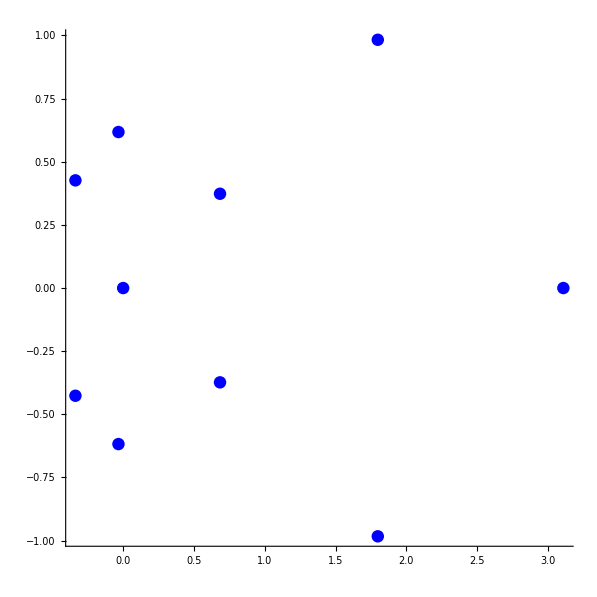

```mathematica
aForm[$theFunction]
 theSings=$theSingularList;
thePoles=$theSingularList[[$poleIndexes]];
theRingList=Abs[#]&/@ theSings;

singG=Graphics@{PointSize[0.015],Blue,Point@(ReIm@#&/@ theSings)};
poleG=Graphics@{PointSize[.015],Red,Point@(ReIm@#&/@ thePoles)};
singularPerimetersG=Graphics@MapThread[Circle[ReIm@#1,#2]&,{theSings,$minRadiusArray}];
nearestDistancesG=MapThread[{Dashed,Circle[ReIm@#1,#2]}&,{theSings,$nearestDistanceArray}];


(*annularRegionsG=Graphics@MapThread[{EdgeForm[],FaceForm[{Opacity[0.25],#1}],Annulus[{0,0},#2]}&,{annularColors[[1;;7]],theRingList[[All,2]]}];*)
theRingsG=Graphics@{Circle[{0,0},#]&/@ theRingList};
domain1G={Dashed,Red,Circle[{0,0},$nearestDistanceArray[[1]]]};

Show[{singG,poleG(*Graphics@{nearestDistancesG(*,domain1G*)}*)},Axes->True,AspectRatio->1,PlotRange->Abs[$theSingularList[[-1]]]+2]
```

### Check all singular points for removable singularities

```mathematica
PrintTemporary["Singular index: ",Dynamic@indexName];
removableList=Table[ 
indexName=index;

 dataList=Import[seriesFileName[$theTestCase,index]];
baseBranchTypeArray={};
baseSeriesMIVPTable={};
If[Length@dataList==9,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence}=dataList;
,
If[Length@dataList==10,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray}=dataList;
,
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=dataList;
];
];
If[MemberQ[Length@#&/@ baseRemovableList[[All,2]],_?Positive],
Print["Found removable at singular index ",index];
];
{index,baseRemovableList},
{index,1,Length@$theSingularList}
];
```

## Import annular table with monodromies previously computed with ch 2 notebook

```mathematica
If[FileExistsQ[annularTableWithMonodromiesFileName[$theTestCase]], 
{annulusTable,annulusTableR,annulusTableReport}=Import[annularTableWithMonodromiesFileName[$theTestCase]];
annularResidueTable={#[[1]],#[[2]],#[[3]],#[[4]],#[[6]]}&/@ annulusTableR;
annularResidueReport=Prepend[annularResidueTable,{"a_n Index","s_n Index","a_n or s_n",Column[{"monodromy","radius"},Alignment->Center],"Monodromy"}];

monodromyGridReport=Style[Labeled[Grid[annularResidueReport,Dividers->{{{True}},{True,True,{False},True}}],Style[$theTestCase,14,Bold,Black],Top],10];
Print[monodromyGridReport];
,
Print[Style[annularTableWithMonodromiesFileName[$theTestCase]<>" not found during import.",Red]];
singFlag3=False;
];
```

a_n Index | s_n Index | a_n or s_n | monodromy
radius | Monodromy
  | 1 | 0 | 0.166667 | {{1},{2},{3}}
1 |   | {0.,0.5} | 0.25 | {{1},{2},{3}}
  | 2 | 0.-0.5 ⅈ | 0.158927 | {{2,3},{1}}
  | 3 | 0.+0.5 ⅈ | 0.158927 | {{2,3},{1}}
2 |   | {0.5,0.624261} | 0.562131 | {{1},{2},{3}}
  | 4 | -0.477196-0.402475 ⅈ | 0.162353 | {{2,3},{1}}
  | 5 | -0.477196+0.402475 ⅈ | 0.162353 | {{2,3},{1}}
3 |   | {0.624261,0.954195} | 0.789228 | {{1,3,2}}
  | 6 | 0.199211-0.933168 ⅈ | 0.158927 | {{1,2},{3}}
  | 7 | 0.199211+0.933168 ⅈ | 0.158927 | {{1,2},{3}}
4 |   | {0.954195,1.33333} | 1.14376 | {{1,3,2}}
  | 8 | 1.33333 | 0.205603 | {{1},{2},{3}}
5 |   | {1.33333,1.7028} | 1.51807 | {{1,3,2}}
  | 9 | 1.61132-0.550616 ⅈ | 0.205603 | {{2,3},{1}}
  | 10 | 1.61132+0.550616 ⅈ | 0.205603 | {{1,3},{2}}
6 |   | {1.7028,2.7028} | 2.2028 | {{1},{2},{3}}testCase0017

## Section 3: Select base singular point

```mathematica
baseSingularIndex=2

baseSeriesFlag=False;

 If[TrueQ@FileExistsQ@seriesFileName[$theTestCase,baseSingularIndex],
baseSeriesFlag=True;
baseSingularPoint=$theSingularList[[baseSingularIndex]]; 
baseRadius=$minRadiusArray[[baseSingularIndex]];
Print["baseSingularPoint: ",$theSingularList[[baseSingularIndex]]//N];
Print["Importing file: ",seriesFileName[$theTestCase,baseSingularIndex]];
dataList=Import[seriesFileName[$theTestCase,baseSingularIndex]];
Print["Len dataList: ",Length@dataList];
baseBranchTypeArray={};
baseSeriesMIVPTable={};
{newSingularIndex,newSing,baseCycleMetric,basePoleList,newConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=dataList;
(*
 report data in file:
*)
Print["baseRemovableList: ",baseRemovableList];
Print["baseSeries precision: ",Precision@baseSeries];
Print["baseSheetLinks: ",baseSheetLinks];
Print["Chosen singular point: ",N[baseSingularPoint,25]];
Print["File singular point:   ",N[newSing,25]];
(*Print["Base sheet min lengths: ",baseMinLengths];*)
Print["Base poleList:          ",basePoleList];
(*
 consider baseSheetLinks={{1,{1}},{1,{2}},{1,{3}},{2,{4,5}}}
baseSeriesMIVPTable={{1,{{1,1}}},{1,{{1,2}}},{1,{{1,3}}},{2,{{1,4},{2,5}}}}
then first series in {1,{1,1}} is first sorted mIVP value,
   for {2,{{1,4},{2,5}}} then series #4 is fourth mIVP value and series 5 is fifth mIVP value
*)
Print["baseSeriesMIVPTable:        ",baseSeriesMIVPTable];

(*
 check for removable singular points
*)
If[Flatten[baseRemovableList[[All,2]]]!={},
Print[Style["Found removable singular points: ",Red],baseRemovableList];
];


Print["TotalTerms: ",Length@#&/@baseSeries];
baseFun[z_]=baseSeries;
Print["Precision of base series: ",Precision@#&/@baseFun[z]];
basePoleFlag=False;
baseConjList=newConjList;
Print["base conj list: ",baseConjList];
For[i=1,i<=Length@basePoleList,i++,
If[Length@basePoleList[[i,2]]!=0,
Print[Style["Found pole on sheet ",Red],i];
basePoleFlag=True;
];
];

singularSequence=baseSingSequence;
theSingularRegions=Abs[baseSingularPoint-#]&/@ $theSingularList[[singularSequence]];
Print[baseSeries[[All,1;;4]]//N//MatrixForm];
Print[baseBranchTypeArray];
Print[baseSeriesMIVPTable];
,
Print[Style[seriesFileName[$theTestCase,baseSingularIndex]<>" not found.  See Chapter 3 notebook.",Red]];
];
```

2

baseSingularPoint: 0.-0.5 ⅈ

Importing file: D:\algFunctionBook\data\testCase0017\2series.m

Len dataList: 11

baseRemovableList: {{1,{}},{2,{}},{3,{}}}

baseSeries precision: 961.873

baseSheetLinks: {{2,{1,2}},{1,{3}}}

Chosen singular point: -0.5 ⅈ

File singular point:   -0.5 ⅈ

Base poleList:          {{1,{}},{2,{}},{3,{}}}

baseSeriesMIVPTable:        {{2,{{1,2},{2,3}}},{1,{{3,1}}}}

TotalTerms: {512,512,512}

Precision of base series: {988.073,988.073,961.873}

base conj list: {2,2,1}

((-0.820847-0.953157 ⅈ) √z-(0.132376+0.102008 ⅈ) z+(0.526119-0.27684 ⅈ) z^(3/2)+(0.464052-0.297023 ⅈ) z^2
(0.820847+0.953157 ⅈ) √z-(0.132376+0.102008 ⅈ) z-(0.526119-0.27684 ⅈ) z^(3/2)+(0.464052-0.297023 ⅈ) z^2
(-2.30137-4.13699 ⅈ)-(11.0357-1.33894 ⅈ) z-(1.50334-21.661 ⅈ) z^2+(39.9224-0.170224 ⅈ) z^3)

{{V_2^1,{1,2}},{T,{3}}}

{{2,{{1,2},{2,3}}},{1,{{3,1}}}}

## Section 4: Obtain Root Test results:

### Section 4.1: Compile root test data using Minimize function and compute comparison sequence

```mathematica
If[baseSeriesFlag,
{theTypeTable,baseSheetNumbers,seriesLengths,theTypeLinks}=getSeriesTypes[baseSeries,baseSheetLinks,baseRemovableList];
 {rootTestData,rootTestReport,rootTestHeader,graphicsData}=getRootTestResultsStd[baseSeries,baseSheetLinks,baseSheetNumbers,theTypeTable,seriesLengths,baseSingularPoint,singularSequence,$theSingularList,baseSingularIndex,baseConjList,$theTestCase];

(*Print["Exporting root test results to "<>rootTestReportFileName[$theTestCase,baseSingularIndex]];*)
Export[rootTestReportFileName[$theTestCase,baseSingularIndex],{rootTestData,rootTestReport,rootTestHeader,graphicsData}];

estCLSPs=rootTestData[[All,6]];
Print[rootTestReport];
(*
 generate comparisonSequence for this singular point
*)
clspList=rootTestData[[All,6]];
 comparisonSequenceMaxIndex=(Max@(Position[baseSingSequence,x_/;x==#]&/@ clspList//Flatten))+5;
If[comparisonSequenceMaxIndex>Length@$theSingularList,
comparisonSequenceMaxIndex=Length@$theSingularList;
];
comparisonSequence=baseSingSequence[[1;;comparisonSequenceMaxIndex]];
Print["comparisonSequence: ",comparisonSequence];
,
Print[Style[seriesFileName[$theTestCase,baseSingularIndex]<>" not found.  See Chapter 3 notebook for computing power expansions at a singular point.",Red]];
];
```

Analyzing base sheet for cycle  1

Best fit function for this branch:

0.480435+7.89024 x-121.417 x^2+1446.29 x^3

Analyzing base sheet for cycle  2

Best fit function for this branch:

0.4815+2.89458 x-219.701 x^2+3336.35 x^3

testCase0017 Root Test results
Singular Index 2
Index | Sheet | Type | Cycle Size | Root Test | est. CLSP | Series size
1 | 1 | V_2^1 | 2 | 0.48044 | 6 | 512
2 | 3 | T | 1 | 0.4815 | 6 | 512

comparisonSequence: {2,6,4,1,3,5,8}

#### Manual computation of theTypeTable

```mathematica
(*
 uniquely name each branch
*)
 baseSheetNumbers=Min@#& /@(#[[2]]&/@baseSheetLinks);

seriesLengths=Length[#]&/@ baseSeries[[baseSheetNumbers]];
 theExpList= Exponent[#,z,List]&/@ baseSeries[[baseSheetNumbers]];
minExpList=Min[#]& /@ (Select[#,#!=0&]&/@ theExpList);
cycleTypes=baseSheetLinks[[All,1]];

multiType[a_Integer,b_String]:=StringTemplate["_(`1`)`2`"][ToString@a,b];
newType[a_Integer,b_String,c_Integer,d_Integer]:=StringTemplate["_(`1`)(`2`)_(`3`)^(`4`)"][ToString@a,b,ToString@c,ToString@d];
multiBranchType[a_String,b_Integer,c_Integer]:=StringTemplate["(`1`)_(`2`)^(`3`)"][ToString@a,ToString@b,ToString@c];
theLType[a_String,b_Integer]:=StringTemplate["(`1`)_(`2`)"][a,ToString@b];

 (* 
pick out Taylor series
*)
typeTable=Table[
minE=minExpList[[i]];
If[cycleTypes[[i]]==1,
If[MemberQ[baseRemovableList[[All,1]],baseSheetNumbers[[i]]],
type="E";
,
If[minE<0,
theN=Numerator[minE];
(*type=Subscript["L", ToString[theN]];*)
type=theLType["L",theN];
,
type="T";
];
];
,
theD=Denominator[minE];
theN=Numerator[minE];
If[minE>0,
If[minE>1,
(*type=Subscript[F, ToString[theD]]^ToString[theN];*)
type=multiBranchType["F",cycleTypes[[i]],theN];
,
(*type=Subscript[V, ToString[theD]]^ToString[theN];*)
type=multiBranchType["V",cycleTypes[[i]],theN];
];
,
(*type=Subscript[P, ToString[theD]]^ToString[theN];*)
type=multiBranchType["P",cycleTypes[[i]],theN];
];
];
type,
{i,1,Length@baseSheetNumbers}
];
Print["typeTable",typeTable];
theTally=Tally[typeTable];
mVals=Select[theTally,#[[2]]>1&];

For[j=1,j<=Length@mVals,j++,
typeLoc=Flatten@Position[typeTable,x_/;x==mVals[[j,1]]];
For[i=1,i<=Length@typeLoc,i++,
typeTable[[typeLoc[[i]]]]=ToString[i]<>typeTable[[typeLoc[[i]]]];
(*typeTable[[typeLoc[[i]]]]=multiType[i,typeTable[[typeLoc[[i]]]]];*)
];
];
```

#### Manual computation of Root Test

```mathematica
(*
 now fit data
*)
cycleBaseSheets=baseSheetLinks[[All,2,1]];

plotFlag=True;
fitType=2;
cTableType=2;
startTerms=10;

totalSheets=Length@baseConjList;
graphicsData={};

PrintTemporary["Analyzing base sheet for cycle  ",Dynamic@theIndex];
at=AbsoluteTiming[
dataTable=Table[
theIndex=theBranchNum;
seriesType=theTypeTable[[theBranchNum]];
theSeriesNum=cycleBaseSheets[[theBranchNum]];
cycleType=baseSheetLinks[[theBranchNum,1]];
seriesLength=Length@baseSeries[[theSeriesNum]];
theexp=Exponent[baseSeries[[theSeriesNum]],z,List];
lcm=LCM@@(Denominator@theexp);
             numVals=lcm theexp;
clist=Coefficient[baseSeries[[theSeriesNum]],z,theexp];

cTable=Switch[cTableType,
1,
Table[
{1/k,N[1/(Abs[clist[[k]]]^(cycleType/numVals[[k]])),25]},
{k,15,Length@clist}],
2,Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^(cycleType/numVals[[k]])),25]},
{k,15,Length@clist}]
];

(*Print["cTable Len: ",Length@cTable];*)
lp1=ListPlot[cTable,PlotStyle->{PointSize[0.005]},AxesOrigin->{0,0}];

(* 
         start of update
 *)
dataVals=cTable[[startTerms;;]];
plotXStart=cTable[[-1,1]];
plotXEnd=cTable[[1,1]];
endTerms=Length@cTable;

linearLine=c0+c1 x/. Minimize[{Total[(#[[2]]-(c0+c1 #[[1]]))&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];


linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};
fitSet={linearLine,quadraticLine,cubicLine};

bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
Print["Best fit function for this branch: "];
Switch[bestFitPos,1,Print[linearLine//N],2,Print[quadraticLine//N],3,Print[cubicLine//N]];
rTest=Switch[bestFitPos,1,linearLine/.x->0,2,quadraticLine/.x->0,3,cubicLine/.x->0];
(*
rTest=quadraticLine/.x->0//N;*)
fitResults=rTest;
(*Print["Best R from minimize function: ",rTest//N];*)

linearPlot=Plot[linearLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
quadraticPlot=Plot[quadraticLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
cubicPlot=Plot[cubicLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0045],Red}];
plotSet={linearPlot,quadraticPlot,cubicPlot};


(*          end of update *)
(*
 try getLimLine or LimLine2
*)

If[plotFlag,
(*fitValueG=Graphics@{Black,PointSize[0.01],Point@{0,fitResults//N}};*)
fitValueG=Graphics@{Green,PointSize[0.01],Point@{0,fitResults//N}};

plotLabel=Column[{Row[{Style[theTestCase,16,Bold,Black],Style[" Root Test Results",16,Black,Bold]}],Row[{Style["(",Bold,Black,16],Style[baseSingularIndex,Bold,Black,16],Style[": ",16,Bold,Black],Style[seriesType,16,Black,Bold],Style[")",Bold,Black,16]}]},Alignment->Center];

lp1=ListPlot[cTable,PlotStyle->{PointSize[0.005]},Frame->{{True,False},{True,False}},
FrameLabel->{Style[,14,Bold,Black],Rotate[Style["1/(|SubscriptBox[a, k]SuperscriptBox[|, FractionBox[c, SubscriptBox[m, k]]])",16,Bold,Black],-Pi/2]},AxesOrigin->{0,0}];
thePlotRange=Options[lp1,PlotRange][[1,2]];

xCoord=Plus@@thePlotRange[[1]]/2;
yCoord=(Plus@@thePlotRange[[2]]/2);
AppendTo[graphicsData,{lp1,plotSet[[bestFitPos]],"",fitValueG,Rationalize[fitResults,0],plotLabel,cTable,dataVals,plotXEnd//N}];
];
theSummary={
theBranchNum,
baseConjList[[theBranchNum]],
Rationalize[fitResults,0]
};
theSummary,
{theBranchNum,1,Length@cycleBaseSheets}
];
]

(*
 generate convergence report without CLSPs
*)

fitRadius=graphicsData[[All,5]];

rootTestResults=MapThread[{#1,#2,#3,#4[[1]],#5,#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];
rootTestReport1=MapThread[{#1,#2,#3,#4[[1]],#5,#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];

rootTestReport=Prepend[rootTestReport1,{"Index","Sheet","Type","Size","Root Test","Series size"}];
(*
 compute est CLSP
*)
theDistanceList=Abs[baseSingularPoint-#]&/@ theSingularList[[singularSequence]];
(*absNearList=Abs@theNearestList;*)
theNearList=Flatten[NearestTo[#,1][theDistanceList]&/@ rootTestResults[[All,5]]];


nearestIndexes=Flatten@(Position[theDistanceList,x_/;Abs[x-#]<10^-15]&/@theNearList)[[All,1]]
estCLSPIndexes=singularSequence[[nearestIndexes]];

estCLSPs=MapThread[{#1,#2}&,{Range[Length@rootTestResults],estCLSPIndexes}];
 (*
 generate convergence report with est. CLSPs
*)
rootTestResults2=MapThread[{#1,#2,#3,#4[[1]],SetPrecision[#5,5],#7[[2]],#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths,estCLSPs}];

rootTestReport2=Prepend[rootTestResults2,{"Index","Sheet","Type","Cycle Size","Root Test","est. CLSP","Series size"}];

rootTestReportHeader=Column[{Row[{Style[theTestCase,16,Bold,Black],Style[" Root Test results",16,Black,Bold]}],Row[{Style["Singular Index ",Bold,Black,16],Style[baseSingularIndex,16,Black,Bold]}]},Alignment->Center];

Column[{rootTestReportHeader,Grid[rootTestReport2,Dividers->{{{True}},{True,True,{False},True}}]},Alignment->Center]
```

Best fit function for this branch:

0.644461+36.469 x-1565.34 x^2+66859.8 x^3

Best fit function for this branch:

0.506726+23.7717 x-896.433 x^2+34289. x^3

Best fit function for this branch:

0.167678+5.84509 x-66.6613 x^2+1406.19 x^3

Best fit function for this branch:

0.167468+3.84996 x-41.5677 x^2+621.129 x^3

Best fit function for this branch:

1.09593+9.55433 x-170.686 x^2+2032.84 x^3

{10.2617,Null}

{31,7,2,2,118}

Test Case 1 Root Test results
Singular Index 1
Index | Sheet | Type | Cycle Size | Root Test | est. CLSP | Series size
1 | 1 | F_5^16 | 5 | 0.64446 | 31 | 1987
2 | 6 | F_4^9 | 4 | 0.50673 | 7 | 2022
3 | 10 | F_3^4 | 3 | 0.16768 | 2 | 1017
4 | 13 | V_2^1 | 2 | 0.16747 | 2 | 1024
5 | 15 | T | 1 | 1.0959 | 118 | 1024

### Generate plot of selected Root Test

```mathematica
pIndex=2
ImagePad[Show[graphicsData[[pIndex,{1,2,4}]],AxesOrigin->{0,0},ImageSize->500],20]
```

2

-Graphics-

### Section 4.2: Checking if comparison file set is available for import

Checking for series files {2,6,4,1,3,5,8}

All files found

All files needed for continuation analysis found!

(1+4 z^2)+(5/2+3/4 z) w^2+(z-3/4 z^2) w^3

Singular points graphics:

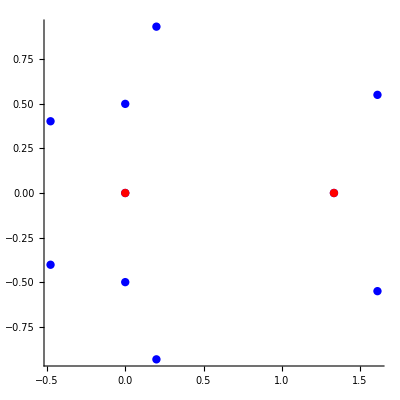

```mathematica
If[checkContinuationFiles[baseSingularIndex,rootTestData,singularSequence],
Print["All files needed for continuation analysis found!"];
,
Print[Style["Some files needed for continuation analysis are missing!",Red]];
];
(*Print["SingularPoints: "];
Grid@MapThread[{#1,#2}&,{Range@Length@singularSequence,$theSingularList[[singularSequence]]//N}]
*)
aForm[$theFunction]
 theSings=$theSingularList;
thePoles=$theSingularList[[$poleIndexes]];
theRingList=Abs[#]&/@ theSings;

singG=Graphics@{PointSize[0.015],Blue,Point@(ReIm@#&/@ theSings)};
poleG=Graphics@{PointSize[.015],Red,Point@(ReIm@#&/@ thePoles)};
singularPerimetersG=Graphics@MapThread[Circle[ReIm@#1,#2]&,{theSings,$minRadiusArray}];
nearestDistancesG=MapThread[{Dashed,Circle[ReIm@#1,#2]}&,{theSings,$nearestDistanceArray}];


(*annularRegionsG=Graphics@MapThread[{EdgeForm[],FaceForm[{Opacity[0.25],#1}],Annulus[{0,0},#2]}&,{annularColors[[1;;7]],theRingList[[All,2]]}];*)
theRingsG=Graphics@{Circle[{0,0},#]&/@ theRingList};
domain1G={Dashed,Red,Circle[{0,0},$nearestDistanceArray[[1]]]};
Print["Singular points graphics: "];
Show[{singG,poleG(*Graphics@{nearestDistancesG(*,domain1G*)}*)},Axes->True,AspectRatio->1,PlotRange->Abs[$theSingularList[[-1]]]+2]
```

### Section 4.3: Compile root test data using Minimize function and log[10,x] for very large R values for f_{25} and very small values of R for f_{27}

```mathematica
{theTypeTable,baseSheetNumbers,seriesLengths,theTypeLinks}=getSeriesTypes[baseSeries,baseSheetLinks,baseRemovableList];


{rootTestData,rootTestReport,rootTestHeader,graphicsData}=getRootTestResultsStd[baseSeries,baseSheetLinks,baseSheetNumbers,theTypeTable,seriesLengths,baseSingularPoint,singularSequence,$theSingularList,baseSingularIndex,baseConjList,$theTestCase];




Grid[rootTestReport2,Dividers->{{{True}},{True,True,{False},True}}]
Export[rootTestReportFileName[$theTestCase,baseSingularIndex],{rootTestData,rootTestReport,rootTestHeader,graphicsData}];

estCLSPs=rootTestData[[All,6]]
```

Analyzing base sheet for cycle  1

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  2

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  3

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  4

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  5

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  6

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  7

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  8

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  9

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  10

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  11

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  12

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  13

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  14

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  15

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  16

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  17

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  18

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  19

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  20

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  21

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  22

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  23

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  24

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  25

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  26

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  27

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  28

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  29

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  30

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  31

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  32

Best fit function for this branch:

-1.4921×10^-15+7.60103×10^-13 x+2.1419×10^-11 x^2-2.06382×10^-10 x^3

Analyzing base sheet for cycle  33

Best fit function for this branch:

-1.48773×10^-15+7.60627×10^-13 x+2.15562×10^-11 x^2-2.07898×10^-10 x^3

Generator
Index | Type | Size | Conjugate
Indexes | R^* | Series
size | estCLSP
1 | 1T | 1 | {1} | 1.0549×10^-35 | 256 | 484
2 | 2T | 1 | {2} | 1.0549×10^-35 | 256 | 484
3 | 3T | 1 | {3} | 1.0549×10^-35 | 256 | 484
4 | 4T | 1 | {4} | 1.831×10^-35 | 256 | 484
5 | 5T | 1 | {5} | 1.0548×10^-35 | 256 | 484
6 | 6T | 1 | {6} | 1.0571×10^-35 | 256 | 484
7 | 7T | 1 | {7} | 2.1142×10^-35 | 256 | 484
8 | 8T | 1 | {8} | 1.0549×10^-35 | 256 | 484
9 | 9T | 1 | {9} | 1.0549×10^-35 | 256 | 484
10 | 10T | 1 | {10} | 1.0549×10^-35 | 256 | 484
11 | 11T | 1 | {11} | 4.9989×10^-46 | 256 | 484
12 | 12T | 1 | {12} | 4.9989×10^-46 | 256 | 484
13 | 13T | 1 | {13} | 1.831×10^-35 | 256 | 484
14 | 14T | 1 | {14} | 1.0549×10^-35 | 256 | 484
15 | 15T | 1 | {15} | 1.0549×10^-35 | 256 | 484
16 | 16T | 1 | {16} | 1.0548×10^-35 | 256 | 484
17 | 17T | 1 | {17} | 1.0571×10^-35 | 256 | 484
18 | 18T | 1 | {18} | 1.0571×10^-35 | 256 | 484
19 | 19T | 1 | {19} | 1.0548×10^-35 | 256 | 484
20 | 20T | 1 | {20} | 1.0549×10^-35 | 256 | 484
21 | 21T | 1 | {21} | 1.0549×10^-35 | 256 | 484
22 | 22T | 1 | {22} | 1.831×10^-35 | 256 | 484
23 | 23T | 1 | {23} | 1.0549×10^-35 | 256 | 484
24 | 24T | 1 | {24} | 1.0549×10^-35 | 256 | 484
25 | 25T | 1 | {25} | 1.0549×10^-35 | 256 | 484
26 | 26T | 1 | {26} | 2.1142×10^-35 | 256 | 484
27 | 27T | 1 | {27} | 1.0571×10^-35 | 256 | 484
28 | 28T | 1 | {28} | 1.0548×10^-35 | 256 | 484
29 | 29T | 1 | {29} | 1.831×10^-35 | 256 | 484
30 | 30T | 1 | {30} | 1.0549×10^-35 | 256 | 484
31 | 31T | 1 | {31} | 1.0549×10^-35 | 256 | 484
32 | 32T | 1 | {32} | 1.0549×10^-35 | 256 | 484
33 | V_2^1 | 2 | {33,34} | 1.0587×10^-35 | 257 | 484

{484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484,484}

### Section 4.4: Generate plot of selected root test

```mathematica
pIndex=4
ImagePad[Show[graphicsData[[pIndex,{1,2,4}]],AxesOrigin->{0,0},ImageSize->500],20]
```

4

-Graphics-

### Section 4.5: Compile root test data using Minimize function and log[10,x] for very large R values for f_{25} and very small values of R for f_{27}

```mathematica
Length@rootTestData
```

33

```mathematica
{theTypeTable,baseSheetNumbers,seriesLengths,theTypeLinks}=getSeriesTypes[baseSeries,baseSheetLinks,baseRemovableList];


{rootTestData,rootTestReport,rootTestHeader,graphicsData}=getRootTestResultsStd[baseSeries,baseSheetLinks,baseSheetNumbers,theTypeTable,seriesLengths,baseSingularPoint,singularSequence,$theSingularList,baseSingularIndex,baseConjList,$theTestCase];




Grid[rootTestReport2,Dividers->{{{True}},{True,True,{False},True}}]
Export[rootTestReportFileName[$theTestCase,baseSingularIndex],{rootTestData,rootTestReport,rootTestHeader,graphicsData}];

estCLSPs=rootTestData[[All,6]]
```

Analyzing base sheet for cycle  1

Best fit function for this branch:

0.475273+0.0494979 x+0.0225229 x^2-2.29644 x^3

Analyzing base sheet for cycle  2

Best fit function for this branch:

0.46237+3.99679 x-50.9626 x^2+541.044 x^3

Analyzing base sheet for cycle  3

Best fit function for this branch:

0.455686+4.39372 x-95.6376 x^2+1314.64 x^3

Analyzing base sheet for cycle  4

Best fit function for this branch:

0.456119+4.08703 x-50.4959 x^2+602.64 x^3

Grid[rootTestReport2,Dividers→{{{True}},{True,True,{False},True}}]

{7,21,17,17}

#### Manual computation of theTypeTable

```mathematica
(*
 uniquely name each branch
*)
 baseSheetNumbers=Min@#& /@(#[[2]]&/@baseSheetLinks);

seriesLengths=Length[#]&/@ baseSeries[[baseSheetNumbers]];
 theExpList= Exponent[#,z,List]&/@ baseSeries[[baseSheetNumbers]];
minExpList=Min[#]& /@ (Select[#,#!=0&]&/@ theExpList);
cycleTypes=baseSheetLinks[[All,1]];

multiType[a_Integer,b_String]:=StringTemplate["_(`1`)`2`"][ToString@a,b];
newType[a_Integer,b_String,c_Integer,d_Integer]:=StringTemplate["_(`1`)(`2`)_(`3`)^(`4`)"][ToString@a,b,ToString@c,ToString@d];
multiBranchType[a_String,b_Integer,c_Integer]:=StringTemplate["(`1`)_(`2`)^(`3`)"][ToString@a,ToString@b,ToString@c];
theLType[a_String,b_Integer]:=StringTemplate["(`1`)_(`2`)"][a,ToString@b];

 (* 
pick out Taylor series
*)
typeTable=Table[
minE=minExpList[[i]];
If[cycleTypes[[i]]==1,
If[MemberQ[baseRemovableList[[All,1]],baseSheetNumbers[[i]]],
type="E";
,
If[minE<0,
theN=Numerator[minE];
(*type=Subscript["L", ToString[theN]];*)
type=theLType["L",theN];
,
type="T";
];
];
,
theD=Denominator[minE];
theN=Numerator[minE];
If[minE>0,
If[minE>1,
(*type=Subscript[F, ToString[theD]]^ToString[theN];*)
type=multiBranchType["F",cycleTypes[[i]],theN];
,
(*type=Subscript[V, ToString[theD]]^ToString[theN];*)
type=multiBranchType["V",cycleTypes[[i]],theN];
];
,
(*type=Subscript[P, ToString[theD]]^ToString[theN];*)
type=multiBranchType["P",cycleTypes[[i]],theN];
];
];
type,
{i,1,Length@baseSheetNumbers}
];
Print["typeTable",typeTable];
theTally=Tally[typeTable];
mVals=Select[theTally,#[[2]]>1&];

For[j=1,j<=Length@mVals,j++,
typeLoc=Flatten@Position[typeTable,x_/;x==mVals[[j,1]]];
For[i=1,i<=Length@typeLoc,i++,
typeTable[[typeLoc[[i]]]]=ToString[i]<>typeTable[[typeLoc[[i]]]];
(*typeTable[[typeLoc[[i]]]]=multiType[i,typeTable[[typeLoc[[i]]]]];*)
];
];
```

#### Manual computation of Root Test

```mathematica
(*
 now fit data
*)
cycleBaseSheets=baseSheetLinks[[All,2,1]];

plotFlag=True;
fitType=2;
cTableType=2;
startTerms=10;

totalSheets=Length@baseConjList;
graphicsData={};

PrintTemporary["Analyzing base sheet for cycle  ",Dynamic@theIndex];
at=AbsoluteTiming[
dataTable=Table[
theIndex=theBranchNum;
seriesType=theTypeTable[[theBranchNum]];
theSeriesNum=cycleBaseSheets[[theBranchNum]];
cycleType=baseSheetLinks[[theBranchNum,1]];
seriesLength=Length@baseSeries[[theSeriesNum]];
theexp=Exponent[baseSeries[[theSeriesNum]],z,List];
lcm=LCM@@(Denominator@theexp);
             numVals=lcm theexp;
clist=Coefficient[baseSeries[[theSeriesNum]],z,theexp];

cTable=Switch[cTableType,
1,
Table[
{1/k,N[1/(Abs[clist[[k]]]^(cycleType/numVals[[k]])),25]},
{k,15,Length@clist}],
2,Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^(cycleType/numVals[[k]])),25]},
{k,15,Length@clist}]
];

(*Print["cTable Len: ",Length@cTable];*)
lp1=ListPlot[cTable,PlotStyle->{PointSize[0.005]},AxesOrigin->{0,0}];

(* 
         start of update
 *)
dataVals=cTable[[startTerms;;]];
plotXStart=cTable[[-1,1]];
plotXEnd=cTable[[1,1]];
endTerms=Length@cTable;

linearLine=c0+c1 x/. Minimize[{Total[(#[[2]]-(c0+c1 #[[1]]))&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];


linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};
fitSet={linearLine,quadraticLine,cubicLine};

bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
Print["Best fit function for this branch: "];
Switch[bestFitPos,1,Print[linearLine//N],2,Print[quadraticLine//N],3,Print[cubicLine//N]];
rTest=Switch[bestFitPos,1,linearLine/.x->0,2,quadraticLine/.x->0,3,cubicLine/.x->0];
(*
rTest=quadraticLine/.x->0//N;*)
fitResults=rTest;
(*Print["Best R from minimize function: ",rTest//N];*)

linearPlot=Plot[linearLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
quadraticPlot=Plot[quadraticLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
cubicPlot=Plot[cubicLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0045],Red}];
plotSet={linearPlot,quadraticPlot,cubicPlot};


(*          end of update *)
(*
 try getLimLine or LimLine2
*)

If[plotFlag,
(*fitValueG=Graphics@{Black,PointSize[0.01],Point@{0,fitResults//N}};*)
fitValueG=Graphics@{Green,PointSize[0.01],Point@{0,fitResults//N}};

plotLabel=Column[{Row[{Style[theTestCase,16,Bold,Black],Style[" Root Test Results",16,Black,Bold]}],Row[{Style["(",Bold,Black,16],Style[baseSingularIndex,Bold,Black,16],Style[": ",16,Bold,Black],Style[seriesType,16,Black,Bold],Style[")",Bold,Black,16]}]},Alignment->Center];

lp1=ListPlot[cTable,PlotStyle->{PointSize[0.005]},Frame->{{True,False},{True,False}},
FrameLabel->{Style[,14,Bold,Black],Rotate[Style["1/(|SubscriptBox[a, k]SuperscriptBox[|, FractionBox[c, SubscriptBox[m, k]]])",16,Bold,Black],-Pi/2]},AxesOrigin->{0,0}];
thePlotRange=Options[lp1,PlotRange][[1,2]];

xCoord=Plus@@thePlotRange[[1]]/2;
yCoord=(Plus@@thePlotRange[[2]]/2);
AppendTo[graphicsData,{lp1,plotSet[[bestFitPos]],"",fitValueG,Rationalize[fitResults,0],plotLabel,cTable,dataVals,plotXEnd//N}];
];
theSummary={
theBranchNum,
baseConjList[[theBranchNum]],
Rationalize[fitResults,0]
};
theSummary,
{theBranchNum,1,Length@cycleBaseSheets}
];
]

(*
 generate convergence report without CLSPs
*)

fitRadius=graphicsData[[All,5]];

rootTestResults=MapThread[{#1,#2,#3,#4[[1]],#5,#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];
rootTestReport1=MapThread[{#1,#2,#3,#4[[1]],#5,#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];

rootTestReport=Prepend[rootTestReport1,{"Index","Sheet","Type","Size","Root Test","Series size"}];
(*
 compute est CLSP
*)
theDistanceList=Abs[baseSingularPoint-#]&/@ theSingularList[[singularSequence]];
(*absNearList=Abs@theNearestList;*)
theNearList=Flatten[NearestTo[#,1][theDistanceList]&/@ rootTestResults[[All,5]]];


nearestIndexes=Flatten@(Position[theDistanceList,x_/;Abs[x-#]<10^-15]&/@theNearList)[[All,1]]
estCLSPIndexes=singularSequence[[nearestIndexes]];

estCLSPs=MapThread[{#1,#2}&,{Range[Length@rootTestResults],estCLSPIndexes}];
 (*
 generate convergence report with est. CLSPs
*)
rootTestResults2=MapThread[{#1,#2,#3,#4[[1]],SetPrecision[#5,5],#7[[2]],#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths,estCLSPs}];

rootTestReport2=Prepend[rootTestResults2,{"Index","Sheet","Type","Cycle Size","Root Test","est. CLSP","Series size"}];

rootTestReportHeader=Column[{Row[{Style[theTestCase,16,Bold,Black],Style[" Root Test results",16,Black,Bold]}],Row[{Style["Singular Index ",Bold,Black,16],Style[baseSingularIndex,16,Black,Bold]}]},Alignment->Center];

Column[{rootTestReportHeader,Grid[rootTestReport2,Dividers->{{{True}},{True,True,{False},True}}]},Alignment->Center]
```

Best fit function for this branch:

0.644461+36.469 x-1565.34 x^2+66859.8 x^3

Best fit function for this branch:

0.506726+23.7717 x-896.433 x^2+34289. x^3

Best fit function for this branch:

0.167678+5.84509 x-66.6613 x^2+1406.19 x^3

Best fit function for this branch:

0.167468+3.84996 x-41.5677 x^2+621.129 x^3

Best fit function for this branch:

1.09593+9.55433 x-170.686 x^2+2032.84 x^3

{10.2617,Null}

{31,7,2,2,118}

Test Case 1 Root Test results
Singular Index 1
Index | Sheet | Type | Cycle Size | Root Test | est. CLSP | Series size
1 | 1 | F_5^16 | 5 | 0.64446 | 31 | 1987
2 | 6 | F_4^9 | 4 | 0.50673 | 7 | 2022
3 | 10 | F_3^4 | 3 | 0.16768 | 2 | 1017
4 | 13 | V_2^1 | 2 | 0.16747 | 2 | 1024
5 | 15 | T | 1 | 1.0959 | 118 | 1024

### Generate plot of selected Root Test

```mathematica
pIndex=4
ImagePad[Show[graphicsData[[pIndex,{1,2,4}]],AxesOrigin->{0,0},ImageSize->500],20]
```

4

-Graphics-

## Section 5: Series Comparison test (confirm comparisonSequence has been generated in Section 4)

```mathematica
(*
 comparisonSequence
*)
comparisonSequence
```

{1,2,3,4,5,6,7,8,9}

#### Section 5.1: Select diagnostic test

```mathematica
segmentMenu=Column[{Style["Comparison Test diagnostics:",16,Bold,Black,Underlined],
Row[{Checkbox[Dynamic[$comparisonTestFlag]],Spacer[3],Style["ComparisonTest ",Black,Bold],Spacer[63],Checkbox[Dynamic[$polishSeriesFlag]],Spacer[3],Style["polishBranchValues",Black,Bold]}],
Row[{Checkbox[Dynamic[$getIntegrationDataFlag]],Spacer[3],Style["getIntegrationData ",Black,Bold],Spacer[35],Checkbox[Dynamic[$getBranchContinuationsFlag]],Spacer[3],Style["getBranchContinuations",Black,Bold]}]



},Frame->True,FrameStyle->Thick]
```

Comparison Test diagnostics:
ComparisonTest polishBranchValues
getIntegrationData getBranchContinuations

#### Section 5.2: Run comparisonTest

```mathematica
(*
 need to choose base singular point and get base series first and run Root test in order to generate comparison sequence
*)
 {seriesComparisonCLSPTable,errorTable}=comparisonTest[baseSingularIndex,comparisonSequence,rootTestData,baseBranchTypeArray];
(*
 Check if any comparisons failed with {-1} entries in CLSPTable
*)
If[MemberQ[seriesComparisonCLSPTable,{-1}],
Print[Style["Some test failed",Red]];
];
tableHeader={"Branch","CLSP"};
Labeled[Grid[Prepend[seriesComparisonCLSPTable,tableHeader],Dividers->{{{True}},{True,True,{False},True}}],Row[{"Comparison Test Results at ",Subscript[s, baseSingularIndex]}], Top]
```

Checking for series files {2,6,4,1,3,5,8}

All files found

version with 11 terms

Analyzing branch {V_2^1,{1,2}}

Found CLSP for {V_2^1,{1,2}} at s_6

Sheet number 1 continuing to 2-cycle sheet 2 of singular index 6

Analyzing branch {T,{3}}

Found CLSP for {T,{3}} at s_6

Sheet number 3 continuing to 2-cycle sheet 1 of singular index 6

total time to compute continuations: 0.614954

clspTable: {{{V_2^1,{1,2}},6},{{T,{3}},6}}

All CLSPs are unique

Branch | CLSP
{V_2^1,{1,2}} | 6
{T,{3}} | 6Comparison Test Results at s_2

#### Section 5.3: Report series test results

```mathematica
Grid[Prepend[seriesComparisonCLSPTable,tableHeader],Dividers->{{{True}},{True,True,{False},True}}]
```

Branch | CLSP
{V_2^1,{1,2}} | 6
{T,{3}} | 6

## Section 6: Integration test

### Section 6.1: Set up Integration Test parameters

```mathematica
segmentMenu=Column[{(*Style["Integration test methods and diagnostics:",16,Bold,Black],*)
Style["Integration parameters:",16,Bold,Black,Underlined],
Row[{Checkbox[Dynamic[$stiffnessSwitchingFlag]],Spacer[3],Style["UseStiffnessSwitching ",Black,Bold],Spacer[10],Checkbox[Dynamic[$colinearCheckFlag]],Spacer[3],Style["UseColinearIntegration ",Black,Bold]}],Row[{Style["StiffnessIntegrationPrecision: ",Bold,Black], Spacer[37],InputField[Dynamic@$stiffnessPrecision,FieldSize->3]}]
,Row[{Style["non-stiffnessIntegrationPrecision: ",Bold,Black],Spacer[8], InputField[Dynamic@$nonStiffnessPrecision,FieldSize->3]}],

Spacer[{0,5}],
Style["Function Diagnostics:",16,Bold,Black,Underlined],
Row[{ Checkbox[Dynamic[$integrationTestFlag]],Spacer[3],Style["IntegrationTest",Black,Bold],Spacer[75],Checkbox[Dynamic[$checkColinearPointsFlag]],Spacer[3],Style["checkColinearPoints",Black,Bold]}],

Row[{Checkbox[Dynamic[$polishBranchValuesFlag]],Spacer[3],Style["polishedBranchValues ",Black,Bold],Spacer[32],Checkbox[Dynamic[$getDaisyChainDataFlag]],Spacer[3],Style["daisyChain ",Black,Bold]}],

Row[{Checkbox[Dynamic[$getIntegrationDataFlag]],Spacer[3],Style["getIntegrationData ",Black,Bold],Spacer[46],Checkbox[Dynamic[$polishSeriesFlag]],Spacer[3],Style["polishSeries",Black,Bold]}],

Row[{Checkbox[Dynamic[$getContinuationsCFlag]],Spacer[3],Style["getContinuations ",Black,Bold],Spacer[60],Checkbox[Dynamic[$integrateOverBetaFlag]],Spacer[3],Style["integrateOverBeta ",Black,Bold]}],
Row[{Checkbox[Dynamic[$getConjugateValsAtB2Flag]],Spacer[3],Style["getConjugateValsAtB",Black,Bold],Spacer[45],Checkbox[Dynamic[$getBranchContinuationsFlag]],Spacer[3],Style["getBranchContinuations",Black,Bold]}]


},Frame->True,FrameStyle->Thick]
```

Integration parameters:
UseStiffnessSwitching UseColinearIntegration 
StiffnessIntegrationPrecision: 
non-stiffnessIntegrationPrecision: 

Function Diagnostics:
IntegrationTestcheckColinearPoints
polishedBranchValues daisyChain 
getIntegrationData polishSeries
getContinuations integrateOverBeta 
getConjugateValsAtBgetBranchContinuations

### Section 6.2: Run Integration Test

```mathematica
(*
 select stiffness switching for problem integration.  More time to execute however
*)
wDerivSave={};
polishWAtASave={};
integrationPathSave={};
 integrationCLSPTable=integrationTest[baseSingularIndex,$theSingularList,$minRadiusArray,comparisonSequence]
(*
 first check if any test failed with {-1} entries
*)
If[MemberQ[integrationCLSPTable,{-1}],
Print[Style["Some test failed",Red]];
];
```

Analyzing singular index: 6

Branch {V_2^1,{1,2}} doesn't continue to next sing point 6

Branch {T,{3}} doesn't continue to next sing point 6

{{{V_2^1,{1,2}},6},{{T,{3}},6}}

### Section 6.3: Report Integration Test results

```mathematica
tableHeader={"Branch","CLSP"};
Labeled[Grid[Prepend[integrationCLSPTable,tableHeader],Dividers->{{{True}},{True,True,{False},True}}],Row[{"Integration Test Results at ",Subscript[s, baseSingularIndex]}], Top];
Grid[Prepend[integrationCLSPTable,tableHeader],Dividers->{{{True}},{True,True,{False},True}}]
```

Branch | CLSP
{V_2^1,{1,2}} | 6
{T,{3}} | 6

## Section 7: Continuation report once CLSPs have been determined

In some cases, neither the comparison test or integration test will succeed in identifying all CLSPs.  However a combination of both test can often succeed by using the comparison test on some branches and integration test on others.   In these cases, comparisonCLSPTable and integrationCLSPTable will have a CLSP entry of -1 to indicate the test has failed.  Section 7.1 is used to check if test results from both continuation test are consistent.  In order to generate a final convergence report, CLSPs for all branches have to be identified.  This data is saved in notebook variable finalCLSPTable. In the form of {Branch name, monodormy, CLSP}.  This array is shown below.  If the comparison test failed on one or more branches, adjustments to the method can be made to achieve success.  If some branches passed with the Series Test and the remainder with the Integration Test then finalCLSPTable will have to be manually stitched together to form a consistent array of branch CLSPs.

```mathematica
(*
 If both comparison and integration test run, compare continuation data
*)
Sort[seriesComparisonCLSPTable,#1[[1,2,1]]<#2[[1,2,1]]&]
Sort[integrationCLSPTable,#1[[1,2,1]]<#2[[1,2,1]]&]

(*
 check if Comparison and Integration test results are consistent
*)

If[Sort@seriesComparisonCLSPTable[[All,1,1]]!=Sort@integrationCLSPTable[[All,1,1]],
Print[Style["Results from both test are not consistent",Red]];
,
Print["Results from both test are consistent"]
]
```

{{{V_2^1,{1,2}},6},{{T,{3}},6}}

{{{V_2^1,{1,2}},6},{{T,{3}},6}}

Results from both test are consistent

### Section 7.1: If running both test, check if test results are consistent

Choose either the seriesComparisonCLSPTable or integrationCLSPTable as the finalCLSPTable or manually stitch together a consistent finalCLSPTable

```mathematica
(*
 In the following line, the integrationCLSPTable is used as the finalCLSPTable.  the seriesComparisonCLSPTable can also be used.  Either result can be used if there is an unresolved problem with one test.
*)
finalCLSPTable=Sort[integrationCLSPTable,#1[[1,2,1]]<#2[[1,2,1]]&];

 acLimits=Abs[baseSingularPoint-#]&/@ $theSingularList[[finalCLSPTable[[All,2]]]]//N;
acLimitsG=Graphics@{Red,PointSize[0.01],Point@{0,#}}&/@ acLimits;
actR=Abs[baseSingularPoint-#]&/@ $theSingularList[[finalCLSPTable[[All,2]]]]//N
(*
  make graphics points for Root Test plots
*)
actRG=Graphics@{Red,PointSize[0.01],Point@{0,#}}&/@ actR;
difArray=MapThread[Abs[#1-#2]&,{rootTestData[[All,5]],actR}]//N

finalSummary=MapThread[{#1[[1]],#1[[2]],#1[[3]],#1[[4]],#5,#2,#1[[5]],#3,#4,#1[[7]]}&,{rootTestData,finalCLSPTable[[All,2]],actR,difArray,estCLSPs}];
finalConvergenceReportHeader=Row[{Style[$theTestCase,16,Bold,Black],Style[" Convergence Report at ",16,Black,Bold],Style[Subscript[s, baseSingularIndex],16,Black,Bold]},Alignment->Center];

finalSummaryReport=Prepend[finalSummary,{"Index","Sheet","Type","Group","est. CLSP","act. CLSP","est. R","act. R","Dif","Series Size"}];
Column[{finalConvergenceReportHeader,Grid[finalSummaryReport,Dividers->{{{True}},{True,True,{False},True}}]},Alignment->Center]
(*
 generate condensed convergence report for all Covergence Results for book
*)
 maxGenOrders=getMaxOrder[#]&/@ Range[Length@finalSummary];

genPrecisions=Precision@baseSeries[[#]]&/@ finalSummary[[All,2]];

convergenceSummaryArray=MapThread[{#1[[1]],#1[[3]],#1[[4]],#1[[2]],#1[[6]],#1[[8]],#1[[10]],#3,Floor@#2}&,{finalSummary,genPrecisions,maxGenOrders[[All,1]]}];

convergenceSummaryReport=Prepend[convergenceSummaryArray,{"Index","Name",Column[{"Cycle","Size"},Alignment->Center],"Generator","CLSP","R",Column[{"Series","Size"},Alignment->Center],"Order","Precision"}];

Column[{finalConvergenceReportHeader,Grid[convergenceSummaryReport,Dividers->{{{True}},{True,True,{False},True}}]},Alignment->Center]
```

{0.476781,0.476781}

{0.00365446,0.00471863}

testCase0017 Convergence Report at s_2
Index | Sheet | Type | Group | est. CLSP | act. CLSP | est. R | act. R | Dif | Series Size
1 | 1 | V_2^1 | 2 | 6 | 6 | 0.48044 | 0.476781 | 0.00365446 | 512
2 | 3 | T | 1 | 6 | 6 | 0.4815 | 0.476781 | 0.00471863 | 512

testCase0017 Convergence Report at s_2
Index | Name | Cycle
Size | Generator | CLSP | R | Series
Size | Order | Precision
1 | V_2^1 | 2 | 1 | 6 | 0.476781 | 512 | 256 | 988
2 | T | 1 | 3 | 6 | 0.476781 | 512 | 511 | 961

### Section 7.2: Export the final convergence report to disc

```mathematica
Print["Exporting convergence report to "<>finalConvergenceReportFileName[$theTestCase,baseSingularIndex]];
Export[finalConvergenceReportFileName[$theTestCase,baseSingularIndex], {convergenceSummaryArray,convergenceSummaryReport,finalConvergenceReportHeader,rootTestData,rootTestHeader,rootTestReport}];
```

Exporting convergence report to D:\algFunctionBook\data\testCase0017\finalConvergenceReportData2.m

```mathematica
Grid[convergenceSummaryReport[[All,{1,2,3,5}]],Dividers->{{{True}},{True,True,{False},True}}]
```

Index | Name | Cycle
Size | CLSP
1 | V_2^1 | 2 | 6
2 | T | 1 | 6

## Section 8: Generate a branch plot in its full analytic domain

Once the CLSPs for a set of central branch expansions are determined, a plot of the branch in its full analytic domain can be generated.

### Section 8.1: Import the CLSP results

```mathematica
If[FileExistsQ[finalConvergenceReportFileName[$theTestCase,baseSingularIndex] ],
{finalSummary,finalSummaryReport,finalConvergenceReportHeader,rootTestData,rootTestHeader,rootTestReport}=Import[finalConvergenceReportFileName[$theTestCase,baseSingularIndex] ];
Print[Column[{finalConvergenceReportHeader,Grid[finalSummaryReport,Dividers->{{{True}},{True,True,{False},True}}]},Alignment->Center]];
,
Print[Style[finalConvergenceReportFileName[$theTestCase,baseSingularIndex] <>" not found during import.",Red]];
];
```

testCase0017 Convergence Report at s_2
Index | Name | Cycle
Size | Generator | CLSP | R | Series
Size | Order | Precision
1 | V_2^1 | 2 | 1 | 6 | 0.476781 | 512 | 256 | 988
2 | T | 1 | 3 | 6 | 0.476781 | 512 | 511 | 961

```mathematica
finalSummary//N//MatrixForm
```

(1. | V_2^1 | 2. | 1. | 2. | 0.476781 | 513. | 256. | 978.
2. | T | 1. | 3. | 2. | 0.476781 | 512. | 511. | 986.)

### Section 8.2: Set up a branch plot

In this section choose the number of series terms to use to generate the branch plot as well as the plotting domain which is usually (1/100, 1/10 R) with R the radius of convergence.  Note the branch plot domain is less than R to avoid unnecessary oscillations of the branch surfaces due to evaluating the series very close to its region of convergence.  In the case of testCase0026 with very small domain, use only a small series size, 10-15 terms, to avoid General::munfl error

```mathematica
(*
 choose an index into finalConvData for branch. 
*)

reportIndex=1;
(* choose number of series terms *)
baseSeriesMax=15;




theBranchSpecs=finalSummary[[reportIndex]]
generatorIndex=theBranchSpecs[[4]]
cycleSize=theBranchSpecs[[3]]
theCLSP=theBranchSpecs[[5]];
Print["theCLSP: ",theCLSP];
theR=Abs[baseSingularPoint-$theSingularList[[theCLSP]]];
theR//N
Precision@theR
rEnd=9/10theR;
(*rEnd=8/10;*)

rStart=theR/100;
myF1[u_]=baseSeries[[generatorIndex,1;;baseSeriesMax]];

Print["First 5 terms of generator series: ",baseSeries[[generatorIndex,1;;5]]//N
];

theexp=Exponent[myF1[z],z,List];
theNum=Numerator@theexp;
clist=Coefficient[myF1[z],z,theexp];
f[z_,k_]:=Sum[clist[[n]] (Exp[2 k π ⅈ/cycleSize])^(cycleSize theexp[[n]]) z^theexp[[n]],{n,1,Length[clist]}];
  thePlot=Table[
 ParametricPlot3D[{Re[z],Im[z],Re[f[z,i-1]]}/.z->r Exp[ⅈ t],{r,rStart,rEnd},{t,-π,π},BoxRatios->{1,1,1},PlotStyle->{Opacity[0.2],Blue}],
{i,1,cycleSize}];


Show[thePlot,PlotRange->All]
```

{1,V_2^1,2,1,6,0.476781,512,256,988}

1

2

theCLSP: 6

0.476781

999.548

First 5 terms of generator series: (-0.820847-0.953157 ⅈ) √z-(0.132376+0.102008 ⅈ) z+(0.526119-0.27684 ⅈ) z^(3/2)+(0.464052-0.297023 ⅈ) z^2+(0.0492735-0.342439 ⅈ) z^(5/2)

-Graphics3D-

## Initialization

```mathematica
(*
 Turn off all operator ligatures for old-style brackets (changes compact brackets to old-style [[]] brackets
*)
CurrentValue[$FrontEnd,{StyleHints,"OperatorRenderings"}]={}


Get[FileNameJoin[{NotebookDirectory[],"..","config.wl"}]]


 $HistoryLength=0;


 $userDirectory="D:\\puiseuxSeries";
 $colinearCheckFlag=True;
 $polishBranchValuesFlag=False;
 $integrationTestFlag=False;
 $getDaisyChainDataFlag=False;
 $getIntegrationDataFlag=False;
 $polishSeriesFlag=False;
 $getContinuationsCFlag=False;
 $integrateOverBetaFlag=False;
 $getConjugateValsAtB2Flag=False;
 $checkColinearPointsFlag=False;
 $getBranchContinuationsFlag=False;
 $comparisonTestFlag=False;

 $separationFactor=10;
 $workingPrecision=1000;
 $accuracyComparisonFactor=20;
 $stiffnessPrecision=40;
 $nonStiffnessPrecision=40;

 $stiffnessSwitchingFlag=True;
 $integrationDiagFlag1=False;
 $integrationDiagFlag2=False;
 $minNSolvePrecision=100;
$minNSolveAccuracy=100;
 $maxRootVerifyDifference=10^-50;
```

{}

### getSingularPoints

```mathematica
getSingularPoints[theFunction_,workingPrecision_:1000,diagFlag_:False]:=Module[{i,theSingularSet,theSingularList,wExpList,poleFuntion,pExp,poleIndexes,poleFunction,polePositions,singularReport,theArgList,nearestSing,nearestDist,minRadiusArray,thePoleList,theReturn,singAccuracy,poleAccuracy,thePoleSet,poleF,res,at1,at2,zeroIndexes,originCheck
},
If[workingPrecision<1000,
Print[Style["WorkingPrecision must be greater than or equal to 1000",Red]];
theReturn={-1,-1,-1,-1,-1};
,
If[!strictPolynomialQ[theFunction,{z,w}],
Print[Style["Function not a strict polynomial with rational coefficients in z and w",Red]];
theReturn={-1,-1,-1,-1,-1};
,
If[!IrreduciblePolynomialQ[theFunction],
{
Print[Style["Function is reducible:  ",Red],Style[Factor[theFunction],Red]];
theReturn={-1,-1,-1,-1,-1};
}
,
at1=AbsoluteTiming[
res=Resultant[theFunction,D[theFunction,w],w];
];
If[diagFlag,
Print["Time to compute resultant: ",at1[[1]]];
];
at2=AbsoluteTiming[
theSingularSet=Sort[z/.NSolve[Simplify@res==0,z,WorkingPrecision->workingPrecision],Abs@#1<= Abs@#2&];
];
If[diagFlag,
Print["Time to compute singular points: ",at2[[1]]];
];
singAccuracy=Floor@Accuracy@theSingularSet;
If[Length@theSingularSet==0 || singAccuracy<900,
Print[Style["No singular points found or sing accuracy<900",Red]];
theReturn={-1,-1,-1,-1,-1};
,
theSingularList=DeleteDuplicates[theSingularSet,Abs[#1-#2]<10^-(singAccuracy-$accuracyComparisonFactor)&];
(*
 now get zero points a_0(z)=0 when either $a_1(z)=0 or $a_0=a_1
*)
zeroIndexes=getZeroIndexes[theFunction,theSingularList,False];
(*
get poles
*)
poleIndexes=getPoles[theFunction,theSingularList,False];

(*
 compute minArray of integration region around each singular point if total > 1 
*)
If[Length@theSingularList>1,
nearestSing=(NearestTo[#1,2][theSingularList]&/@ theSingularList)[[All,2]];
nearestDist=MapThread[1/3Abs[#1-#2]&,{theSingularList,nearestSing}];
(*nearestSingDist=MapThread[Abs[#1-#2]&,{theSingularList,nearestSing}];*)
(*For[i=1,i<=Length@nearestDist,i++,
If[nearestDist[[i]]>10^6,
nearestDist[[i]]=100;
];
];*)
minRadiusArray=nearestDist;
,
Print[Style["Found only one singular point!",Red,Bold]];
minRadiusArray=∞;
];
theReturn={theSingularList,poleIndexes,minRadiusArray,res,zeroIndexes};
If[diagFlag,
Print["Total singular points: ",Length@theSingularList];
Print["Precision of singular points: ",Precision@theSingularList];
Print["Total poles: ",Length@poleIndexes];
Print[Style["Pole indexes: ",Red],Style[poleIndexes,Red]];
Print["Total zero points: ",Length@zeroIndexes];
Print[Style["Zero indexes: ",Blue],Style[zeroIndexes,Blue]];
Print["Min singular perimeter: ",Min@minRadiusArray//N];
If[Length@theSingularList>1,
Print["Smallest singular points: ",theSingularList[[1;;2]]//N];
,
Print["Singular point: ",theSingularList[[1]]//N];
];
];
];
];
];
];

theReturn
];
```

### strictPolynomialQ

```mathematica
strictPolynomialQ[myPoly_,{x_,y_}]:=Module[{levels,cList,finalList,return},
If[PolynomialQ[myPoly,{x,y}],
levels=Level[myPoly,{-1},Heads->True];
If[Length@Position[levels,x]>0 && Length@Position[levels,y]>0,
cList=Complement[levels,{Plus,Power,Times,x,y}];
finalList=Complement[cList,Select[cList,NumberQ]];
If[Length@finalList>0,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
,
return=True;
];
,
Print[Style["expression is not strict polynomial in ",Red],Style[{x,y},Red]];
return=False;
];
,
return=False;
];
return
];
```

### getZeroIndexes

```mathematica
getZeroIndexes[theFunction_,theSingularList_,diag_:False]:=Module[{wKeys,a0Rule,a1Rule,theZeroPoints,zeroPrecision,duplicateError,zeroIndexes,theZeroList,singPrecision,difTable,maxDif,rootPrecisionTable,dif},
wKeys=CoefficientRules[theFunction,w,"NegativeLexicographic"];
a0Rule=Normal@KeyTake[wKeys,{{0},z}];
singPrecision=Floor@Precision@theSingularList;

If[Length@a0Rule>0 ,
(* found a_0 *)
If[Exponent[a0Rule[[1,2]],z]>0,
a1Rule=Normal@KeyTake[wKeys,{{1},z}];
If[Length@a1Rule>0,
(* now have a0 and a1 in function *)
If[Exponent[a1Rule[[1,2]],z]>0,
(* a1 is a poly degree>0 *)
If[a0Rule[[1,2]]===a1Rule[[1,2]],
(* at this point a0===a1 poly degree>0 so zero terms are zeros to a0 *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
,
(*Print[Style["No zero key singular points",Red]];*)
theZeroPoints={};
];
,
(* if a1 is a constant zero set is null *)
theZeroPoints={};
];
,
(* have no a1 at this point *)
theZeroPoints=Sort[z/.NSolve[Factor@a0Rule[[1,2]]==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=a0Rule[[1,2]]/.z->#&/@ theZeroPoints;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];
zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$accuracyComparisonFactor;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];
];
,
theZeroPoints={};
];
,
theZeroPoints={};
];
If[diag,
Print["theZeroPoints: ",theZeroPoints//N];
];
If[Length@theZeroPoints>0,

zeroPrecision=Floor@Precision@theZeroPoints;
duplicateError=Min[zeroPrecision,singPrecision]-$accuracyComparisonFactor;
theZeroList=DeleteDuplicates[theZeroPoints,Abs[#1-#2]<10^-(duplicateError)&];

zeroIndexes=Flatten[
Table[
dif=Abs[theZeroList[[i]]-#]&/@ theSingularList;
Position[dif,x_/;x==Min[dif]][[1,1]],
{i,1,Length@theZeroList}
]];
,
zeroIndexes={};

];
zeroIndexes
];
```

### getPoles

```mathematica
getPoles[theFunction_,theSingularList_,diag_:False]:=Module[{wExpList,poleFunction,pExp,singPrecision,thePoles,polePrecision,thePoleList,poleF,poleIndexes,difTable,maxDif,duplicateError,pTable,rootPrecisionTable},
wExpList=Exponent[theFunction,w,List];
poleFunction=Coefficient[theFunction,w,Max@wExpList];
pExp=Exponent[poleFunction,z,List];
(* check if a_n(z) is a polynomial of degree>0 *)
singPrecision=Floor@Precision@theSingularList;
If[Last@pExp>0,
thePoles=Sort[z/.NSolve[Factor@poleFunction==0,z,WorkingPrecision->singPrecision],Abs@#1<=Abs@#2&];
(*
 now confirm solutions
*)
difTable=poleFunction/.z->#&/@ thePoles;
rootPrecisionTable=Precision@#&/@ difTable;
If[Min@rootPrecisionTable>10,
maxDif=Max@difTable;
If[maxDif>$maxRootVerifyDifference,
Print[Style["Verification of theZeroPoints roots exceeded the $maxRootVerifyDifference",Red,Bold]];
Print["   maxDif: ",N[maxDif,20]];
];
];

polePrecision=Floor@Precision@thePoles;
duplicateError=Min[polePrecision,singPrecision]-$accuracyComparisonFactor;
thePoleList=DeleteDuplicates[thePoles,Abs[#1-#2]<10^-(duplicateError)&];
,
thePoleList={};
];
poleF[a_]:=(Abs[#-a]&/@ theSingularList);
poleIndexes=Flatten[Position[poleF[#],Min[poleF[#]]]&/@ thePoleList];
poleIndexes
];
```

### getSeriesTypes

```mathematica
getSeriesTypes[baseSeries_,baseSheetLinks_,baseRemovalList_]:=Module[{baseSheetNumbers,seriesLengths,theExpList,minExpList,cycleTypes,multiType,newType,multiBranchType,theLType,minE,type,theD,theN, theTally,mVals,j,typeLoc,i,typeTable,typeLinks },
(*
 uniquely name each branch
*)

baseSheetNumbers=Min@#& /@(#[[2]]&/@baseSheetLinks);
seriesLengths=Length[#]&/@ baseSeries[[baseSheetNumbers]];
 theExpList= Exponent[#,z,List]&/@ baseSeries[[baseSheetNumbers]];
minExpList=Min[#]& /@ (Select[#,#!=0&]&/@ theExpList);
cycleTypes=baseSheetLinks[[All,1]];
multiType[a_Integer,b_String]:=StringTemplate["_(`1`)`2`"][ToString@a,b];
newType[a_Integer,b_String,c_Integer,d_Integer]:=StringTemplate["_(`1`)(`2`)_(`3`)^(`4`)"][ToString@a,b,ToString@c,ToString@d];
multiBranchType[a_String,b_Integer,c_Integer]:=StringTemplate["(`1`)_(`2`)^(`3`)"][ToString@a,ToString@b,ToString@c];
theLType[a_String,b_Integer]:=StringTemplate["(`1`)_(`2`)"][a,ToString@b];
 (* 
pick out Taylor series: 
*)
typeTable=Table[
minE=minExpList[[i]];
If[cycleTypes[[i]]==1,
If[baseRemovalList[[i,2]]!={},
(*If[Flatten[baseRemovalList[[baseSheetLinks[[1,2]]]][[All,2]]]!={},*)
(*If[baseRemovalList[[i,2]]!={},*)
(*If[MemberQ[baseRemovableList[[All,1]],baseSheetNumbers[[i]]],*)
type="E";
,
If[minE<0,
theN=Numerator[minE];
(*type=Subscript["L", ToString[theN]];*)
type=theLType["L",theN];
,
type="T";
];
];
,
theD=Denominator[minE];
theN=Numerator[minE];
If[minE>0,
If[minE>1,
(*type=Subscript[F, ToString[theD]]^ToString[theN];*)
type=multiBranchType["F",cycleTypes[[i]],theN];
,
(*type=Subscript[V, ToString[theD]]^ToString[theN];*)
type=multiBranchType["V",cycleTypes[[i]],theN];
];
,
(*type=Subscript[P, ToString[theD]]^ToString[theN];*)
type=multiBranchType["P",cycleTypes[[i]],theN];
];
];
type,
{i,1,Length@baseSheetNumbers}
]; (* theTally,mVals,j,typeLoc,i,typeTable *)
theTally=Tally[typeTable];
mVals=Select[theTally,#[[2]]>1&];

For[j=1,j<=Length@mVals,j++,
typeLoc=Flatten@Position[typeTable,x_/;x==mVals[[j,1]]];
For[i=1,i<=Length@typeLoc,i++,
typeTable[[typeLoc[[i]]]]=ToString[i]<>typeTable[[typeLoc[[i]]]];
(*typeTable[[typeLoc[[i]]]]=multiType[i,typeTable[[typeLoc[[i]]]]];*)
];
];
typeLinks=MapThread[{#1,#2}&,{typeTable,baseSheetLinks[[All,2]]}];
{typeTable,baseSheetNumbers,seriesLengths,typeLinks}

];
```

```mathematica
oldgetSeriesTypes[baseSeries_,baseSheetLinks_,baseRemovalList_]:=Module[{baseSheetNumbers,seriesLengths,theExpList,minExpList,cycleTypes,multiType,newType,multiBranchType,theLType,minE,type,theD,theN, theTally,mVals,j,typeLoc,i,typeTable },
(*
 uniquely name each branch
*)

baseSheetNumbers=Min@#& /@(#[[2]]&/@baseSheetLinks);
seriesLengths=Length[#]&/@ baseSeries[[baseSheetNumbers]];
 theExpList= Exponent[#,z,List]&/@ baseSeries[[baseSheetNumbers]];
minExpList=Min[#]& /@ (Select[#,#!=0&]&/@ theExpList);
cycleTypes=baseSheetLinks[[All,1]];
multiType[a_Integer,b_String]:=StringTemplate["_(`1`)`2`"][ToString@a,b];
newType[a_Integer,b_String,c_Integer,d_Integer]:=StringTemplate["_(`1`)(`2`)_(`3`)^(`4`)"][ToString@a,b,ToString@c,ToString@d];
multiBranchType[a_String,b_Integer,c_Integer]:=StringTemplate["(`1`)_(`2`)^(`3`)"][ToString@a,ToString@b,ToString@c];
theLType[a_String,b_Integer]:=StringTemplate["(`1`)_(`2`)"][a,ToString@b];
 (* 
pick out Taylor series: 
*)
typeTable=Table[
minE=minExpList[[i]];
If[cycleTypes[[i]]==1,
If[baseRemovableList[[i,2]]!={},
(*If[MemberQ[baseRemovableList[[All,1]],baseSheetNumbers[[i]]],*)
type="E";
,
If[minE<0,
theN=Numerator[minE];
(*type=Subscript["L", ToString[theN]];*)
type=theLType["L",theN];
,
type="T";
];
];
,
theD=Denominator[minE];
theN=Numerator[minE];
If[minE>0,
If[minE>1,
(*type=Subscript[F, ToString[theD]]^ToString[theN];*)
type=multiBranchType["F",cycleTypes[[i]],theN];
,
(*type=Subscript[V, ToString[theD]]^ToString[theN];*)
type=multiBranchType["V",cycleTypes[[i]],theN];
];
,
(*type=Subscript[P, ToString[theD]]^ToString[theN];*)
type=multiBranchType["P",cycleTypes[[i]],theN];
];
];
type,
{i,1,Length@baseSheetNumbers}
]; (* theTally,mVals,j,typeLoc,i,typeTable *)
theTally=Tally[typeTable];
mVals=Select[theTally,#[[2]]>1&];

For[j=1,j<=Length@mVals,j++,
typeLoc=Flatten@Position[typeTable,x_/;x==mVals[[j,1]]];
For[i=1,i<=Length@typeLoc,i++,
typeTable[[typeLoc[[i]]]]=ToString[i]<>typeTable[[typeLoc[[i]]]];
(*typeTable[[typeLoc[[i]]]]=multiType[i,typeTable[[typeLoc[[i]]]]];*)
];
];
{typeTable,baseSheetNumbers,seriesLengths}

];
```

### getRootTestResults

```mathematica
(*
 function for Root Test
*)
getRootTestResults[baseSeries_,baseSheetLinks_,baseSheetNumbers_,theTypeTable_,seriesLengths_,baseSingularPoint_,singularSequence_,theSingularList_,baseSingularIndex_,baseConjList_,theTestCase_]:=Module[{cycleBaseSheets,startTerms,plotFlag,totalSheets,graphicsData,at,seriesType,theSeriesNum,cycleType,seriesLength,theexp,lcm,numVals,cList,cTable,lp1,clist,k,dataVals,plotXStart,plotXEnd,endTerms,linearLine,quadraticLine,cubicLine, linearResidue,cubicResidue,quadraticResidue,residueSet,fitSet,bestFitPos,rTest,fitResults,linearPlot,quadraticPlot,cubicPlot,plotSet,fitValueG,plotLabel,thePlotRange,xCoord,yCoord,theSummary,fitRadius,rootTestResults,rootTestReport1,rootTestReport,theDistanceList,theNearList,nearestIndexes,estCLSPs,rootTestResults2,rootTestReport2,rootTestReportHeader,finalReport,c0,c1,c2,c3,estCLSPIndexes,dataTable},

cycleBaseSheets=baseSheetLinks[[All,2,1]];
Print["cycleBaseSheets: ",cycleBaseSheets];

plotFlag=True;
startTerms=10;

totalSheets=Length@baseConjList;
graphicsData={};


at=AbsoluteTiming[
dataTable=Table[
Print["Analyzing base sheet for cycle  ",theBranchNum];
seriesType=theTypeTable[[theBranchNum]];
theSeriesNum=cycleBaseSheets[[theBranchNum]];
cycleType=baseSheetLinks[[theBranchNum,1]];
seriesLength=Length@baseSeries[[theSeriesNum]];
theexp=Exponent[baseSeries[[theSeriesNum]],z,List];
lcm=LCM@@(Denominator@theexp);
                      numVals=lcm theexp;
clist=Coefficient[baseSeries[[theSeriesNum]],z,theexp];
cTable=Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^(cycleType/numVals[[k]])),25]},
{k,15,Length@clist}];


(*Print["cTable Len: ",Length@cTable];*)
lp1=ListPlot[cTable,PlotStyle->{PointSize[0.005]},AxesOrigin->{0,0}];

(* 
         start of update k,dataVAls,plotXStart,plotXend,endTerms,linearLine,quadraticLine,cubicLine
 *)
dataVals=cTable[[startTerms;;]];
plotXStart=cTable[[-1,1]];
plotXEnd=cTable[[1,1]];
endTerms=Length@cTable;

linearLine=c0+c1 x/. Minimize[{Total[(#[[2]]-(c0+c1 #[[1]]))&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];


linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};
fitSet={linearLine,quadraticLine,cubicLine};

bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
Print["Best fit function for this branch: "];
Switch[bestFitPos,1,Print[linearLine//N],2,Print[quadraticLine//N],3,Print[cubicLine//N]];
rTest=Switch[bestFitPos,1,linearLine/.x->0,2,quadraticLine/.x->0,3,cubicLine/.x->0];

fitResults=rTest;

linearPlot=Plot[linearLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
quadraticPlot=Plot[quadraticLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
cubicPlot=Plot[cubicLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0045],Red}];
plotSet={linearPlot,quadraticPlot,cubicPlot};

If[plotFlag,
(*fitValueG=Graphics@{Black,PointSize[0.01],Point@{0,fitResults//N}};*)
fitValueG=Graphics@{Green,PointSize[0.01],Point@{0,fitResults//N}};

plotLabel=Column[{Row[{Style[theTestCase,16,Bold,Black],Style[" Root Test Results",16,Black,Bold]}],Row[{Style["(",Bold,Black,16],Style[baseSingularIndex,Bold,Black,16],Style[": ",16,Bold,Black],Style[seriesType,16,Black,Bold],Style[")",Bold,Black,16]}]},Alignment->Center];

lp1=ListPlot[cTable,PlotStyle->{PointSize[0.005]},Frame->{{True,False},{True,False}},
FrameLabel->{Style[,14,Bold,Black],Rotate[Style["1/(|SubscriptBox[a, k]SuperscriptBox[|, FractionBox[c, SubscriptBox[m, k]]])",16,Bold,Black],-Pi/2]},AxesOrigin->{0,0}];
thePlotRange=Options[lp1,PlotRange][[1,2]];

xCoord=Plus@@thePlotRange[[1]]/2;
yCoord=(Plus@@thePlotRange[[2]]/2);
AppendTo[graphicsData,{lp1,plotSet[[bestFitPos]],"",fitValueG,Rationalize[fitResults,0],plotLabel,cTable,dataVals,plotXEnd//N}];
];
(*
 try getLimLine or LimLine2 fitValueG,plotLabel,thePlotRange,xCoord,yCoord,theSummary,baseConjList,fitRadius
*)
theSummary={
theBranchNum,
baseConjList[[theBranchNum]],
Rationalize[fitResults,0]
};
theSummary,
{theBranchNum,1,Length@cycleBaseSheets}
];
];



fitRadius=graphicsData[[All,5]];

(*rootTestResults=MapThread[{#1,#2,#3,#4[[1]],#5,#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];
rootTestReport1=MapThread[{#1,#2,#3,#4[[1]],#5,#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];
*)
rootTestResults=MapThread[{#1,#2,#3[[1]],#3[[2]],#4,#5}&,{Range[Length@baseSheetLinks],theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];
rootTestReport1=MapThread[{#1,#2,#3[[1]],#3[[2]],#4,#5}&,{Range[Length@baseSheetLinks],theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];
(*
 compute est CLSP
*)
theDistanceList=Abs[baseSingularPoint-#]&/@ theSingularList[[singularSequence]];
(*absNearList=Abs@theNearestList;*)
theNearList=Flatten[NearestTo[#,1][theDistanceList]&/@ rootTestResults[[All,5]]];
(*
 generate convergence report without CLSPs 
*)

nearestIndexes=Flatten@(Position[theDistanceList,x_/;Abs[x-#]<10^-15]&/@theNearList)[[All,1]];
estCLSPIndexes=singularSequence[[nearestIndexes]];

estCLSPs=MapThread[{#1,#2}&,{Range[Length@rootTestResults],estCLSPIndexes}];
 (*
 generate convergence report with est. CLSPs
*)

(*rootTestResults2=MapThread[{#1,#2,#3,#4[[1]],SetPrecision[#5,5],#7[[2]],#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths,estCLSPs}];
rootTestReport2=Prepend[rootTestResults2,{"Index","Sheet","Type","Cycle Size","Root Test","est. CLSP","Series size"}];
*)

rootTestResults2=MapThread[{#1,#2,#3[[1]],#3[[2]],SetPrecision[#4,5],#5,#6[[2]]}&,{Range[Length@baseSheetLinks],theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths,estCLSPs}];
rootTestReport2=Prepend[rootTestResults2,{Column[{"Generator","Index"},Alignment->Center],"Type","Size",Column[{"Conjugate","Indexes"},Alignment->Center],"R^*",Column[{"Series","size"},Alignment->Center],"estCLSP"}];

rootTestReportHeader=Column[{Row[{Style[theTestCase,16,Bold,Black],Style[" Root Test results",16,Black,Bold]}],Row[{Style["Singular Index ",Bold,Black,16],Style[baseSingularIndex,16,Black,Bold]}]},Alignment->Center];

finalReport=Column[{rootTestReportHeader,Grid[rootTestReport2,Dividers->{{{True}},{True,True,{False},True}}]},Alignment->Center];
{rootTestResults2,finalReport,estCLSPs,graphicsData,rootTestReportHeader,rootTestReport2}

]; (* end of module *)
```

### getRemovableIndexes

```mathematica
getRemovableIndexes[theFunction_,singPoint_,basePoleList_,baseSeries_,newConjList_,diagFlag_]:=Module[{wVals,oneCycleIndetPos,removableList,oneCyclePos,oneCycleNonPolePos,oneCycleWVals,oneCycleWArray,zDerivs,wDerivs,resultGrid,oneCycleDerivSet},

wVals=DeleteDuplicates[w/.NSolve[theFunction==0/.z->singPoint,w],Abs[#]<10^-$removableSingularityResidue&];


(*
 first choose 1-cycles that are not poles
*)

oneCycleIndetPos={};
removableList={};
oneCyclePos=Position[newConjList,x_/;x==1]//Flatten;
If[diagFlag,
Print["oneCyclePos: ",oneCyclePos];
];
(*
 select all 1-cycle non-pole series 
*)
oneCycleNonPolePos=Select[basePoleList[[oneCyclePos]],#[[2]]=={}&]//Flatten;
If[diagFlag,
Print["oneCycleNonPolePos: ",oneCycleNonPolePos];
];
(*
 compute the value of all 1-cycle non-poles at zero and make array {{index1,wval1},{index2,wval2},{...}}
*)
oneCycleWVals=baseSeries[[oneCycleNonPolePos]]/.z->0;
oneCycleWArray=MapThread[{#1,#2}&,{oneCycleNonPolePos,oneCycleWVals}];
If[diagFlag,
Print["oneCycleWArray: ",oneCycleWArray//N//MatrixForm];
];
(*
 now compute the derivatives at z=singular point and w=series values at 1-cycle non-poles 
*)
zDerivs=D[theFunction,z]/.{z->singPoint,w->#}&/@ oneCycleWArray[[All,2]];
wDerivs=D[theFunction,w]/.{z->singPoint,w->#}&/@ oneCycleWArray[[All,2]];
If[diagFlag,
Print["{zDerivs,wDerivs}: ",MapThread[{#1,#2}&,{zDerivs//N,wDerivs//N}]];
resultGrid=MapThread[{#1[[1]],#1[[2]]//N,#2//N,#3//N}&,{oneCycleWArray,zDerivs,wDerivs}];
Print[Grid[Prepend[resultGrid,{"Index","S(0)","f_z(0,S(0))","f_w(0,S(0))"}],Dividers->{{{True}},{True,True,{False},True}}]];
];
(*
resultGrid,oneCycleDerivSet,
*)


If[Length@oneCycleNonPolePos>0,
oneCycleDerivSet=MapThread[{#1,#2,#3}&,{oneCycleNonPolePos,zDerivs,wDerivs}];
oneCycleIndetPos=Position[oneCycleDerivSet,{a_,b_,c_}/;Abs[b]<10^-20 && Abs[c]<10^-20]//Flatten;
If[Length@oneCycleIndetPos>0,
Print[Style["Found one cycle indeterminants at this singular point",Red]];
resultGrid=MapThread[{#1[[1]],#1[[2]]//N,#2//N,#3//N}&,{oneCycleWArray,zDerivs,wDerivs}];
Print[Grid[Prepend[resultGrid,{"Index","S(0)","f_z(0,S(0))","f_w(0,S(0))"}],Dividers->{{{True}},{True,True,{False},True}}]];
removableList={#[[1]],{#[[2]],#[[3]]}}&/@oneCycleDerivSet[[oneCycleIndetPos]];
Print["removableList: ",removableList//N];
];
];
removableList
];
```

### checkColinearPoints

```mathematica
checkColinearPoints[baseSingularIndex_,nextSingularIndex_,singularIndexes_,minRadiusArray_,theSingularList_,nextComparisonIndex_]:=Module[{baseIndex,baseSing,baseCycleMetric,basePoleList,baseConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseSingularPoint,baseRadius,nextSing,nextCycleMetric,nextPoleList,nextConjList,nextRemovableList,nextSeries,nextSheetLinks,nextSingSequence,nextSingularPoint, baseNDZ,nextNDZ,nextNDZ2,nextRadius,removableTable,i,testSingularIndex,testSing,testCycleMetric,testPoleList,testConjList,testRemovableList,testSeries,testSheetLinks,testSingSequence,testSingularPoint,testRadius,testBaseNDZ,testNextNDZ,testNextNDZ2,theT,nextSingIndex,nextBranchTypeArray,baseBranchTypeArray,testBranchTypeArray,tAcc,dataList,baseSeriesMIVPTable,nextSeriesMIVPTable,theRemovablePoints,maxSequenceIndex},
(*
 get base singular point data 
*)
If[$checkColinearPointsFlag,
Print[Style["Entering checkColinearPoints",Red]];
];
If[TrueQ@FileExistsQ@seriesFileName[$theTestCase,baseSingularIndex],
Print["Inside checkColinearPoints"];
baseSingularPoint=theSingularList[[baseSingularIndex]]; 
baseRadius=minRadiusArray[[baseSingularIndex]];

(*dataList=Import[$theTestCase,seriesFileName[$theTestCase,baseSingularIndex]];*)
dataList=Import[seriesFileName[$theTestCase,baseSingularIndex]];
Print["after import data"];
If[$checkColinearPointsFlag,
Print["baseSingularPoint: ",theSingularList[[baseSingularIndex]]//N];
Print["Importing file: ",seriesFileName[$theTestCase,baseSingularIndex]];
Print["Len dataList: ",Length@dataList];
];
baseBranchTypeArray={};
baseSeriesMIVPTable={};
If[Length@dataList==9,
{baseIndex,baseSing,baseCycleMetric,basePoleList,baseConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence}=dataList;
,
If[Length@dataList==10,
{baseIndex,baseSing,baseCycleMetric,basePoleList,baseConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray}=dataList;
,
{baseIndex,baseSing,baseCycleMetric,basePoleList,baseConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=dataList;
];
];
,
Print[Style["File not found: ",Red],seriesFileName[$theTestCase,baseSingularIndex]];
Abort[];
];
(*baseSingularPoint=theSingularList[[baseSingularIndex]];*)
baseSingularPoint=baseSing;
baseRadius=minRadiusArray[[baseSingularIndex]];
(*
 get next singular point data 
*)
nextRadius=minRadiusArray[[nextSingularIndex]];

If[TrueQ@FileExistsQ@seriesFileName[$theTestCase,nextSingularIndex],
dataList=Import[seriesFileName[$theTestCase,nextSingularIndex]];
baseBranchTypeArray={};
baseSeriesMIVPTable={};
If[Length@dataList==9,
{nextSingIndex,nextSing,nextCycleMetric,nextPoleList,nextConjList,nextRemovableList,nextSeries,nextSheetLinks,nextSingSequence}=dataList;
,
If[Length@dataList==10,
{nextSingIndex,nextSing,nextCycleMetric,nextPoleList,nextConjList,nextRemovableList,nextSeries,nextSheetLinks,nextSingSequence,nextBranchTypeArray}=dataList;
,
{nextSingIndex,nextSing,nextCycleMetric,nextPoleList,nextConjList,nextRemovableList,nextSeries,nextSheetLinks,nextSingSequence,nextBranchTypeArray,nextSeriesMIVPTable}=dataList;
];
];
,
Print[Style["File not found: ",Red],seriesFileName[$theTestCase,baseSingularIndex]];
Abort[];
];

theRemovablePoints=nextRemovableList[[All,2]]//Flatten;
If[Length@theRemovablePoints!=0,
Print["     Found removable singularities at this singular point"];
];

nextSingularPoint=nextSing;
(*
 get data for integration path from base to next singular point
*)
{baseNDZ,nextNDZ,nextNDZ2}=getIntegrationData[baseSingularPoint,baseRadius,nextSingularPoint,nextRadius];
(*
 check for co-linear points in integration path, removableTable,i,testSingularIndex,testSing,testCycleMetric,testPoleList,testConjList,testRemovableList,testSeries,testSheetLinks,testSingSequence,testSingularpoint,testRadius,testbaseNDZ,testNextNDZ,testNextNDZ2,theT,
*)
removableTable={};
(*For[i=1,i<=Length@singularIndexes,i++,*)
maxSequenceIndex=Position[singularIndexes,x_/;x==nextSingularIndex];
If[Length@maxSequenceIndex==0,
Print[Style["Error with positioning in comparisonSequence",Red]];
Abort[];
];
For[i=1,i<=maxSequenceIndex[[1,1]],i++,
(*For[i=1,i<=Length@singularIndexes,i++,*)
testSingularIndex=singularIndexes[[i]];
testSingularPoint=theSingularList[[testSingularIndex]];
If[$checkColinearPointsFlag,
Print["Testing singular point ",testSingularPoint//N];
];
testRadius=minRadiusArray[[testSingularIndex]];
{testBaseNDZ,testNextNDZ,testNextNDZ2}=getIntegrationData[baseSingularPoint,baseRadius,nextSing,nextRadius];
theT=(testSingularPoint-baseNDZ)/(nextNDZ-baseNDZ);
tAcc=Floor@Accuracy@theT;
If[$checkColinearPointsFlag,
Print["Accuracy of theT: ",Accuracy@theT];
Print["theT: ",theT//N];
];
If[Abs[Im[theT]]<10^-(tAcc-10) && 0<Re[theT]<1,
If[$checkColinearPointsFlag,
Print[Style["Singular index ",Blue],testSingularIndex  ", is co-linear with integration path!"];
Print[Style["theT: ",Red,14],theT//N," is in domain"];
Print[Style["     testIndex: ",Darker@Green],testSingularIndex];
Print["     testSing: ",testSingularPoint//N];
Print["     removableList: ",nextRemovableList//N];
];
AppendTo[removableTable,testSingularIndex];
];

];
If[$checkColinearPointsFlag,
Print["colinear table: ",removableTable//N];
Print[Style["Exiting checkColinearPoints",Red]];
];
removableTable

]
```

### getContinuationsC

```mathematica
getContinuationsC[aIndex_,bIndex_,pointA_,aSingularPoint_,aSeries_,aConjList_,aPoleList_,polishWAtA_,pointB_,pointC_,bSingularPoint_,bSeries_,bConjList_,bPoleList_,currentRootTableIndexes_]:=Module[{wAtA,intResultsAtB,w0,theSol,conjDataAtBAndC,integrationPath,wDeriv,bSeriesVals,conjugatesAtB,difTable,pos,bSeriesAtC,polishedValues,aData},

integrationPath[t_]:=pointA(1-t)+pointB t;
AppendTo[integrationPathSave,integrationPath[t]];
If[$getContinuationsCFlag,
Print["integrationPath: ",N[Expand@integrationPath[t],15]];
];
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});

If[$getContinuationsCFlag,
Print["Entering getContinuationsC from singular index ",aIndex," to ",bIndex];
Print["     Precision of integration path: ",Precision@integrationPath[t]];
Print["     pointA: ",N[pointA,15]];
Print["     pointB: ",N[pointB,15]];
];
aData=MapThread[{#1,#2,#3}&,{Range[Length@aSeries],aConjList,aPoleList}]; 
(*aData=MapThread[{#1,#2,#3}&,{currentRootTableIndexes,aConjList[[currentRootTableIndexes]],aPoleList[[currentRootTableIndexes]]}];*)
intResultsAtB=Table[
If[$getContinuationsCFlag,
Print["     Integrating index ",n," to B:"];
];
w0=polishWAtA[[n]];

If[$stiffnessSwitchingFlag,
theSol=NDSolveValue[{wDeriv,w[0]==w0},w,{t,0,1},MaxSteps->2000000,(*MaxStepSize->1/1000,*)WorkingPrecision->40,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[0]==w0},w,{t,0,1},MaxSteps->2000000,(*MaxStepSize->1/1000,*)WorkingPrecision->40];
];
theSol[1],
{n,1,Length@polishWAtA}
];
If[$getContinuationsCFlag,
Print["     integration results: ",intResultsAtB//N];
];
(*
 now get conjugated stats at B and C:
*)
bSeriesVals=bSeries/.z->pointB-bSingularPoint;
If[$getContinuationsCFlag,
Print["     bSingularPoint: ",bSingularPoint//N];
Print["     bSeriesVals: ",bSeriesVals//N];
];
conjugatesAtB=Table[
difTable=Abs[intResultsAtB[[i]]-#]&/@ bSeriesVals;
(*If[$getContinuationsCFlag,
Print["     intResultsAtB[[i]]",intResultsAtB//N];
Print["     difTable: ",difTable//N];
];*)
pos=Position[difTable,Min@difTable][[1,1]];
bSeriesAtC=bSeries[[pos]]/.z->(pointC-bSingularPoint);
{i,bSeriesVals[[pos]],pos,bConjList[[pos]],bPoleList[[pos]],bSeriesAtC},
(*{i,1,Length@intResultsAtB}*)
{i,1,Length@intResultsAtB}
];
polishedValues=polishSeries[pointC,bSingularPoint,conjugatesAtB[[All,6]]];
If[$getContinuationsCFlag,
Print["Exiting getContinuationsCFlag"];
];


MapThread[{#1[[1]],#1[[2]],#1[[3]],#2[[2]],#2[[3]],#2[[4]],#2[[5]],#2[[6]],#3}&,{aData,conjugatesAtB,polishedValues}]


]
```

### getIntegrationData

```mathematica
getIntegrationData[baseSingularity_,baseRadius_,nextSingularity_,nextRadius_]:=Module[
{baseSingularPoint,nextSingularPoint,baseNDZ,nextNDZ,baseEqn,nextEqn,p1,p2,eqn3,myPoints,minVal,baseLoc,nextSol,baseSol,nextLoc,theSolvePrec,nextNDZ2,myBasePoints,myNextPoints,otherIndex,singPrecision,baseLocArray,nextLocArray,difArray,precList,accList,theSolveAcc,workPrec},
If[$getIntegrationDataFlag,
Print[Style["Entering getIntegrationData",Red]];
];
baseSingularPoint=ReIm@baseSingularity;
nextSingularPoint=ReIm@nextSingularity;
singPrecision=Floor@Min@{Precision@baseSingularity,Precision@nextSingularity};
If[singPrecision==∞,
singPrecision=1000;
];
(*
 first check  real parts for vertical case
*)
If[Abs[baseSingularPoint[[1]]-nextSingularPoint[[1]]]<10^-(singPrecision-$accuracyComparisonFactor),
(*
 vertical case, now check imaginary parts to see which one is on top
*)

If[baseSingularPoint[[2]]>nextSingularPoint[[2]],
(*
base above next point
*)
baseNDZ={baseSingularPoint[[1]],baseSingularPoint[[2]]-baseRadius};
nextNDZ={nextSingularPoint[[1]],nextSingularPoint[[2]]+nextRadius};
nextNDZ2={nextSingularPoint[[1]],nextSingularPoint[[2]]-nextRadius};
,
(*
base below next point
*)
baseNDZ={baseSingularPoint[[1]],baseSingularPoint[[2]]+baseRadius};
nextNDZ={nextSingularPoint[[1]],nextSingularPoint[[2]]-nextRadius};
nextNDZ2={nextSingularPoint[[1]],nextSingularPoint[[2]]+nextRadius};
];
,
(* 
non-vertical case
*)
baseEqn=(x-baseSingularPoint[[1]])^2+(y-baseSingularPoint[[2]])^2==baseRadius^2;
nextEqn=(x-nextSingularPoint[[1]])^2+(y-nextSingularPoint[[2]])^2==nextRadius^2;
(*
 get equation of line between singular points
*)

p1=baseSingularPoint;
p2=nextSingularPoint;
eqn3=Expand[y==(p2[[2]]-p1[[2]])/(p2[[1]]-p1[[1]])(x-p1[[1]])+p1[[2]]];
(*Print["eqn3: ",eqn3];
Print["Prec of eqn3: ",Precision@eqn3];
Print["Acc of eqn3: ",Accuracy@eqn3];
*)
precList=Precision@#&/@{baseEqn,nextEqn,eqn3};
accList=Accuracy@#&/@{baseEqn,nextEqn,eqn3};

theSolvePrec=Min@precList;
theSolveAcc=Min@accList;
workPrec=Floor@Max@{theSolvePrec,theSolveAcc};
If[workPrec>900,
workPrec=900;
];

(*theSolvePrec=Floor@Precision@{baseEqn,nextEqn,eqn3};*)
If[workPrec<$minNSolveAccuracy,
Print[Style["getIntegrationData::solve working precision "<>ToString[N@workPrec]<> " is less than $minSolvePrecision "<>ToString[$minNSolvePrecision],Red,14,Bold]];
Abort[];
];
(*Print["prec baseEqn: ",Precision@baseEqn];
Print["prec eqn3: ",Precision@eqn3];
Print["prec nextEqn: ",Precision@nextEqn];
*)
          baseSol={x,y}/.NSolve[{baseEqn,eqn3},{x,y},WorkingPrecision->workPrec];
nextSol={x,y}/.NSolve[{nextEqn,eqn3},{x,y},WorkingPrecision->workPrec];

myBasePoints=EuclideanDistance[p2,#]&/@baseSol;
minVal=Min@myBasePoints;
difArray=Abs[minVal-#]&/@ myBasePoints;
(*baseLocArray=Position[myBasePoints,x_/;Abs[x-minVal]<10^-(theSolvePrec-$accuracyComparisonFactor)];*)
baseLocArray=Position[difArray,Min[difArray]];
If[Length@baseLocArray!=1,
Print[Style["getIntegrationData::Did not find base point location!",Red]];
Print["     myBasePoints: ",N[myBasePoints,15]];
Print["     minVal:       ",N[minVal,15]];
Abort[];
];
baseNDZ=baseSol[[baseLocArray[[1,1]]]];
myNextPoints=EuclideanDistance[p1,#]&/@nextSol;
minVal=Min@myNextPoints;
(*nextLocArray=Position[myNextPoints,x_/;Abs[x-minVal]<10^-(theSolvePrec-$accuracyComparisonFactor)];*)
difArray=Abs[minVal-#]&/@ myNextPoints;
nextLocArray=Position[difArray,Min@difArray];
If[Length@nextLocArray!=1,
Print[Style["getIntegrationData::Did not find next point location!",Red]];
Print["     myNextPoints: ",N[myNextPoints,45]];
Print["     minVal:       ",N[minVal,45]];
Abort[];
];
nextNDZ=nextSol[[nextLocArray[[1,1]]]];
otherIndex=1;
(*Print[Style["nextLoc: ",Red],nextLoc];*)
If[nextLocArray[[1,1]]==1,
otherIndex=2;
];
nextNDZ2=nextSol[[otherIndex]];

];
If[$getIntegrationDataFlag,
Print[Style["Exiting getIntegrationData",Red]];
];
(*Print[Style["     next sol in get integration data: ",Red],N[nextSol,15]];*)
{baseNDZ[[1]]+baseNDZ[[2]] I,nextNDZ[[1]]+nextNDZ[[2]]I,nextNDZ2[[1]]+nextNDZ2[[2]]I}
(*{baseNDZ[[1]]+baseNDZ[[2]] I,nextNDZ[[1]]+nextNDZ[[2]]I,nextSol[[2,1]]+nextSol[[2,2]]I}*)
];
```

### aForm

```mathematica
(*evaluate the symbol to force autoloading*)Convert`TeX`ExpressionToTeX;

(*modify ExpressionToTeX so that it blocks $TeX to true*)
Unprotect[Convert`TeX`ExpressionToTeX];
Convert`TeX`ExpressionToTeX[expr_,o___?OptionQ]/;!TrueQ@$TeX:=Block[{$TeX=True},Convert`TeX`ExpressionToTeX[expr,o]]
Protect[Convert`TeX`ExpressionToTeX];

(*modify ordplus to reverse the order of polynomials*)
TraditionalFormDump`ordplus[x_,y_]/;$TeX:=Block[{$TeX=False},Reverse@TraditionalFormDump`ordplus[x,y]]

(*introduce the wrapper function ParameterVariableForm to allow one to specify what the*parameter variable is,that is,what variables are not the main polynomial variable*)
Options[ParameterVariableForm]={ParameterVariables->{}};

Unprotect[Times];
Times/:MakeBoxes[r_Rational s_,TraditionalForm]/;$TeX:=RowBox[{MakeBoxes[r,TraditionalForm],MakeBoxes[s,TraditionalForm]}]
Protect[Times];

ParameterVariableForm/:MakeBoxes[ParameterVariableForm[x_,opts:OptionsPattern[]],TraditionalForm]:=MakeBoxes[TraditionalForm[x,opts],TraditionalForm]

(*helper functions*)ClearAll[thecRules,toPowerBoxes,parenthesizeRow,coeffToBoxes,toMonomialBoxes];
thecRules[t_][poly_]:=Association@Sort@CoefficientRules[poly,{t}];
toPowerBoxes[t_]:=KeyMap[MakeBoxes[#]&[t^#]&@*First];
parenthesizeRow[boxes:{b:Except[_List]}]:=RowBox[{"(",b,")"}];
parenthesizeRow[boxes_]:=RowBox[{"(",RowBox@Flatten@boxes,")"}];coeffToBoxes//ClearAll;
(*first coeff is treated different*)
coeffToBoxes[assoc_]:=MapAt[MakeBoxes,1]@MapAt[{If[Negative[#],"-","+"],MakeBoxes[#]&@Abs@#}&,2;;]@assoc;
(*±1 are specials cases;no zero coeffs*)
toMonomialBoxes["1",coeff_]:=coeff;
toMonomialBoxes[power_,{sign_,coeff_}]:={sign,RowBox[{coeff," ",power}]};
toMonomialBoxes[power_,"1"]:=power;
toMonomialBoxes[power_,RowBox[{"-","1"}]]:=RowBox[{"-",power}];
toMonomialBoxes[power_,coeff_]:=RowBox[{coeff," ",power}];

aForm[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[z]@*thecRules[z]]@toPowerBoxes[w]@thecRules[w][f];

aForm2[f_]:=RawBoxes@RowBox@Riffle[#,"+"]&@KeyValueMap[toMonomialBoxes]@Map[parenthesizeRow]@Map[KeyValueMap[toMonomialBoxes]@*coeffToBoxes@*toPowerBoxes[c]@*thecRules[c]]@toPowerBoxes[z]@thecRules[z][f];
```

### polishing routines

```mathematica
getConjugateValsAtBAndC[bVal_,cVal_,remSingPoint_,intVals_,remSeries_,remConjList_,remPoleList_,remRemoveList_]:=Module[{wVals,conjugatesAtB,difTable,pos,bSeriesVals,bSeriesAtC},

bSeriesVals=remSeries/.z->bVal-remSingPoint;
conjugatesAtB=Table[
difTable=Abs[intVals[[i]]-#]&/@ bSeriesVals;
pos=Position[difTable,Min@difTable][[1,1]];
bSeriesAtC=remSeries[[pos]]/.z->cVal-remSingPoint;
{bSeriesVals[[pos]],remConjList[[pos]],remPoleList[[pos]],remRemoveList[[pos]],bSeriesAtC},
{i,1,Length@intVals}
];
conjugatesAtB
]


 getConjugateValsAtDAndE[bVal_,cVal_,remSingPoint_,intVals_,remSeries_,remConjList_,remPoleList_,remRemoveList_]:=Module[{wVals,conjugatesAtB,difTable,pos,bSeriesVals,bSeriesAtE},

bSeriesVals=remSeries/.z->bVal-remSingPoint;
conjugatesAtB=Table[
difTable=Abs[intVals[[i]]-#]&/@ bSeriesVals;
pos=Position[difTable,Min@difTable][[1,1]];
bSeriesAtE=remSeries[[pos]]/.z->cVal-remSingPoint;
{bSeriesVals[[pos]],remConjList[[pos]],remPoleList[[pos]],remRemoveList[[pos]],bSeriesAtE},
{i,1,Length@intVals}
];
conjugatesAtB
]
```

```mathematica
getConjugateValsAtD[zVal_,nSingPoint_,intVals_,nSeries_,nConjList_,nPoleList_,nRemoveList_]:=Module[{wVals,conjugatesAtD,difTable,pos,nSeriesVals},
Print["intVals at D: ",intVals//N//MatrixForm];
nSeriesVals=nSeries/.z->zVal-nSingPoint;
Print["conj list at D: ",nConjList//MatrixForm];
Print["nSeries at D: ",nSeriesVals//N//MatrixForm];
conjugatesAtD=Table[
difTable=Abs[intVals[[i]]-#]&/@ nSeriesVals;
pos=Position[difTable,Min@difTable][[1,1]];
{nConjList[[pos]],nPoleList[[pos]],nRemoveList[[pos]]},
{i,1,Length@intVals}
];
conjugatesAtD
]
getConjugateValsAtF[zVal_,nSingPoint_,intVals_,nSeries_,nConjList_,nPoleList_,nRemoveList_]:=Module[{wVals,conjugatesAtD,difTable,pos,nSeriesVals},
Print["intVals at F: ",intVals//N//MatrixForm];
nSeriesVals=nSeries/.z->zVal-nSingPoint;
Print["conj list at F: ",nConjList//MatrixForm];
Print["nSeries at F: ",nSeriesVals//N//MatrixForm];
conjugatesAtD=Table[
difTable=Abs[intVals[[i]]-#]&/@ nSeriesVals;
pos=Position[difTable,Min@difTable][[1,1]];
{nConjList[[pos]],nPoleList[[pos]],nRemoveList[[pos]]},
{i,1,Length@intVals}
];
conjugatesAtD
]





 polishRemSeriesAtC[zVal_,seriesValues_]:=Module[{wVals,polishedValues,difTable,pos},

wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->100];

polishedValues=Table[
difTable=Abs[seriesValues[[i]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
wVals[[pos]],
{i,1,Length@seriesValues}
];
polishedValues
]

 polishEndSeriesAtE[zVal_,seriesValues_]:=Module[{wVals,polishedValues,difTable,pos},

wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->100];

polishedValues=Table[
difTable=Abs[seriesValues[[i]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
wVals[[pos]],
{i,1,Length@seriesValues}
];
polishedValues
]


 polishNextSeriesAtD[zVal_,seriesValues_]:=Module[{wVals,polishedValues,difTable,pos},

wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->100];

polishedValues=Table[
difTable=Abs[seriesValues[[i]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
wVals[[pos]],
{i,1,Length@seriesValues}
];
polishedValues
]

 polishNextSeriesAtE[zVal_,seriesValues_]:=Module[{wVals,polishedValues,difTable,pos},

wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->100];

polishedValues=Table[
difTable=Abs[seriesValues[[i]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
wVals[[pos]],
{i,1,Length@seriesValues}
];
polishedValues
]

 getConjugateVals[zVal_,bSingPoint_,intVals_,bSeries_,bConjList_]:=Module[{wVals,conjugates,difTable,pos,bSeriesVals},

bSeriesVals=bSeries/.z->zVal-bSingPoint;
conjugates=Table[
difTable=Abs[intVals[[i]]-#]&/@ bSeriesVals;
pos=Position[difTable,Min@difTable][[1,1]];
{bSeriesVals[[pos]],bConjList[[pos]]},
{i,1,Length@intVals}
];
conjugates
]

polishBaseSeries2[zVal_,singPoint_,seriesValues_,baseIndexes_]:=Module[{wVals,polishedValues,difTable,pos,wValsPrec,seriesPrec},

wValsPrec=Floor@Precision@wVals;
seriesPrec=Floor@Precision@seriesValues;
(*Print["wValsPrec: ",wValsPrec];
Print["seriesPrec: ",seriesPrec];
*)
wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->Min[{wValsPrec,seriesPrec}]];

polishedValues=Table[
difTable=Abs[seriesValues[[i]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
{baseIndexes[[i]],wVals[[pos]]},
{i,1,Length@seriesValues}
];
polishedValues
]
```

### getConjugateDataAtBAndC

```mathematica
getConjugateDataAtBAndC[bVal_,cVal_,remSingPoint_,intVals_,bSeries_,remConjList_,remPoleList_]:=Module[{wVals,conjugatesAtB,difTable,pos,bSeriesVals,bSeriesAtC,polishedValues},

bSeriesVals=bSeries/.z->bVal-remSingPoint;
conjugatesAtB=Table[
difTable=Abs[intVals[[i]]-#]&/@ bSeriesVals;
pos=Position[difTable,Min@difTable][[1,1]];
bSeriesAtC=bSeries[[pos]]/.z->cVal-remSingPoint;
{i,bSeriesVals[[pos]],pos,remConjList[[pos]],remPoleList[[pos]],bSeriesAtC},
{i,1,Length@intVals}
];
polishedValues=polishSeries[cVal,remSingPoint,conjugatesAtB[[All,6]]];
Print["test"];
MapThread[Append[#1,#2]&,{conjugatesAtB,polishedValues}]
]


getContinuations[pointA_,aSingularPoint_,aSeries_,aConjList_,aPoleList_,pointB_,pointC_,bSingularPoint_,bSeries_,bConjList_,bPoleList_]:=Module[{wAtA,polishedWAtA,intResultsAtB,w0,theSol,conjDataAtBAndC,integrationPath,wDeriv},
wAtA=aSeries/.z->pointA-aSingularPoint;
polishedWAtA=polishSeries[pointA,aSingularPoint,wAtA];
Print["test"];

intResultsAtB=Table[
Print["Integrating index ",n, "to B:"];
w0=polishedWAtA[[n]];

integrationPath[t_]:=pointA(1-t)+pointB t;
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});
If[$stiffnessSwitchingFlag,
theSol=NDSolveValue[{wDeriv,w[0]==w0},w,{t,0,1},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->40,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[0]==w0},w,{t,0,1},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->40];
];
theSol[1],
{n,1,Length@polishedWAtA}
];

conjDataAtBAndC= getConjugateDataAtBAndC[pointB,pointC,bSingularPoint,intResultsAtB,bSeries,bConjList,bPoleList];
conjDataAtBAndC

]

getContinuationsB[pointA_,aSingularPoint_,aSeries_,aConjList_,aPoleList_,polishWAtA_,pointB_,pointC_,bSingularPoint_,bSeries_,bConjList_,bPoleList_]:=Module[{wAtA,intResultsAtB,w0,theSol,conjDataAtBAndC,integrationPath,wDeriv},

Print["test"];

intResultsAtB=Table[
Print["Integrating index ",n, "to B:"];
w0=polishWAtA[[n]];

integrationPath[t_]:=pointA(1-t)+pointB t;
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});
If[$stiffnessSwitchingFlag,
theSol=NDSolveValue[{wDeriv,w[0]==w0},w,{t,0,1},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->40,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[0]==w0},w,{t,0,1},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->40];
];
theSol[1],
{n,1,Length@polishWAtA}
];

conjDataAtBAndC= getConjugateDataAtBAndC[pointB,pointC,bSingularPoint,intResultsAtB,bSeries,bConjList,bPoleList];
conjDataAtBAndC

]
```

### integrateRemovablePath

```mathematica
integrateRemovablePath[baseSingularIndex_,remSingularIndex_,nextSingularIndex_,theBaseIndexes_,rootTestResults_,diagFlag_]:=Module[{baseIndex,baseSingularPoint,baseCycleMetric,basePoleList,baseConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,basePerimeter,remIndex,remSingularPoint,remCycleMetric,remPoleList,remConjList,remRemovableList,remSeries,remSheetLinks,remSingSequence,remPerimeter,nextSingularPoint,nextCycleMetric,nextPoleList,nextConjList,nextRemovableList,nextSeries,nextSheetLinks,nextSingSequence,nextPerimeter,pointA,pointB,pointC,pointC2,pointD,pointE,awPoints,polishedWAtA,awData,awDataB,nextIndex,intTableAtB,w0,integrationPath,theSol,theDeriv,conjAtB,statsAtB,wPointsAtC,polishedWAtC,intTableAtD,conjAtD,conjAtD2,statsAtD,finalContinuationResults,currentBranch,currentLinks,currentPos,remLinks,nextLinks,currentDataPos,theReturn},
 
{baseIndex,baseSingularPoint,baseCycleMetric,basePoleList,baseConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence}=Import[seriesFileName[$theTestCase,baseSingularIndex]];
basePerimeter=$minRadiusArray[[baseSingularIndex]];
{remIndex,remSingularPoint,remCycleMetric,remPoleList,remConjList,remRemovableList,remSeries,remSheetLinks,remSingSequence}=Import[seriesFileName[$theTestCase,remSingularIndex]];
remPerimeter=$minRadiusArray[[remSingularIndex]];
(* nextPerimeter,pointA,pointB,pointC,pointC2,pointD,pointE
*)
{nextIndex,nextSingularPoint,nextCycleMetric,nextPoleList,nextConjList,nextRemovableList,nextSeries,nextSheetLinks,nextSingSequence}=Import[seriesFileName[$theTestCase,nextSingularIndex]];
nextPerimeter=$minRadiusArray[[nextSingularIndex]];
{pointA,pointB,pointC}=getIntegrationData[baseSingularPoint,basePerimeter,remSingularPoint,remPerimeter,diagFlag];
{pointC2,pointD,pointE}=getIntegrationData[remSingularPoint,remPerimeter,nextSingularPoint,nextPerimeter,diagFlag];
(*
 second part awPoints,polishedWAtA,awData,aDataB
*)

awPoints= baseSeries/.z->(pointA-baseSingularPoint);

polishedWAtA=polishBaseSeries[pointA,baseSingularPoint,awPoints];
If[diagFlag,
awData=MapThread[{#1,#2,#3}&,{Range[Length@baseSeries],baseConjList,polishedWAtA//N}];
Print[Grid[Prepend[awData,{Column[{"base","series index"},Alignment->Center],Column[{"cycle","size"},Alignment->Center
],Column[{"Polished","series at A"},Alignment->Center]}],Dividers->{{{True}},{True,True,{False},True}}]];
];
Print["test"];
awDataB=MapThread[{#1,#2,#3,#4}&,{Range[Length@baseSeries],baseConjList,basePoleList,baseRemovableList}];
Print[Grid[Prepend[awDataB,{Column[{"base","series index"},Alignment->Center],Column[{"cycle","size"},Alignment->Center
],Column[{"Pole","List"},Alignment->Center],Column[{"Remov","List"},Alignment->Center]}],Dividers->{{{True}},{True,True,{False},True}}]];
(*
 third section  intTableAtB,w0,integrationPath,theSol,theDeriv
*)
intTableAtB=Table[
Print["Integrating index ",n];
w0=polishedWAtA[[n]];

integrationPath[t_]:=pointA(1-t)+pointB t;
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});
If[$stiffnessSwitchingFlag,
theSol=NDSolveValue[{wDeriv,w[0]==w0},w,{t,0,1},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->40,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[0]==w0},w,{t,0,1},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->40];
];
theSol[1],
{n,1,Length@polishedWAtA}
];

(*
 get integration values at point B: 
*)
(*conjAtB= getConjugateValsAtB[pointB,remSingularPoint,intTableAtB,remSeries,remConjList];*)
conjAtB= getConjugateValsAtB[pointB,remSingularPoint,intTableAtB,remSeries,remConjList,remPoleList,remRemovableList];
(*Grid[conjAtB//N]*)

statsAtB=MapThread[{#1,#2,#3,#4,#5[[2]],#5[[3]],#5[[4]]}&,{Range[Length@baseSeries],baseConjList,basePoleList,baseRemovableList,conjAtB}];
If[diagFlag,Print[Style[Grid[Prepend[statsAtB,{Column[{"base","series index"},Alignment->Center],Column[{"baseSeries","conj class"},Alignment->Center
],Column[{"Base","pole list"},Alignment->Center],Column[{"base Remove","list"},Alignment->Center],Column[{"rem","conj class"},Alignment->Center],Column[{"rem","pole list"},Alignment->Center],Column[{"rem","remove list"},Alignment->Center]}],Dividers->{{1->Black,2->Black,3->Black,4->Black,5->{Thickness[3],Black},6->Black,7->Black,-1->{Black}},{1->Black,2->Black,-1->Black}}],10]];
];
(*
 get polished rem series at point C: wPointsAtC,polishedWAtC,intTableAtD
*)
wPointsAtC=remSeries/.z->(pointC-remSingularPoint);
 polishedWAtC=polishRemSeriesAtC[pointC,wPointsAtC];
(*
 now integrate from pointC to pointD
*)
intTableAtD=Table[
Print["Integrating index ",n];
w0=polishedWAtC[[n]];

integrationPath[t_]:=pointC(1-t)+pointD t;
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});
If[$stiffnessSwitchingFlag,
theSol=NDSolveValue[{wDeriv,w[0]==w0},w,{t,0,1},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->40,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[0]==w0},w,{t,0,1},MaxSteps->2000000,MaxStepSize->1/1000,WorkingPrecision->40];
];
theSol[1],
{n,1,Length@polishedWAtC}
];
(*
 report stats at D:
*)
 conjAtD=getConjugateVals[pointD,nextSingularPoint,intTableAtD,nextSeries,nextConjList];

conjAtD2=getConjugateValsAtD[pointD,nextSingularPoint,intTableAtD,nextSeries,nextConjList,nextPoleList,nextRemovableList];

statsAtD=MapThread[{#1,#2,#3,#4,#5[[2]],#5[[3]],#5[[4]],#6[[1]],#6[[2]],#6[[3]]}&,{Range[Length@baseSeries],baseConjList,basePoleList,baseRemovableList,conjAtB,conjAtD2}];
If[diagFlag,Print[Style[Grid[Prepend[statsAtD,{Column[{"base","series index"},Alignment->Center],Column[{"baseSeries","conj class"},Alignment->Center
],Column[{"Base","pole list"},Alignment->Center],Column[{"base Remove","list"},Alignment->Center],Column[{"rem","conj class"},Alignment->Center],Column[{"rem","pole list"},Alignment->Center],Column[{"rem","remove list"},Alignment->Center],Column[{"conj class","at D"},Alignment->Center],Column[{"poles","at D"},Alignment->Center],Column[{"rem","remove list"},Alignment->Center]}],Dividers->{{1->{Thickness[3],Black},2->Black,3->Black,4->Black,5->{Thickness[3],Black},6->Black,7->Black,8->{Thickness[3],Black},9->Black,10->Black,11->{Thickness[3],Black}},{1->Black,2->Black,-1->Black}}],10]];
];
(*
generate finalContinuationResults:finalContinuationResults
*)


finalContinuationResults=MapThread[{#1,#2,#3,#4,#5,#6,#7,#8,#9,#10}&,{Range[Length@baseSeries],baseConjList,polishedWAtA//N,intTableAtD//N,conjAtB[[All,1]]//N,conjAtB[[All,2]],wPointsAtC//N,polishedWAtC//N,conjAtD[[All,1]]//N,conjAtD[[All,2]]}];
If[diagFlag,
Print[Style[Grid[Prepend[finalContinuationResults,{Column[{"base","series index"},Alignment->Center],Column[{"baseSeries","conj class"},Alignment->Center
],Column[{"Polished","series at A"},Alignment->Center],Column[{"base series","at b"},Alignment->Center],Column[{"removeable","series at b"},Alignment->Center],Column[{"remSeries","conj class"},Alignment->Center],Column[{"remov","at C"},Alignment->Center],Column[{"polished","at C"},Alignment->Center],Column[{"polished","at D"},Alignment->Center],Column[{"conj","at D"},Alignment->Center]}],Dividers->{{{True}},{True,True,{False},True}}],10]];
];
(*
 now determine if baseSheet continues to next sing point:currentBranch,currentLinks,currentPos,remLinks,nextLinks
*)

currentBranch=rootTestResults[[theBaseIndexes,2]];
currentLinks=rootTestResults[[theBaseIndexes,4]];
currentDataPos=(Position[finalContinuationResults[[All,1]],x_/;x==#]&/@ currentLinks)//Flatten;
remLinks=finalContinuationResults[[currentDataPos,6]];
nextLinks=finalContinuationResults[[currentDataPos,10]];

theReturn={};
If[Flatten[remPoleList[[currentDataPos,2]]]=={} &&
 remLinks==ConstantArray[1,Length@remLinks] &&
Flatten[nextPoleList[[currentDataPos,2]]]=={} &&
nextLinks==ConstantArray[1,Length@nextLinks],
Print["branch continuing to next singular point"];
theReturn={theBaseIndexes,{}};
,
Print["branch not continuing to next singular point"];
theReturn={theBaseIndexes,nextSingularIndex};
];
theReturn

]; (* end of function *)
```

### getIntegrationData2

```mathematica
getIntegrationData2[baseSingularity_,baseRadius_,nextSingularity_,nextRadius_,rootPrecision_]:=Module[
{baseSingularPoint,nextSingularPoint,baseNDZ,nextNDZ,baseEqn,nextEqn,p1,p2,eqn3,myPoints,minVal,baseLoc,nextSol,baseSol,nextLoc,theSolvePrec,nextNDZ2,myBasePoints,myNextPoints,otherIndex},

baseSingularPoint=ReIm@baseSingularity;
nextSingularPoint=ReIm@nextSingularity;

(*
 first check vertical case
*)
If[Abs[baseSingularPoint[[1]]-nextSingularPoint[[1]]]<10^-6,
(*
 vertical case
*)

If[baseSingularPoint[[2]]>nextSingularPoint[[2]],
(*
base above next point
*)
baseNDZ={baseSingularPoint[[1]],baseSingularPoint[[2]]-baseRadius};
nextNDZ={nextSingularPoint[[1]],nextSingularPoint[[2]]+nextRadius};
nextNDZ2={nextSingularPoint[[1]],nextSingularPoint[[2]]-nextRadius};
,
(*
base below next point
*)
baseNDZ={baseSingularPoint[[1]],baseSingularPoint[[2]]+baseRadius};
nextNDZ={nextSingularPoint[[1]],nextSingularPoint[[2]]-nextRadius};
nextNDZ2={nextSingularPoint[[1]],nextSingularPoint[[2]]+nextRadius};
];
,
(* 
non-vertical case
*)
baseEqn=(x-baseSingularPoint[[1]])^2+(y-baseSingularPoint[[2]])^2==baseRadius^2;
nextEqn=(x-nextSingularPoint[[1]])^2+(y-nextSingularPoint[[2]])^2==nextRadius^2;
(*
 get equation of line between singular points
*)

p1=baseSingularPoint;
p2=nextSingularPoint;
eqn3=y==(p2[[2]]-p1[[2]])/(p2[[1]]-p1[[1]])(x-p1[[1]])+p1[[2]];
theSolvePrec=Precision@{baseEqn,nextEqn,eqn3};
          baseSol={x,y}/.NSolve[{baseEqn,eqn3},{x,y},WorkingPrecision->theSolvePrec];
nextSol={x,y}/.NSolve[{nextEqn,eqn3},{x,y},WorkingPrecision->theSolvePrec];
myBasePoints=EuclideanDistance[p2,#]&/@baseSol;
minVal=Min@myBasePoints;
baseLoc=Position[myBasePoints,x_/;Abs[x-minVal]<10^-10][[1,1]];
baseNDZ=baseSol[[baseLoc]];
myNextPoints=EuclideanDistance[p1,#]&/@nextSol;
minVal=Min@myNextPoints;
nextLoc=Position[myNextPoints,x_/;Abs[x-minVal]<10^-10][[1,1]];
nextNDZ=nextSol[[nextLoc]];
otherIndex=1;
If[nextLoc==1,
otherIndex=2;
];
nextNDZ2=nextSol[[otherIndex]];

];
{baseNDZ[[1]]+baseNDZ[[2]] I,nextNDZ[[1]]+nextNDZ[[2]]I,nextNDZ2[[1]]+nextNDZ2[[2]]I}
];
```

### polishBaseSeries

```mathematica
polishBaseSeries[zVal_,singPoint_,seriesValues_]:=Module[{wVals,polishedValues,difTable,pos,wValsPrec,seriesPrec},
(* seriesValues format: {{baseSeriesIndexK, seriesValK}...{baseSeriesIndexM,seriesValM}} *)

seriesPrec=Floor@Precision@seriesValues[[All,2]];
wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->seriesPrec];
polishedValues=Table[
difTable=Abs[seriesValues[[i,2]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
{seriesValues[[i,1]],wVals[[pos]]},
{i,1,Length@seriesValues}
];
(* return: {{seriesIndexK,polishedValK}...{seriesIndexM,polishedValM}} *)
polishedValues
]
```

### getConjugateValsAtB2

```mathematica
(*conjAtB= getConjugateValsAtB[pointB,nextSingularPoint,intTableAtB,nextSeries,nextConjList,nextPoleList,nextRemovableList];
conjAtB= getConjugateValsAtB2[pointB,nextSingularPoint,intTableAtB,nextSeries,nextConjList,nextPoleList]
 *)
 getConjugateValsAtB2[zVal_,nextSingPoint_,intTableAtB_,nextSeries_,nextConjList_,nextPoleList_,errorTolerance_]:=Module[{wVals,conjugatesAtB,difTable,pos,bSeriesVals,zPrecision,polishedValues},
(*
intVals={{indexa,intvala},{indexb,intval2},...}
*)

bSeriesVals=nextSeries/.z->zVal-nextSingPoint;
zPrecision=Floor@Precision@zVal;
If[zPrecision>100,
zPrecision=100;
];
wVals=w/.NSolve[$theFunction==0/.z->zVal,w];
polishedValues=Table[
difTable=Abs[bSeriesVals[[i]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
If[Abs[difTable[[pos]]]>10^(-errorTolerance),
Print[Style["polishBranchValues::difTable error exceeded error tolerance of",Purple],Style[HoldForm[10^(-errorTolerance)],Red]];
Print["     difTable: ",difTable//N];
];
{i,wVals[[pos]]},
{i,1,Length@bSeriesVals}
];

If[$getConjugateValsAtB2Flag,
Print["bSeriesVals: ",bSeriesVals//N];
Print["getConjugateValsAtB2::polishedValues: ",polishedValues//N];
];
conjugatesAtB=Table[
difTable=Abs[intTableAtB[[i,2]]-#]&/@ polishedValues[[All,2]];
If[$getConjugateValsAtB2Flag,
Print["difTable: ",difTable//N];
];
pos=Position[difTable,Min@difTable][[1,1]];
If[Abs[difTable[[pos]]]>10^(-errorTolerance),
Print[Style["getConjValsAtB2::difTable error exceeded errorTolerance of ",Red],Style[HoldForm[10^(-errorTolerance)],Red]];
Print["     difTable: ",difTable//N];
];
{intTableAtB[[i,1]],polishedValues[[pos,2]],nextConjList[[pos]],nextPoleList[[pos]]},
{i,1,Length@intTableAtB}
];
conjugatesAtB
]
```

### integrateOverBeta

```mathematica
integrateOverBeta[pointA_,pointB_,polishedWAtA_]:=Module[{intTableAtB,integrationPath,wDeriv,theSol,w0},

integrationPath[t_]:=pointA(1-t)+pointB t;
wDeriv=w'[t]==((-(D[$theFunction,z]/D[$theFunction,w]) D[integrationPath[t],t])/.{w->w[t],z->integrationPath[t]});
(*Print["integrateOverBeta pointA: ",N[pointA,30]];
Print["integrateOverBeta pointB: ",N[pointB,30]];
*)
 intTableAtB=Table[
w0=polishedWAtA[[n,2]];
If[$integrateOverBetaFlag,
Print["integrateOverBeta index: ",n," from ",N[pointA,50]," to ",N[pointB,50]];
Print["Accuracy of w0: ",Accuracy@w0];
Print["Precision of w0: ",Precision@w0];
Print["w0: ",N[w0,10]];
];
(*Print[Style["integrateOverBeta start",Red]];*)
If[$stiffnessSwitchingFlag,
theSol=NDSolveValue[{wDeriv,w[0]==w0},w,{t,0,1},MaxSteps->20000000,(*MaxStepSize->1/1000,*)WorkingPrecision->$stiffnessPrecision,Method -> {"StiffnessSwitching","NonstiffTest"->False}];
,
theSol=NDSolveValue[{wDeriv,w[0]==w0},w,{t,0,1},MaxSteps->20000000,(*,MaxStepSize->1/1000*)WorkingPrecision->$nonStiffnessPrecision];
];
If[$integrateOverBetaFlag,
Print["  integration precision: ",Precision@theSol];
];
(*Print[Style["integrateOverBeta end",Red]];*)
(* save {seriesIndex,theSol[1]} *)
{polishedWAtA[[n,1]],theSol[1]},
{n,1,Length@polishedWAtA}
];
intTableAtB
];
```

### polishTerms

```mathematica
polishTerms[zVal_,singPoint_,terms_,maxErrorTolerance_]:=Module[{wVals,polishedValues,difTable,pos,wValsPrec,termsPrec},
(* seriesValues format: {{baseSeriesIndexK, seriesValK}...{baseSeriesIndexM,seriesValM}} *)

termsPrec=Floor@Precision@terms[[All,2]];
wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->termsPrec];
polishedValues=Table[
difTable=Abs[terms[[i,2]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
If[Abs[difTable[[pos]]]>10^(-maxErrorTolerance),
Print[Style["polishTerms error below $maxErrorTolerance: ",Red,Bold,14]];
Print["     difTable: ",difTable//N];
];
{terms[[i,1]],wVals[[pos]]},
{i,1,Length@terms}
];
(* return: {{seriesIndexK,polishedValK}...{seriesIndexM,polishedValM}} *)
polishedValues
]
```

### polishSeries

```mathematica
polishSeries[zVal_,singPoint_,seriesValues_]:=Module[{wVals,polishedValues,difTable,pos},

wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->Floor@Precision[theFunction/.z->zVal]];

polishedValues=Table[
difTable=Abs[seriesValues[[i]]-#]&/@ wVals;
If[$polishSeriesFlag,
Print["polishSeries difTable: ",N[difTable,15]];
];
pos=Position[difTable,Min@difTable][[1,1]];
wVals[[pos]],
{i,1,Length@seriesValues}
];
polishedValues
]
```

### polishBranchValues

```mathematica
polishBranchValues[zVal_,singPoint_,seriesValues_]:=Module[{wVals,polishedValues,difTable,pos},
(* series data format: seriesValues={{indexJ,wValJ},...,{indexN,wValN}} *)

wVals=w/.NSolve[$theFunction==0/.z->zVal,w,WorkingPrecision->Floor@Precision[$theFunction/.z->zVal]];
polishedValues=Table[
(*Print["polishBranchValues index: ",i];*)
difTable=Abs[seriesValues[[i,2]]-#]&/@ wVals;
pos=Position[difTable,Min@difTable][[1,1]];
If[$polishBranchValuesFlag,
Print[Style["polishValues difTable: ",Red],N[difTable,15]];
];
{seriesValues[[i,1]],wVals[[pos]]},
{i,1,Length@seriesValues}
];
(* return: {{indexJ,polishWJ},...,{indexN,polishWN}} *)
polishedValues
]
```

### getBranchContinuations

```mathematica
getBranchContinuations[nextSingularIndex_,currentBranchList_,continuationSummary_]:=Module[{tempBranchList,nextBranch,nextBranchSheets,currentPos,basePoleLinks,nextPoleLinks,nextLinks,tempCLSPList},
tempBranchList={};
tempCLSPList={};
Do[
nextBranch=currentBranchList[[index]];
nextBranchSheets=nextBranch[[2]];
If[$getBranchContinuationsFlag,
Print["nextBranch: ",nextBranch];
Print["nextBranchSheets: ",nextBranchSheets];
];
(*
 now check if these branch sheets are continuous to last next singular point
*)
(*  *)
currentPos=(Position[continuationSummary[[All,1]],x_/;x==#]&/@ nextBranchSheets)//Flatten ;

basePoleLinks=continuationSummary[[currentPos,3,2]]//Flatten;
nextPoleLinks=continuationSummary[[currentPos,5,2]]//Flatten;
 nextLinks=continuationSummary[[currentPos,4]];

If[$getBranchContinuationsFlag,
Print["     Branch ",nextBranch," currentContinuationDataPos: ",currentPos];
Print["     basePoleLinks: ",basePoleLinks];
Print["     nextPoleLinks: ",nextPoleLinks];
Print[Style["     nextLinks: ",Red],nextLinks];
];

If[nextLinks==ConstantArray[1,Length@nextBranchSheets]  &&
basePoleLinks=={}  &&
nextPoleLinks=={},
Print[Style["     Branch ",Blue],Style[nextBranch,Blue],Style[" continues onto sing index ",Blue],Style[nextSingularIndex,Blue]];
AppendTo[tempBranchList,nextBranch];
,
Print[Style["     Branch ",Red],Style[nextBranch,Red],Style[" doesn't continue to next sing point ",Red],nextSingularIndex];
If[$getBranchContinuationsFlag,
Print["     assigning ",nextSingularIndex, " to CLSP"];
];
AppendTo[tempCLSPList,{nextBranch,nextSingularIndex}];
],
{index,1,Length@currentBranchList}
];
(*Print["     tempBranchList: ",tempBranchList];*)
{tempBranchList,tempCLSPList}
];
```

### getDaisyChainData

```mathematica
getDaisyChainData[theSingularList_,colinearList_,baseSingularIndex_,nextSingularIndex_,minRadiusArray_]:=Module[{colinearFlag,daisyChainIndexes,daisyChainData,singData,baSingularIndex,baSingularPoint,baCycleMetric,baPoleList,baConjList,baRemovableList,baSeries,baSheetLinks,baSingSequence,baBranchTypeArray,pointSet,nxSingularPoint,nxPerimeter,wAtA,polishedWAtA,baPerimeter,colinearIndexes,baSeriesMIVPTable,dataList},

colinearIndexes=colinearList;
daisyChainIndexes=Join[{baseSingularIndex},colinearIndexes,{nextSingularIndex}];
If[$getDaisyChainDataFlag,
Print["          daisyChainIndexes: ",daisyChainIndexes];
];

(*
construct daisy-chain using all branch sheets at each colinear point
*)
 
daisyChainData=Table[
If[$getDaisyChainDataFlag,
If[dIndex<Length@daisyChainIndexes,
Print["          Processing daisy-chain index ",daisyChainIndexes[[dIndex]]];
];
];
If[TrueQ@FileExistsQ@seriesFileName[$theTestCase,baseSingularIndex],

baBranchTypeArray={};
baSeriesMIVPTable={};
dataList=Import[seriesFileName[$theTestCase,daisyChainIndexes[[dIndex]]]];
If[Length@dataList==9,
{baSingularIndex,baSingularPoint,baCycleMetric,baPoleList,baConjList,baRemovableList,baSeries,baSheetLinks,baSingSequence}=dataList;
,
If[Length@dataList==10,
{baSingularIndex,baSingularPoint,baCycleMetric,baPoleList,baConjList,baRemovableList,baSeries,baSheetLinks,baSingSequence,baBranchTypeArray}=dataList;
,
{baSingularIndex,baSingularPoint,baCycleMetric,baPoleList,baConjList,baRemovableList,baSeries,baSheetLinks,baSingSequence,baBranchTypeArray,baSeriesMIVPTable}=dataList;
];
];
,
Print[Style["File not found: ",Red],seriesFileName[$theTestCase,baseSingularIndex]];
Abort[];
];


baPerimeter=minRadiusArray[[baSingularIndex]];
If[dIndex==Length@daisyChainIndexes,
pointSet={};
,
nxSingularPoint=theSingularList[[daisyChainIndexes[[dIndex+1]]]];
nxPerimeter=minRadiusArray[[daisyChainIndexes[[dIndex+1]]]];
(* returns: {pointA,pointB,pointC} *)
pointSet=getIntegrationData[baSingularPoint,baPerimeter,nxSingularPoint,nxPerimeter];
];
If[$getDaisyChainDataFlag,
If[Length@pointSet==3,
Print["          daisyChain integration points: ",MapThread[{#1,#2}&,{{"A: ","B: ","C: "},pointSet//N}]//MatrixForm];
];
];
(*Print[Style["daisyChain point sets: ",Red],N[pointSet,25]//MatrixForm];*)
{pointSet,dataList},
{dIndex,1,Length@daisyChainIndexes}
];

{daisyChainIndexes,daisyChainData}
]
```

### integrationTest

```mathematica
integrationTest[baseSingularIndex_?NumericQ,theSingularList_?ListQ,minRadiusArray_?ListQ,comparisonSequence_?ListQ]:=Module[{basePerimeter,CLSPTable,colinearCheckFlag,nextComparisonIndex,currentBranchList,currentBaseSeriesIndexes,nextSingularIndex,nextSingularPoint,singularIndexes,nxIndex,nxPoint,nextCycleMetric,nextPoleList,nextConjList,nextRemovableList,nextSeries,nextSheetLinks,nextSingSequence,nextBranchTypeArray,nextPerimeter,newSeriesIndexes,newRootReportIndexes,colinearList,daisyChainIndexes,daisyChainData,wAtA,polishedWAtA,baseConjGroup,continuationSummary,baseIndex,nextIndex,pointA,pointB,pointC,aSingPoint,aSeries,aConjList,aPoleList,bSingPoint,bSeries,bConjList,bPoleList,contData,theReport,awPoints,wDataAtA,intTableAtB,conjAtB,newBranchList,newCLSPs,baseSingularPoint,dataSet,bSingularIndex,bSing,baseCycleMetric,basePoleList,baseConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,nextSeriesMIVPTable,baseSeriesMIVPTable,baseRadius,dataList},


 If[TrueQ@FileExistsQ@seriesFileName[$theTestCase,baseSingularIndex],
baseSingularPoint=theSingularList[[baseSingularIndex]]; 
baseRadius=minRadiusArray[[baseSingularIndex]];

dataList=Import[seriesFileName[$theTestCase,baseSingularIndex]];
If[$integrationTestFlag,
Print["baseSingularPoint: ",theSingularList[[baseSingularIndex]]//N];
Print["Importing file: ",seriesFileName[$theTestCase,baseSingularIndex]];
Print["Len dataList: ",Length@dataList];
];
baseBranchTypeArray={};
baseSeriesMIVPTable={};
If[Length@dataList==9,
{bSingularIndex,bSing,baseCycleMetric,basePoleList,baseConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence}=dataList;
,
If[Length@dataList==10,
{bSingularIndex,bSing,baseCycleMetric,basePoleList,baseConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray}=dataList;
,
{bSingularIndex,bSing,baseCycleMetric,basePoleList,baseConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=dataList;
];
];
,
Print[Style["File not found: ",Red],seriesFileName[$theTestCase,baseSingularIndex]];
Abort[];
];

basePerimeter=minRadiusArray[[baseSingularIndex]];
CLSPTable={};
(*colinearCheckFlag=False;*)
nextComparisonIndex=1;
currentBranchList=baseBranchTypeArray;
baseSingularPoint=bSing;

While[Length@currentBranchList>0 && nextComparisonIndex<=Length@comparisonSequence,
nextComparisonIndex++;
currentBaseSeriesIndexes=currentBranchList[[All,2]]//Flatten;
nextSingularIndex=comparisonSequence[[nextComparisonIndex]];
Print[Style["Analyzing singular index: ",Blue,14,Bold],nextSingularIndex];
nextSingularPoint=theSingularList[[nextSingularIndex]];
singularIndexes={};
If[nextComparisonIndex>2,
singularIndexes=comparisonSequence[[2;;nextComparisonIndex]];
];

If[TrueQ@FileExistsQ@seriesFileName[$theTestCase,nextSingularIndex],
dataList=Import[seriesFileName[$theTestCase,nextSingularIndex]];
baseSingularPoint=theSingularList[[baseSingularIndex]]; 
baseRadius=minRadiusArray[[baseSingularIndex]];
If[$integrationTestFlag,
Print["Importing file: ",seriesFileName[$theTestCase,nextSingularIndex]];
Print["Len dataList: ",Length@dataList];
];
baseBranchTypeArray={};
baseSeriesMIVPTable={};
If[Length@dataList==9,
{nxIndex,nxPoint,nextCycleMetric,nextPoleList,nextConjList,nextRemovableList,nextSeries,nextSheetLinks,nextSingSequence}=dataList;
,
If[Length@dataList==10,
{nxIndex,nxPoint,nextCycleMetric,nextPoleList,nextConjList,nextRemovableList,nextSeries,nextSheetLinks,nextSingSequence,nextBranchTypeArray}=dataList;
,
{nxIndex,nxPoint,nextCycleMetric,nextPoleList,nextConjList,nextRemovableList,nextSeries,nextSheetLinks,nextSingSequence,nextBranchTypeArray,nextSeriesMIVPTable}=dataList;
];
];
,
Print[Style["File not found: ",Red],seriesFileName[$theTestCase,nextSingularIndex]];
Abort[];
];

nextPerimeter=minRadiusArray[[nextSingularIndex]];
(*
check for colinear points
*)
newSeriesIndexes={};
newRootReportIndexes={};
colinearList={};
If[$colinearCheckFlag && Length@singularIndexes>=1,
Print["testing colinear path"];
colinearList= checkColinearPoints[baseSingularIndex,nextSingularIndex,singularIndexes,minRadiusArray,theSingularList,nextComparisonIndex];
];

If[Length@colinearList>0,
Print["     Found colinear point in integration path"];
(*Print["     colinearList: ",colinearList//N//MatrixForm];*)

(*Print["in colinear routine"];*)
(*If[$integrationTestFlag,
Print[Style["Found colinear removable point in integration path",Red,Bold,14]];
Print["colinearList: ",colinearList//N//MatrixForm];
];*)
(*
 get daisy chain data
*)
If[$integrationTestFlag,
Print[Style["     Entering getDaisyChainData",Red]];
];
{daisyChainIndexes,daisyChainData}=getDaisyChainData[theSingularList,colinearList,baseSingularIndex,nextSingularIndex,minRadiusArray];
If[$integrationTestFlag,
Print["daisyChainIndexes: ",daisyChainIndexes//N];
Print["daisyChain a,b,c points: ",N[daisyChainData[[1]],15]//MatrixForm];
];
wAtA=daisyChainData[[1,2,7]]/.z->daisyChainData[[1,1,1]]-daisyChainData[[1,2,2]];
If[$integrationTestFlag,
Print[Style["     Entering polishSeries",Red]];
];
Print["before polishedWAtA"];
polishedWAtA=polishSeries[daisyChainData[[1,1,1]],daisyChainData[[1,2,2]],wAtA];
Print["after polishedWAtA"];
AppendTo[polishWAtASave,polishedWAtA];
baseConjGroup={};
continuationSummary=Table[
baseIndex=daisyChainIndexes[[chainIndex]];
nextIndex=daisyChainIndexes[[chainIndex+1]];
If[$integrationTestFlag,
Print["continuationSummary index: ",chainIndex];
Print["Processing daisyChain index: ",chainIndex];
Print["     singular point: ",theSingularList[[daisyChainIndexes[[chainIndex]]]]//N];
];
pointA=daisyChainData[[chainIndex,1,1]];
pointB=daisyChainData[[chainIndex,1,2]];
pointC=daisyChainData[[chainIndex,1,3]];

aSingPoint=daisyChainData[[chainIndex,2,2]];
aSeries=daisyChainData[[chainIndex,2,7]];
aConjList=daisyChainData[[chainIndex,2,5]];
aPoleList=daisyChainData[[chainIndex,2,4]];

bSingPoint=daisyChainData[[chainIndex+1,2,2]];
bSeries=daisyChainData[[chainIndex+1,2,7]];
bConjList=daisyChainData[[chainIndex+1,2,5]];
bPoleList=daisyChainData[[chainIndex+1,2,4]];
If[$integrationTestFlag,
Print[Style["     getContinuationC...",Purple]];
];
(*Print["currentBaseSeriesIndexes: ",currentBaseSeriesIndexes];*)
contData=getContinuationsC[baseIndex,nextIndex,pointA,aSingPoint,aSeries,aConjList,aPoleList,polishedWAtA,pointB,pointC,bSingPoint,bSeries,bConjList,bPoleList,currentBaseSeriesIndexes];


If[chainIndex==1,
baseConjGroup=aConjList;
];

If[$integrationTestFlag,
Print[Style["Base conj group: ",Red,14],baseConjGroup//MatrixForm];
Print[Style["    Current A point conj classes: ",Red,14],aConjList];

theReport=Style[Column[{ Row[{"From singular index: ",baseIndex," to index ",nextIndex}],Grid[Prepend[contData//N,{Column[{"A series","index"},Alignment->Center],Column[{"A conj","class"},Alignment->Center],Column[{"A pole","status"},Alignment->Center],Column[{"Value","at B"},Alignment->Center],Column[{"B series","index"},Alignment->Center],Column[{"B conj","class"},Alignment->Center],Column[{"B pole","status"},Alignment->Center],Column[{"Value","at C"},Alignment->Center],Column[{"Polished","C"},Alignment->Center]}], Dividers->{{1->Black,2->Black,3->Black,4->{Thickness[2],Black},5->Black,6->Black,7->Black,8->{Thickness[2],Black},9->Black,-1->{Thickness[2],Black}},{1->Black,2->Black,-1->Black}}]},Alignment->Center],12];
Print[theReport];
];

polishedWAtA=contData[[All,-1]];
{contData,theReport},
{chainIndex,1,Length@daisyChainData-1}
];
continuationSummary={#[[1]],#[[2]],#[[3]],#[[6]],#[[7]]}&/@ contData;
,
(*Print[Style["No colinear points in integration path",Red,Bold,14]];*)
(* *)
(* ***************************************)
 (* no colinear points in integration path  or $colinearCheckFlag=False *)
(**************************************)
(* *)
If[$integrationTestFlag,
Print[Style["    entering non-colinear getIntegrationData",Red]];
];

If[$integrationTestFlag,
Print["base sing: ",baseSingularPoint//N];
Print["base perimeter: ",basePerimeter//N];
Print["next sing: ",nextSingularPoint//N];
Print["next perim: ",nextPerimeter//N];
Print[Style["     getIntegrationData...",Purple]];
];
{pointA,pointB,pointC}=getIntegrationData[baseSingularPoint,basePerimeter,nextSingularPoint,nextPerimeter];

awPoints= MapThread[{#1,#2}&,{currentBaseSeriesIndexes,baseSeries[[currentBaseSeriesIndexes]]/.z->(pointA-baseSingularPoint)}];
If[$integrationTestFlag,
Print[Style["     entering non-colinear polishedBranchValues",Red]];
];
 polishedWAtA= polishBranchValues[pointA,baseSingularPoint,awPoints];
(* format of polishedWAtA: {series index,valueAtA, polishedValueAtA} *)
wDataAtA=MapThread[{#1,#2,#3,#4}&,{currentBaseSeriesIndexes,baseConjList[[currentBaseSeriesIndexes]],basePoleList[[currentBaseSeriesIndexes]],baseRemovableList[[currentBaseSeriesIndexes]]}];
If[$integrationTestFlag,
Print[Grid[Prepend[wDataAtA//N,{Column[{"base","series index"},Alignment->Center],Column[{"cycle","size"},Alignment->Center
],Column[{"Pole","List"},Alignment->Center],Column[{"Remov","List"},Alignment->Center]}],Dividers->{{{True}},{True,True,{False},True}}]];
Print["polishedWAtA: ",polishedWAtA//N];
];
intTableAtB=integrateOverBeta[pointA,pointB,polishedWAtA];
If[$integrationTestFlag,
Print[Style["     Entering noncolinear integrateOverBeta",Red]];
Print[Style["Starting integrateOverBeta",Red]];
Print[Style["Ending integrateOverBeta",Red]];
Print["intTable: ",intTableAtB//N//MatrixForm];
];
(*
 get conjugate data at B
*)
If[$integrationTestFlag,
Print[Style["     in non-colinear getConjugateValsAtB2...",Purple]];
];
conjAtB= getConjugateValsAtB2[pointB,nextSingularPoint,intTableAtB,nextSeries,nextConjList,nextPoleList,15];
(* return from getConjugateValsAtB: {{intTableAtB[[i,1]],bSeriesVals[[pos]],nextConjList[[pos]],nextPoleList[[pos]]} *)

 continuationSummary=MapThread[{#1[[1]],#1[[2]],#1[[3]],#2[[3]],#2[[4]]}&,{wDataAtA,conjAtB}];

If[$integrationTestFlag,
Print["Continuation summary"];
Print[Grid[Prepend[continuationSummary,{Column[{"Base","Index"},Alignment->Center],Column[{"Base","Cycle"},Alignment->Center],Column[{"Base","Pole Stats"},Alignment->Center],Column[{"Next","Cycle"},Alignment->Center],Column[{"Next","Pole Stats"},Alignment->Center]}],Dividers->{{{True}},{True,True,{False},True}}]];
];
]; (* end of If[colinearList ... *)
(*
 final secction
*)
(* *)
{newBranchList,newCLSPs}=getBranchContinuations[nextSingularIndex,currentBranchList,continuationSummary];
currentBranchList=newBranchList;
CLSPTable=Join[CLSPTable,newCLSPs];
];
CLSPTable
];
```

### comparisonTest

```mathematica
comparisonTest[baseSingularIndex_,comparisonSequence_,rootTestArray_,theTypeTable_]:=Module[{dataSet,bSingularIndex,bSing,baseCycleMetric,basePoleList,baseConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,diagFlag,errorTable,limitCheckFlag,multiSheetLinks,clspTable,bsLink,cycleIndexes,foundCLSPFlag,nextArrayIndex,singIndex,theIndex,nextSingularIndex,nextTestSing,nextRadius,newSingularIndex,nextSing,nextCycleMetric,nextPoleList,nextConjList,removableList,nextSeries,nextSheetLinks,nextSingSequence,nextBranchTypeArray,nextPoleFlag,i,baseNDZ,nextNDZ,nextNDZ2,contSum,cIndex,aVal,bVal,nextVals,minSheetDelta,posArray,difTable,theCLSPValue,nextPos,theError,sheetLinks,clspList,baseSeriesMIVPTable,nextSeriesMIVPTable,theReturn},
(*
 first check all necessary files are on disc
*)
errorTable={};
If[checkContinuationFiles[baseSingularIndex,rootTestArray,comparisonSequence],
(*
 all files found 
*)
If[TrueQ@FileExistsQ@seriesFileName[$theTestCase,baseSingularIndex],
dataSet=Import[seriesFileName[$theTestCase,baseSingularIndex]];
If[Length@dataSet==9,
{bSingularIndex,bSing,baseCycleMetric,basePoleList,baseConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence}=dataSet;
,
If[Length@dataSet==10,
{bSingularIndex,bSing,baseCycleMetric,basePoleList,baseConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray}=dataSet;
,
Print["version with 11 terms"];
{bSingularIndex,bSing,baseCycleMetric,basePoleList,baseConjList,baseRemovableList,baseSeries,baseSheetLinks,baseSingSequence,baseBranchTypeArray,baseSeriesMIVPTable}=dataSet;
];
];
,
Print[Style["File not found: ",Red],seriesFileName[baseSingularIndex]];
Abort[];
];
limitCheckFlag=2;
multiSheetLinks={};
(*  *)
If[$comparisonTestFlag,
errorTable=Table[{},{Length@baseSheetLinks}];
];
at=AbsoluteTiming[
clspTable=Table[
Print["Analyzing branch ",theTypeTable[[linkIndex]]];
bsLink=baseSheetLinks[[linkIndex]];
cycleIndexes=baseSheetLinks[[linkIndex,2]];
foundCLSPFlag=False;
nextArrayIndex=1;
(*
 now cycle through comparisonSequence list beginning with first comparison which is [[2]]]
*)
(*  *)
While[nextArrayIndex<Length@comparisonSequence && !foundCLSPFlag,
nextArrayIndex++;
singIndex=nextArrayIndex;
theIndex=nextArrayIndex;
nextSingularIndex=comparisonSequence[[nextArrayIndex]];
nextTestSing=$theSingularList[[nextSingularIndex]];
If[$comparisonTestFlag,
Print["Checking singular index: ",nextSingularIndex, ". Distance: ",Abs[baseSingularPoint-nextTestSing]//N];
];
nextRadius=$minRadiusArray[[nextSingularIndex]];
(*
 confirm file exists
*)
(*  *)
If[TrueQ@FileExistsQ@seriesFileName[$theTestCase,nextSingularIndex],
dataSet=Import[seriesFileName[$theTestCase,nextSingularIndex]];
If[Length@dataSet==9,
{newSingularIndex,nextSing,nextCycleMetric,nextPoleList,nextConjList,removableList,nextSeries,nextSheetLinks,nextSingSequence}=dataSet;
,
If[Length@dataSet==10,
{newSingularIndex,nextSing,nextCycleMetric,nextPoleList,nextConjList,removableList,nextSeries,nextSheetLinks,nextSingSequence,nextBranchTypeArray}=dataSet;
,
{newSingularIndex,nextSing,nextCycleMetric,nextPoleList,nextConjList,removableList,nextSeries,nextSheetLinks,nextSingSequence,nextBranchTypeArray,nextSeriesMIVPTable}=dataSet;
];

];
,
Print[Style["File not found: ",Red],seriesFileName[$theTestCase,nextSingularIndex]];
Abort[];
];
(*
 check if next sing has poles
*)
If[$comparisonTestFlag,
Print["Comparison series sizes: ",Length@#&/@ nextSeries];
];
nextPoleFlag=False;
For[i=1,i<=Length@nextPoleList,i++,
If[nextPoleList[[i,2]]!={},
Print[Style["Found pole on next singular point ",Red],Style[nextSingularIndex,Red]];
nextPoleFlag=True;
];
];
(* 
get integration data
*)
{baseNDZ,nextNDZ,nextNDZ2}=getIntegrationData[baseSingularPoint,baseRadius,nextTestSing,nextRadius];
aVal=Abs[baseNDZ];
(*
 now check each cycle sheet
*)
contSum=0;
cIndex=0;
(*
 now cycle through each sheet of this branch
*)

While[cIndex<Length@cycleIndexes && !foundCLSPFlag,
cIndex++;
If[$comparisonTestFlag,
Print["         Checking sheet ",cycleIndexes[[cIndex]]];
];
(*For[cIndex=1,cIndex<=Length@cycleIndexes,cIndex++,*)
bVal=baseSeries[[cycleIndexes[[cIndex]]]]/.z->(nextNDZ-baseSingularPoint);
nextVals=(nextSeries[[#]]/.z->(nextNDZ-$theSingularList[[nextSingularIndex]]))&/@ Range[Length@nextSeries];
minSheetDelta=minSheetSeparation[nextVals]/$separationFactor;
If[$comparisonTestFlag,
Print["minSheetDelta: ",minSheetDelta//N];
];
If[limitCheckFlag==1,
posArray=Position[nextVals,x_/;Abs[x-bVal]<minSheetDelta];
,
difTable=(Abs[#-bVal]&/@ nextVals);
(*
 first check if min of dif table is less than minSheetSeparation/$separationFactor
*)
If[Min@difTable>minSheetDelta,
Print[Style["Minimum diffTable is greater than minSheetDelta/$separationFactor",Red,14,Bold]];
Print["difTable: ",difTable//N];
Print["Min@difTable: ",Min@difTable//N];
Print["minSheetDelta: ",minSheetDelta//N];
Abort[];
];


If[$comparisonTestFlag,
Print[Style["minDif is: ",Blue,Bold],Min@difTable//N];
];
posArray=Position[difTable,x_/;x==Min@difTable];
];

If[Length@posArray==0,
(* 
did not find match in nextVals at minSeparation/1000
*)
If[$comparisonTestFlag,
Print[Style["Base value not found at minSep tolerance of ",Red],Style[minSheetDelta//N,Red]];
Print["          nextVals: ",Row[{nextConjList//MatrixForm,N[nextVals,20]//MatrixForm}]];
Print["          bVal:  ",bVal//N];
difTable=Abs[#-bVal]&/@ nextVals;
Print[" closest difference: ",Min@difTable//N];
Print["difTable: ",difTable//N];
Print["posArray: ",posArray];
];
theCLSPValue=-1;
foundCLSPFlag=True;
(* *)
,
If[Length@posArray>1,
(*
found multiple matches 
*)
If[$comparisonTestFlag,
Print[Style["Found multiple matches",Red]];
Print["          nextVals: ",Sort@N[nextVals,20]//MatrixForm];
Print["          bVal:  ",bVal//N];
Print["posArray: ",posArray];
Abort[];
];
theCLSPValue=-1;
foundCLSPFlag=True;
,
(*
 found match in nextVals
*)

nextPos=posArray[[1,1]];
If[$comparisonTestFlag,
(*Print["     NextVals: ",Grid[MapThread[{#1,#2,#3}&,{Range[Length@nextVals],nextVals//N,nextConjList}]]];*)
Print["          nextVals: ",nextVals//N];
Print["          bVal:  ",bVal//N];
posArray=Position[nextVals,x_/;Abs[x-bVal]<minSheetDelta];
nextPos=posArray[[1,1]];
theError=Abs[bVal-nextVals[[nextPos]]];
Print["comparision error: ",theError//N];
];
(*
 now check if this is a 1-cycle link
*)
If[nextConjList[[nextPos]]!=1,
Print["          Found CLSP for ",theTypeTable[[linkIndex]], " at ",Style[Subscript[s, nextSingularIndex]]];
Print["             Sheet number ",cycleIndexes[[cIndex]]," continuing to ",nextConjList[[nextPos]],"-cycle sheet ",nextPos," of singular index ",nextSingularIndex];
AppendTo[multiSheetLinks,{nextSingularIndex,nextPos}];
foundCLSPFlag=True;
theCLSPValue=nextSingularIndex;
If[$comparisonTestFlag,
AppendTo[errorTable[[linkIndex]],{singIndex,Min@difTable}];
];
,
(*
check if the continuation is onto a 1-cycle pole
*)
If[Length@nextPoleList[[nextPos,2]]!=0,
Print["          Found CLSP for ",theTypeTable[[linkIndex]], " at ",Style[Subscript[s, nextSingularIndex]]];
Print["             Sheet number ",cycleIndexes[[cIndex]]," continuing to ",nextConjList[[nextPos]],"-cycle pole ",nextPoleList[[nextPos,2]]," of singular index ",nextSingularIndex];
(*Print[Style["detected branch continuing onto a 1-cycle pole",Red]];*)
AppendTo[multiSheetLinks,{nextSingularIndex,nextPos}];
foundCLSPFlag=True;
theCLSPValue=nextSingularIndex;
If[$comparisonTestFlag,
AppendTo[errorTable[[linkIndex]],{singIndex,Min@difTable}];
];
,
(* 
at this point, continuation is not onto a pole or multi-cycle
*)
contSum++;
];
];
]; (* if statement *)
];
];
If[$comparisonTestFlag,
If[contSum==baseSheetLinks[[linkIndex,1]],
Print[Style["     Branch continuing over singular point ",Red],Style[nextSingularIndex,Red]];
Print["     Comparision difference: ",Abs[bVal-nextVals[[nextPos]]]//N];
(*AppendTo[dataSave,{nextSingularIndex,Abs[nextTestSing],Abs[bVal-nextVals[[nextPos]]]}];*)
If[$comparisonTestFlag,
AppendTo[errorTable[[linkIndex]],{singIndex,Min@difTable}];
];
];
];
];
{theTypeTable[[linkIndex]],theCLSPValue},
{linkIndex,1,Length@baseSheetLinks}

];
];
(* *)

Print["total time to compute continuations: ",at[[1]]];
Print["clspTable: ",clspTable];
(*
 now confirm all CLSP links are unique
*)
clspList=DeleteDuplicates@multiSheetLinks[[All,1]];
sheetLinks=Flatten[Position[multiSheetLinks,x_List/;x[[1]]==#],1]&/@ clspList;
(*
 now check that sheet links for each singular point are unique 
*)
If[MemberQ[DuplicateFreeQ[#]&/@ sheetLinks,False],
Print[Style["Found multiple CLSP continuations to the same sheet!",Red,Bold]];
,
Print[Style["All CLSPs are unique",Black,Bold]];
];
If[$comparisonTestFlag,
errorTable={};
];
theReturn={clspTable,errorTable//N};
,
(*
all files not found
*)
Print[Style["Did not find necessary files on disc!",Red]];
theReturn={-1,-1};
];
theReturn
]
```

### minSeparation

```mathematica
minSeparation[theList_]:=Module[{i,testVal,remainder,netList},
netList={};
If[Length@theList>1,
For[i=1,i<=Length@theList,i++,
testVal=theList[[i]];
remainder=Delete[theList,i];
AppendTo[netList,Min[Abs[testVal-#]&/@ remainder]];
];
Min@netList
,
(* if only one number in list, set default min separation at 10^-4 *)
10^-4
]
];
```

### minSheetSeparation

```mathematica
minSheetSeparation[wVals_]:=Module[{nearestList,nearestDist,minVal},
 nearestList=(NearestTo[#1,2][wVals]&/@ wVals)[[All,2]];
nearestDist=MapThread[Abs[#1-#2]&,{wVals,nearestList}];
Min@nearestDist
];
```

### checkContinuationFiles

```mathematica
checkContinuationFiles[singularIndex_,rootTestArray_,singularSequence_]:=Module[{estCLSPs,clspList,clspPos,maxCLSPIndex,comparisonSequence,fileNames},
estCLSPs=rootTestArray[[All,6]];
clspList=DeleteDuplicates[estCLSPs];

clspPos=Flatten[Position[singularSequence,x_/;x==#]&/@ clspList ];
maxCLSPIndex=Max@clspPos;
If[maxCLSPIndex<=(Length@$theSingularList)-5,
comparisonSequence=singularSequence[[1;;maxCLSPIndex+5]];
,
comparisonSequence=singularSequence;
];

(*Print["Comparison sequence: ",comparisonSequence];*)
(*
 now check if all files needed for continuation are on disc
*)
Print["Checking for series files ",comparisonSequence];
fileNames=seriesFileName[$theTestCase,#]&/@ comparisonSequence;
 
If[MemberQ[FileExistsQ@#&/@ fileNames,False],
False
,
Print["All files found"];
True
]
]
```

### getRootLogTestResults

```mathematica
(*
 function for Root Test
*)
getRootLogTestResults[baseSeries_,baseSheetLinks_,baseSheetNumbers_,theTypeTable_,seriesLengths_,baseSingularPoint_,singularSequence_,theSingularList_,baseSingularIndex_,baseConjList_]:=Module[{cycleBaseSheets,startTerms,plotFlag,totalSheets,graphicsData,at,seriesType,theSeriesNum,cycleType,seriesLength,theexp,lcm,numVals,cList,cTable,lp1,clist,k,dataVals,plotXStart,plotXEnd,endTerms,linearLine,quadraticLine,cubicLine, linearResidue,cubicResidue,quadraticResidue,residueSet,fitSet,bestFitPos,rTest,fitResults,linearPlot,quadraticPlot,cubicPlot,plotSet,fitValueG,plotLabel,thePlotRange,xCoord,yCoord,theSummary,fitRadius,rootTestResults,rootTestReport1,rootTestReport,theDistanceList,theNearList,nearestIndexes,estCLSPs,rootTestResults2,rootTestReport2,rootTestReportHeader,finalReport,c0,c1,c2,c3,estCLSPIndexes,dataTable},

cycleBaseSheets=baseSheetLinks[[All,2,1]];
Print["cycleBaseSheets: ",cycleBaseSheets];

plotFlag=True;
startTerms=10;

totalSheets=Length@baseConjList;
graphicsData={};


at=AbsoluteTiming[
dataTable=Table[
Print["Analyzing base sheet for cycle  ",theBranchNum];
seriesType=theTypeTable[[theBranchNum]];
theSeriesNum=cycleBaseSheets[[theBranchNum]];
cycleType=baseSheetLinks[[theBranchNum,1]];
seriesLength=Length@baseSeries[[theSeriesNum]];
theexp=Exponent[baseSeries[[theSeriesNum]],z,List];
lcm=LCM@@(Denominator@theexp);
                      numVals=lcm theexp;
clist=Coefficient[baseSeries[[theSeriesNum]],z,theexp];
cTable=Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^(cycleType/numVals[[k]])),25]},
{k,15,Length@clist}];


(*Print["cTable Len: ",Length@cTable];*)
lp1=ListPlot[cTable,PlotStyle->{PointSize[0.005]},AxesOrigin->{0,0}];

(* 
         start of update k,dataVAls,plotXStart,plotXend,endTerms,linearLine,quadraticLine,cubicLine
 *)
dataVals={#[[1]],Log[10,#[[2]]]}&/@ cTable[[startTerms;;]];
plotXStart=cTable[[-1,1]];
plotXEnd=cTable[[1,1]];
endTerms=Length@cTable;

linearLine=c0+c1 x/. Minimize[{Total[(#[[2]]-(c0+c1 #[[1]]))&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. Minimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];


linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};
fitSet={linearLine,quadraticLine,cubicLine};

bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
Print["Best fit function for this branch: "];
Switch[bestFitPos,1,Print[linearLine//N],2,Print[quadraticLine//N],3,Print[cubicLine//N]];
rTest=Switch[bestFitPos,1,linearLine/.x->0,2,quadraticLine/.x->0,3,cubicLine/.x->0];

fitResults=rTest;

linearPlot=Plot[linearLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
quadraticPlot=Plot[quadraticLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
cubicPlot=Plot[cubicLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0045],Red}];
plotSet={linearPlot,quadraticPlot,cubicPlot};

If[plotFlag,
(*fitValueG=Graphics@{Black,PointSize[0.01],Point@{0,fitResults//N}};*)
fitValueG=Graphics@{Green,PointSize[0.01],Point@{0,fitResults//N}};

plotLabel=Column[{Row[{Style[$theTestCase,16,Bold,Black],Style[" Root Test Results",16,Black,Bold]}],Row[{Style["(",Bold,Black,16],Style[baseSingularIndex,Bold,Black,16],Style[": ",16,Bold,Black],Style[seriesType,16,Black,Bold],Style[")",Bold,Black,16]}]},Alignment->Center];

lp1=ListPlot[cTable,PlotStyle->{PointSize[0.005]},Frame->{{True,False},{True,False}},
FrameLabel->{Style[,14,Bold,Black],Rotate[Style["1/(|SubscriptBox[a, k]SuperscriptBox[|, FractionBox[c, SubscriptBox[m, k]]])",16,Bold,Black],-Pi/2]},AxesOrigin->{0,0}];
thePlotRange=Options[lp1,PlotRange][[1,2]];

xCoord=Plus@@thePlotRange[[1]]/2;
yCoord=(Plus@@thePlotRange[[2]]/2);
AppendTo[graphicsData,{lp1,plotSet[[bestFitPos]],"",fitValueG,Rationalize[fitResults,0],plotLabel,cTable,dataVals,plotXEnd//N}];
];
(*
 try getLimLine or LimLine2 fitValueG,plotLabel,thePlotRange,xCoord,yCoord,theSummary,baseConjList,fitRadius
*)
theSummary={
theBranchNum,
baseConjList[[theBranchNum]],
Rationalize[10^fitResults,0]
};
theSummary,
{theBranchNum,1,Length@cycleBaseSheets}
];
];



fitRadius=10^graphicsData[[All,5]];

(*rootTestResults=MapThread[{#1,#2,#3,#4[[1]],#5,#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];
rootTestReport1=MapThread[{#1,#2,#3,#4[[1]],#5,#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];
*)
rootTestResults=MapThread[{#1,#2,#3[[1]],#3[[2]],#4,#5}&,{Range[Length@baseSheetLinks],theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];
rootTestReport1=MapThread[{#1,#2,#3[[1]],#3[[2]],#4,#5}&,{Range[Length@baseSheetLinks],theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];
(*
 compute est CLSP
*)
theDistanceList=Abs[baseSingularPoint-#]&/@ theSingularList[[singularSequence]];
(*absNearList=Abs@theNearestList;*)
theNearList=Flatten[NearestTo[#,1][theDistanceList]&/@ rootTestResults[[All,5]]];
(*
 generate convergence report without CLSPs 
*)

nearestIndexes=Flatten@(Position[theDistanceList,x_/;Abs[x-#]<10^-15]&/@theNearList)[[All,1]];
estCLSPIndexes=singularSequence[[nearestIndexes]];

estCLSPs=MapThread[{#1,#2}&,{Range[Length@rootTestResults],estCLSPIndexes}];
 (*
 generate convergence report with est. CLSPs
*)

(*rootTestResults2=MapThread[{#1,#2,#3,#4[[1]],SetPrecision[#5,5],#7[[2]],#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths,estCLSPs}];
rootTestReport2=Prepend[rootTestResults2,{"Index","Sheet","Type","Cycle Size","Root Test","est. CLSP","Series size"}];
*)

rootTestResults2=MapThread[{#1,#2,#3[[1]],#3[[2]],SetPrecision[#4,5],#5,#6[[2]]}&,{Range[Length@baseSheetLinks],theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths,estCLSPs}];
rootTestReport2=Prepend[rootTestResults2,{Column[{"Generator","Index"},Alignment->Center],"Type","Size",Column[{"Conjugate","Indexes"},Alignment->Center],"R^*",Column[{"Series","size"},Alignment->Center],"estCLSP"}];

rootTestReportHeader=Column[{Row[{Style[theTestCase,16,Bold,Black],Style[" Root Test results",16,Black,Bold]}],Row[{Style["Singular Index ",Bold,Black,16],Style[baseSingularIndex,16,Black,Bold]}]},Alignment->Center];

finalReport=Column[{rootTestReportHeader,Grid[rootTestReport2,Dividers->{{{True}},{True,True,{False},True}}]},Alignment->Center];
{rootTestResults2,finalReport,estCLSPs,graphicsData,rootTestReportHeader,rootTestReport2}

]; (* end of module *)
```

### getRootTestResultsStd

```mathematica
(*
 function for Root Test
*)
getRootTestResultsStd[baseSeries_,baseSheetLinks_,baseSheetNumbers_,theTypeTable_,seriesLengths_,baseSingularPoint_,singularSequence_,theSingularList_,baseSingularIndex_,baseConjList_,theTestCase_]:=Module[{cycleBaseSheets,startTerms,plotFlag,totalSheets,graphicsData,at,seriesType,theSeriesNum,cycleType,seriesLength,theexp,lcm,numVals,cList,cTable,lp1,clist,dataVals,plotXStart,plotXEnd,endTerms,linearLine,quadraticLine,cubicLine, linearResidue,cubicResidue,quadraticResidue,residueSet,fitSet,bestFitPos,rTest,fitResults,linearPlot,quadraticPlot,cubicPlot,plotSet,fitValueG,plotLabel,thePlotRange,xCoord,yCoord,theSummary,fitRadius,rootTestResults,rootTestReport1,rootTestReport,theDistanceList,theNearList,nearestIndexes,estCLSPs,rootTestResults2,rootTestReport2,rootTestReportHeader,finalReport,c0,c1,c2,c3,estCLSPIndexes,dataTable,m,k},

cycleBaseSheets=baseSheetLinks[[All,2,1]];

plotFlag=True;
startTerms=10;

totalSheets=Length@baseConjList;
graphicsData={};


at=AbsoluteTiming[
dataTable=Table[
Print["Analyzing base sheet for cycle  ",theBranchNum];
seriesType=theTypeTable[[theBranchNum]];
theSeriesNum=cycleBaseSheets[[theBranchNum]];
cycleType=baseSheetLinks[[theBranchNum,1]];
seriesLength=Length@baseSeries[[theSeriesNum]];
theexp=Exponent[baseSeries[[theSeriesNum]],z,List];
lcm=LCM@@(Denominator@theexp);
                      numVals=lcm theexp;
clist=Coefficient[baseSeries[[theSeriesNum]],z,theexp];
cTable=Table[
{1/numVals[[k]],N[1/(Abs[clist[[k]]]^(cycleType/numVals[[k]])),25]},
{k,15,Length@clist}];


(*Print["cTable Len: ",Length@cTable];*)
lp1=ListPlot[cTable,PlotStyle->{PointSize[0.005]},AxesOrigin->{0,0}];

(* 
         start of update k,dataVAls,plotXStart,plotXend,endTerms,linearLine,quadraticLine,cubicLine
 *)
dataVals=cTable[[startTerms;;]];
plotXStart=cTable[[-1,1]];
plotXEnd=cTable[[1,1]];
endTerms=Length@cTable;

linearLine=c0+c1 x/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]))&/@dataVals],And@@(((c0+c1 #[[1]])<=#[[2]])&/@ dataVals)},{c0,c1}][[2]]//N;
quadraticLine=c0+c1 x+c2 x^2/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2)<=#[[2]])&/@ dataVals)},{c0,c1,c2}][[2]]//N;
cubicLine=c0+c1 x+c2 x^2+c3 x^3/. NMinimize[{Total[(#[[2]]-(c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3))&/@ dataVals],And@@(((c0+c1 #[[1]]+c2 #[[1]]^2+c3 #[[1]]^3)<=#[[2]])&/@ dataVals)},{c0,c1,c2,c3}][[2]];


linearResidue=Plus@@(Abs[#[[2]]-linearLine/.x->#[[1]]]&/@ dataVals);
cubicResidue=Plus@@(Abs[#[[2]]-cubicLine/.x->#[[1]]]&/@ dataVals);
quadraticResidue=Plus@@(Abs[#[[2]]-quadraticLine/.x->#[[1]]]&/@ dataVals);
residueSet={linearResidue,quadraticResidue,cubicResidue};
fitSet={linearLine,quadraticLine,cubicLine};

bestFitPos=Position[residueSet,Min[residueSet]][[1,1]];
Print["Best fit function for this branch: "];
Switch[bestFitPos,1,Print[linearLine//N],2,Print[quadraticLine//N],3,Print[cubicLine//N]];
rTest=Switch[bestFitPos,1,linearLine/.x->0,2,quadraticLine/.x->0,3,cubicLine/.x->0];

fitResults=rTest;

linearPlot=Plot[linearLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
quadraticPlot=Plot[quadraticLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0025],Red}];
cubicPlot=Plot[cubicLine,{x,0,plotXEnd},PlotStyle->{Dashed,Thickness[0.0045],Red}];
plotSet={linearPlot,quadraticPlot,cubicPlot};

If[plotFlag,
(*fitValueG=Graphics@{Black,PointSize[0.01],Point@{0,fitResults//N}};*)
fitValueG=Graphics@{Green,PointSize[0.01],Point@{0,fitResults//N}};

plotLabel=Column[{Row[{Style[theTestCase,16,Bold,Black],Style[" Root Test Results",16,Black,Bold]}],Row[{Style["(",Bold,Black,16],Style[baseSingularIndex,Bold,Black,16],Style[": ",16,Bold,Black],Style[seriesType,16,Black,Bold],Style[")",Bold,Black,16]}]},Alignment->Center];

lp1=ListPlot[cTable,PlotStyle->{PointSize[0.005]},Frame->{{True,False},{True,False}},
FrameLabel->{Style["",14,Bold,Black],Rotate[Style["",16,Bold,Black],-Pi/2]},AxesOrigin->{0,0}];
thePlotRange=Options[lp1,PlotRange][[1,2]];

xCoord=Plus@@thePlotRange[[1]]/2;
yCoord=(Plus@@thePlotRange[[2]]/2);
AppendTo[graphicsData,{lp1,plotSet[[bestFitPos]],"",fitValueG,Rationalize[fitResults,0],plotLabel,cTable,dataVals,plotXEnd//N}];
];
(*
 try getLimLine or LimLine2 fitValueG,plotLabel,thePlotRange,xCoord,yCoord,theSummary,baseConjList,fitRadius
*)
theSummary={
theBranchNum,
baseConjList[[theBranchNum]],
Rationalize[fitResults,0]
};
theSummary,
{theBranchNum,1,Length@cycleBaseSheets}
];
];



fitRadius=graphicsData[[All,5]];

rootTestResults=MapThread[{#1,#2,#3,#4[[1]],#5,#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];
rootTestReport1=MapThread[{#1,#2,#3,#4[[1]],#5,#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths}];

rootTestReport=Prepend[rootTestReport1,{"Index","Sheet","Type","Size","Root Test","Series size"}];
(*
 compute est CLSP
*)
theDistanceList=Abs[baseSingularPoint-#]&/@ theSingularList[[singularSequence]];
(*absNearList=Abs@theNearestList;*)
theNearList=Flatten[NearestTo[#,1][theDistanceList]&/@ rootTestResults[[All,5]]];
(*
 generate convergence report without CLSPs rootTestResults,rootTestReport1,rootTestReport,theDistanceList,theNearList,nearestIndexes,estCLSPs,rootTestResults2,rootTestReport2,rootTestReportHeader
*)

nearestIndexes=Flatten@(Position[theDistanceList,x_/;Abs[x-#]<10^-15]&/@theNearList)[[All,1]];
estCLSPIndexes=singularSequence[[nearestIndexes]];

estCLSPs=MapThread[{#1,#2}&,{Range[Length@rootTestResults],estCLSPIndexes}];
 (*
 generate convergence report with est. CLSPs
*)
rootTestResults2=MapThread[{#1,#2,#3,#4[[1]],SetPrecision[#5,5],#7[[2]],#6}&,{Range[Length@baseSheetLinks],baseSheetNumbers,theTypeTable,baseSheetLinks,fitRadius//N,seriesLengths,estCLSPs}];

rootTestReport2=Prepend[rootTestResults2,{"Index","Sheet","Type","Cycle Size","Root Test","est. CLSP","Series size"}];

rootTestReportHeader=Column[{Row[{Style[theTestCase,16,Bold,Black],Style[" Root Test results",16,Black,Bold]}],Row[{Style["Singular Index ",Bold,Black,16],Style[baseSingularIndex,16,Black,Bold]}]},Alignment->Center];

finalReport=Column[{rootTestReportHeader,Grid[rootTestReport2,Dividers->{{{True}},{True,True,{False},True}}]},Alignment->Center];
{rootTestResults2,finalReport,rootTestReportHeader,graphicsData}


(*{rootTestReport1,rootTestResults2,finalReport,estCLSPs,graphicsData,rootTestReportHeader,rootTestReport2}*)

]; (* end of module *)
```

### Set up file names

```mathematica
singularDataFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"singulardata.m"}]
resultantFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"resultant.m"}];
seriesFileName[testCase_String,k_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\"<>"`2`series.m"][testCase,ToString@k]}];
reformedFunctionTableFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"reformedFunctions.m"}];
branchSeriesFileName[testCase_,singIndex_Integer,branchIndex_Integer]:=FileNameJoin[{dataDir,StringTemplate["`1`\\Sing`2`SeriesBranch`3`.m"][testCase,ToString@singIndex,
ToString@branchIndex] }];
rootTestReportFileName[testCase_,sing_]:=FileNameJoin[{dataDir,StringTemplate["`1`\\rootTestReport`2`.m"][testCase,ToString@sing]}];

finalConvergenceReportFileName[testCase_,sing_]:=FileNameJoin[{dataDir,StringTemplate["`1`\\finalConvergenceReportData`2`.m"][testCase,ToString@sing]}];
annularTableWithMonodromiesFileName[testCase_]:=FileNameJoin[{dataDir,testCase,"annularTableWithMonodromies.m"}];
```

### getMaxOrder

```mathematica
getMaxOrder[summaryIndex_]:=Module[{seriesIndex,cycleExpList},
seriesIndex=finalSummary[[summaryIndex,2]];
cycleExpList=Exponent[baseSeries[[seriesIndex]],z,List];
{Floor@cycleExpList[[-1]],cycleExpList[[-1]]}
]
```